# Automatic Color Scheme Generation

## Image Data

Total Image data consists of approximately thousand images corresponding to one of the six color schemes (downloaded from Flickr). The schemes are formed based on RGB color wheel.

```mathematica
path=FileNameJoin[{NotebookDirectory[],"Images"}];
```

```mathematica
monochrome=Import[FileNameJoin[{path,"mono*.jpg"}],ImageSize->{240}];
analogous=Import[FileNameJoin[{path,"analog*.jpg"}],ImageSize->{240}];
complementary=Import[FileNameJoin[{path,"comp*.jpg"}],ImageSize->{240}];
tetradic=Import[FileNameJoin[{path,"tetra*.jpg"}],ImageSize->{240}];
splitcomplementary=Import[FileNameJoin[{path,"split*.jpg"}],ImageSize->{240}];
triadic= Import[FileNameJoin[{path,"triad*.jpg"}],ImageSize->{240}];
```

## Color Schemes

### Color Extracting Function

DominantColors worked relatively slow compared to using image quantization. Thus, the initial choice fell to ColorQuantize:

```mathematica
color[img_]:=MapAt[RGBColor,Tally[Flatten[ImageData[ColorQuantize[ImageResize[img,50],5]],1]],{All, 1}];
colorExtract[img_]:= First[#]&/@color[img];
```

However, this function did not preserve the rare but significant colors. That’s why Clustering was used next:

```mathematica
FindMainColorsHSB[img_, n_ :5] :=
Module[
	{colordata, cfun, clusters},
	colordata = Tally[Flatten[ImageData[ColorQuantize[ColorConvert[ImageResize[img, {100}], "LAB"], Round[30 Sqrt[n]]]], 1]];
	clusters = ClusteringComponents[colordata[[All, 1]], n, 1, Method -> "KMedoids"];
		SortBy[With[{colorsincluster = Pick[colordata, clusters, #]},
		{ColorConvert[LABColor @@ MaximalBy[colorsincluster, Last][[1,1]], "HSB"], Total[colorsincluster[[All, 2]]]}
]& /@ Range[n], Last] // Reverse]

FindMainColorsLAB[img_] :=
Module[
	{colordata, cfun, clusters},
	colordata = Tally[Flatten[ImageData[ColorQuantize[ColorConvert[ImageResize[img, {100}], "LAB"], 50]], 1]];
	clusters = ClusteringComponents[colordata[[All, 1]], 5, 1, Method -> "KMedoids"];
		SortBy[With[{colorsincluster = Pick[colordata, clusters, #]},
		{LABColor @@ MaximalBy[colorsincluster, Last][[1,1]], Total[colorsincluster[[All, 2]]]}
	]& /@ Range[5], Last] // Reverse
]
col[img_]:= First/@ FindMainColorsHSB[img]
```

```mathematica
randomimg = RandomChoice[analogous]
col[randomimg]
```

RandomChoice[analogous]

### Color Wheel (RGB)

```mathematica
wheel[list_/;VectorQ[list, ColorQ]]:=With[{sectors=36},angle=2 Pi/sectors;
	Graphics[{Table[{{Hue[(i/sectors), 1,b], Annulus[{0,0}, {b-.2, b+0.01}, {i angle,(i+1.01) angle}]}},{i,0,sectors-1}, {b, $MachineEpsilon+.2,1,.2}], 
		Black,EdgeForm[White], Disk[{#3 Cos[2Pi #1], #3 Sin[2Pi #1]}, .04] &@@@
			ColorConvert[list, "HSB"]}]];
```

```mathematica
wheel[img_Image]:= wheel[color[img][[All, 1]]]
```

```mathematica
wheel[monochrome[[2]]]
```

-Graphics-

```mathematica
c = RandomColor[ColorSpace-> "HSB"]
```

Hue[0.16463135575628374, 0.7675331032633346, 0.935498351148905]

```mathematica
wheel/@{monochromaticS[c], analogousS[c], complementaryS[c], splitcomplementaryS[c], tetradicS[c], triadicS[c]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Color Schemes generation

### Initial prototypes

Creating color schemes from the base color.

Monochromatic color scheme (hues are the same):

```mathematica
monochromaticS[color_, n_ :5]:=
  Module[
   {h,s,b, colors, scheme},
   {h, s, b} = List@@color;
   colors= {
	Hue[h, s, b],
	Hue[h, 
		RandomReal[{0.5, 1}],
		Mod[b+0.9, 1]],
	Hue[h, 
		RandomReal[{0.5, 1}],
		Mod[b+0.7, 1]],
	Hue[h,
		RandomReal[{0.5, 1}],
		Mod[b+0.5, 1]],
	Hue[h,
		RandomReal[{0.5, 1}],
		Mod[b+0.3, 1]], 
	Hue[h,
		RandomReal[{0.5, 1}],
		Mod[b+0.1, 1]]		
	};
	scheme = Take[colors, n]]
```

```mathematica
m= RandomColor[20, ColorSpace->"HSB"]
monochromaticS/@m
```

{Hue[0.141946657704612, 0.8614830611888764, 0.674473951430816],Hue[0.408552026828662, 0.041546310811709786, 0.23488042698139266],Hue[0.10536901930605325, 0.7809984187379935, 0.23252187321228845],Hue[0.8184830937860197, 0.6440109543701436, 0.01596279000942591],Hue[0.562061332370001, 0.7943478870220146, 0.5104177251609094],Hue[0.9558853057397896, 0.5852570616251014, 0.022717384003803964],Hue[0.08170618307463395, 0.3893229507405487, 0.13683001659316063],Hue[0.4479446649346883, 0.6653640577637276, 0.5735525105832273],Hue[0.19390266036190207, 0.10270933887306888, 0.8668728788332829],Hue[0.43885332570146596, 0.6650158100529047, 0.17752390653431926],Hue[0.27803917441659354, 0.6799092925682286, 0.3400380853068079],Hue[0.2706918699430907, 0.6172940755487719, 0.0016787628411345512],Hue[0.3745481574420144, 0.351976129768637, 0.4849053519418982],Hue[0.0679391757879193, 0.7539593660377388, 0.6977668027397979],Hue[0.7117498856894005, 0.10043378809183312, 0.6354655917358973],Hue[0.21370709808840438, 0.23443378469458764, 0.8178540542110582],Hue[0.8873542147561002, 0.10992218134332621, 0.5554733059825332],Hue[0.4128434114238413, 0.09319090654149242, 0.008584272245800273],Hue[0.9470526340828358, 0.8960647508523125, 0.5558515194322995],Hue[0.886574367180055, 0.7303924076255703, 0.9351303252972036]}

{{Hue[0.141946657704612, 0.8614830611888764, 0.674473951430816],Hue[0.141946657704612, 0.8626284736715771, 0.5744739514308161],Hue[0.141946657704612, 0.877731018278585, 0.37447395143081597],Hue[0.141946657704612, 0.9662340355614901, 0.174473951430816],Hue[0.141946657704612, 0.6048209876090587, 0.974473951430816]},{Hue[0.408552026828662, 0.041546310811709786, 0.23488042698139266],Hue[0.408552026828662, 0.9115733035994175, 0.1348804269813928],Hue[0.408552026828662, 0.6913080731567631, 0.9348804269813926],Hue[0.408552026828662, 0.5918280815814395, 0.7348804269813927],Hue[0.408552026828662, 0.5107097824625166, 0.5348804269813927]},{Hue[0.10536901930605325, 0.7809984187379935, 0.23252187321228845],Hue[0.10536901930605325, 0.5254474991735084, 0.13252187321228837],Hue[0.10536901930605325, 0.9673008921629032, 0.9325218732122884],Hue[0.10536901930605325, 0.8515369434491529, 0.7325218732122885],Hue[0.10536901930605325, 0.883373314160388, 0.5325218732122885]},{Hue[0.8184830937860197, 0.6440109543701436, 0.01596279000942591],Hue[0.8184830937860197, 0.700215298764486, 0.9159627900094259],Hue[0.8184830937860197, 0.5715431331588791, 0.7159627900094259],Hue[0.8184830937860197, 0.7816682090971119, 0.5159627900094259],Hue[0.8184830937860197, 0.7490068112301527, 0.3159627900094259]},{Hue[0.562061332370001, 0.7943478870220146, 0.5104177251609094],Hue[0.562061332370001, 0.5260220731824824, 0.41041772516090935],Hue[0.562061332370001, 0.5779815020395328, 0.2104177251609094],Hue[0.562061332370001, 0.7657925081834636, 0.010417725160909441],Hue[0.562061332370001, 0.9805001294802383, 0.8104177251609095]},{Hue[0.9558853057397896, 0.5852570616251014, 0.022717384003803964],Hue[0.9558853057397896, 0.5624515806872515, 0.922717384003804],Hue[0.9558853057397896, 0.5672959288800196, 0.7227173840038039],Hue[0.9558853057397896, 0.8394755442366177, 0.522717384003804],Hue[0.9558853057397896, 0.6939710093433279, 0.32271738400380395]},{Hue[0.08170618307463395, 0.3893229507405487, 0.13683001659316063],Hue[0.08170618307463395, 0.5261361694719274, 0.036830016593160764],Hue[0.08170618307463395, 0.6962160795600842, 0.8368300165931606],Hue[0.08170618307463395, 0.8897837641755232, 0.6368300165931606],Hue[0.08170618307463395, 0.5082268334465428, 0.4368300165931606]},{Hue[0.4479446649346883, 0.6653640577637276, 0.5735525105832273],Hue[0.4479446649346883, 0.666831499403645, 0.47355251058322745],Hue[0.4479446649346883, 0.6875342148453963, 0.27355251058322727],Hue[0.4479446649346883, 0.6646203985737611, 0.07355251058322732],Hue[0.4479446649346883, 0.5970093432838001, 0.8735525105832274]},{Hue[0.19390266036190207, 0.10270933887306888, 0.8668728788332829],Hue[0.19390266036190207, 0.9482358355724828, 0.7668728788332828],Hue[0.19390266036190207, 0.8873049677176045, 0.5668728788332829],Hue[0.19390266036190207, 0.7773112219796736, 0.3668728788332829],Hue[0.19390266036190207, 0.8068891184791371, 0.16687287883328294]},{Hue[0.43885332570146596, 0.6650158100529047, 0.17752390653431926],Hue[0.43885332570146596, 0.7036730609308895, 0.0775239065343194],Hue[0.43885332570146596, 0.9946560833880288, 0.8775239065343192],Hue[0.43885332570146596, 0.5464172221302428, 0.6775239065343193],Hue[0.43885332570146596, 0.6793240136503117, 0.47752390653431925]},{Hue[0.27803917441659354, 0.6799092925682286, 0.3400380853068079],Hue[0.27803917441659354, 0.5837239929020565, 0.24003808530680804],Hue[0.27803917441659354, 0.7772550334607812, 0.04003808530680786],Hue[0.27803917441659354, 0.7423417724635673, 0.8400380853068079],Hue[0.27803917441659354, 0.8541813102823033, 0.640038085306808]},{Hue[0.2706918699430907, 0.6172940755487719, 0.0016787628411345512],Hue[0.2706918699430907, 0.7755209045701489, 0.9016787628411346],Hue[0.2706918699430907, 0.5609067409092666, 0.7016787628411345],Hue[0.2706918699430907, 0.5252881367205414, 0.5016787628411346],Hue[0.2706918699430907, 0.81330265939933, 0.30167876284113454]},{Hue[0.3745481574420144, 0.351976129768637, 0.4849053519418982],Hue[0.3745481574420144, 0.8572465249815104, 0.3849053519418981],Hue[0.3745481574420144, 0.9594385328869924, 0.18490535194189817],Hue[0.3745481574420144, 0.7422213927553029, 0.9849053519418982],Hue[0.3745481574420144, 0.8825713304802888, 0.7849053519418983]},{Hue[0.0679391757879193, 0.7539593660377388, 0.6977668027397979],Hue[0.0679391757879193, 0.5191103647957744, 0.5977668027397978],Hue[0.0679391757879193, 0.9379695227131359, 0.3977668027397978],Hue[0.0679391757879193, 0.8910792029274537, 0.19776680273979785],Hue[0.0679391757879193, 0.6893670689245894, 0.9977668027397979]},{Hue[0.7117498856894005, 0.10043378809183312, 0.6354655917358973],Hue[0.7117498856894005, 0.7833927957288478, 0.5354655917358975],Hue[0.7117498856894005, 0.5224051085282475, 0.3354655917358973],Hue[0.7117498856894005, 0.7035657870066506, 0.13546559173589734],Hue[0.7117498856894005, 0.750291720294805, 0.9354655917358974]},{Hue[0.21370709808840438, 0.23443378469458764, 0.8178540542110582],Hue[0.21370709808840438, 0.8552253288640479, 0.7178540542110583],Hue[0.21370709808840438, 0.8521640919916895, 0.5178540542110581],Hue[0.21370709808840438, 0.542148699870418, 0.31785405421105817],Hue[0.21370709808840438, 0.9457267214139352, 0.11785405421105821]},{Hue[0.8873542147561002, 0.10992218134332621, 0.5554733059825332],Hue[0.8873542147561002, 0.7397630693566929, 0.4554733059825331],Hue[0.8873542147561002, 0.8917118608981762, 0.25547330598253315],Hue[0.8873542147561002, 0.7698734473442488, 0.055473305982533194],Hue[0.8873542147561002, 0.7420064910890125, 0.8554733059825332]},{Hue[0.4128434114238413, 0.09319090654149242, 0.008584272245800273],Hue[0.4128434114238413, 0.5170806490702637, 0.9085842722458003],Hue[0.4128434114238413, 0.7344424599853767, 0.7085842722458002],Hue[0.4128434114238413, 0.8395326125386416, 0.5085842722458003],Hue[0.4128434114238413, 0.93599929081889, 0.30858427224580026]},{Hue[0.9470526340828358, 0.8960647508523125, 0.5558515194322995],Hue[0.9470526340828358, 0.9688946668615668, 0.4558515194322994],Hue[0.9470526340828358, 0.5541764196980509, 0.25585151943229945],Hue[0.9470526340828358, 0.5857092607968954, 0.05585151943229949],Hue[0.9470526340828358, 0.6216432783081235, 0.8558515194322995]},{Hue[0.886574367180055, 0.7303924076255703, 0.9351303252972036],Hue[0.886574367180055, 0.570718655988996, 0.8351303252972038],Hue[0.886574367180055, 0.7728197834079914, 0.6351303252972036],Hue[0.886574367180055, 0.892683741266478, 0.43513032529720364],Hue[0.886574367180055, 0.994458483551912, 0.23513032529720368]}}

Analogous color scheme (hues are rotated by 36 degrees):

```mathematica
analogousS[color_, n_:5]:=
  Module[
   {h,s,b, colors, scheme},
   {h, s, b} = List@@color;
   colors= {
	Hue[h, s, b],
	Hue[Mod[h-0.1, 1], 
		RandomReal[{0.3, 0.6}],
		RandomReal[{0.7, 0.9}]],
	Hue[Mod[h-0.1, 1], 
		RandomReal[{0.5, 1}],
		RandomReal[{0.3, 0.5}]],
	Hue[Mod[h+0.1, 1],
		RandomReal[{0.5, 1}],
		RandomReal[{0.8, 1}]],
	Hue[Mod[h+0.1, 1], 
		RandomReal[{0.7, 1}],
		RandomReal[{0.4, 0.6}]],
	Hue[h, 
		RandomReal[{0.5, 1}],
		RandomReal[{0.3, 0.5}]]
	};
	scheme = Take[colors, n]]
```

```mathematica
a = RandomColor[20, ColorSpace->"HSB"]
analogousS/@a
```

{Hue[0.9228382206277157, 0.43056925407727653, 0.4499506981418975],Hue[0.35133880045616506, 0.08174059551120716, 0.8735267254045498],Hue[0.05877126753295414, 0.24634209758398473, 0.3393268713697244],Hue[0.6811831324549407, 0.6771933753594301, 0.5508173767681439],Hue[0.7039983748093714, 0.6153215314364244, 0.9622392513422882],Hue[0.025729371108228483, 0.8266949273541471, 0.4279523732054853],Hue[0.148679009556417, 0.7841310423182777, 0.47425786658371183],Hue[0.4966867512537483, 0.4743991565657655, 0.2229109684697388],Hue[0.43506129144259265, 0.6062744179958581, 0.2739056482295694],Hue[0.9937740645888131, 0.05729395817791172, 0.28132758760767973],Hue[0.4850944754199813, 0.7011251259484612, 0.46227067604976213],Hue[0.7179502493933569, 0.08000087987904658, 0.22729510967500866],Hue[0.1649100085522468, 0.8369945121510043, 0.21677731227276964],Hue[0.6830580470562202, 0.871174457451007, 0.7551810189675001],Hue[0.110075772519999, 0.03050495944955145, 0.4298348575177051],Hue[0.9267930323808113, 0.19577135815144664, 0.5337774509924869],Hue[0.8746683322989526, 0.20790022515088613, 0.8837652584408837],Hue[0.5051891660702605, 0.16110488773643428, 0.8923533504142922],Hue[0.6987155628015183, 0.13467245693906094, 0.10092289318079462],Hue[0.48834559404210487, 0.503960427365022, 0.9750616456626011]}

{{Hue[0.9228382206277157, 0.43056925407727653, 0.4499506981418975],Hue[0.8228382206277157, 0.5513941062848102, 0.8590683449837866],Hue[0.8228382206277157, 0.6938376285502063, 0.4552044571911249],Hue[0.02283822062771579, 0.8059820452041396, 0.940187086481132],Hue[0.02283822062771579, 0.9695173556351602, 0.4768407794303183]},{Hue[0.35133880045616506, 0.08174059551120716, 0.8735267254045498],Hue[0.2513388004561651, 0.5179053092937195, 0.7340666883175716],Hue[0.2513388004561651, 0.7753479751688791, 0.45019707724603303],Hue[0.45133880045616503, 0.5517644473423128, 0.8295749851255679],Hue[0.45133880045616503, 0.8963089071425411, 0.4520991824280634]},{Hue[0.05877126753295414, 0.24634209758398473, 0.3393268713697244],Hue[0.9587712675329542, 0.3932507203555243, 0.8551076722394659],Hue[0.9587712675329542, 0.500368964562243, 0.40079390426228245],Hue[0.15877126753295415, 0.9806039173447578, 0.9099657280989939],Hue[0.15877126753295415, 0.7771271550652542, 0.4719522641355361]},{Hue[0.6811831324549407, 0.6771933753594301, 0.5508173767681439],Hue[0.5811831324549407, 0.3626227666987097, 0.8551610466808007],Hue[0.5811831324549407, 0.7440022673403068, 0.47880138610962863],Hue[0.7811831324549406, 0.8785131219543678, 0.8612647325211715],Hue[0.7811831324549406, 0.8417737978079367, 0.5226409633789343]},{Hue[0.7039983748093714, 0.6153215314364244, 0.9622392513422882],Hue[0.6039983748093715, 0.5296985121723472, 0.8342929352876329],Hue[0.6039983748093715, 0.8290310623517353, 0.46391278439995726],Hue[0.8039983748093714, 0.6443744228868816, 0.8821559812222726],Hue[0.8039983748093714, 0.7363458323413715, 0.5549590855111088]},{Hue[0.025729371108228483, 0.8266949273541471, 0.4279523732054853],Hue[0.9257293711082285, 0.5380147265591984, 0.7453735827205811],Hue[0.9257293711082285, 0.6080492402890272, 0.4550780358916876],Hue[0.1257293711082285, 0.6577577213635182, 0.828355522534975],Hue[0.1257293711082285, 0.9042933178951599, 0.46984196583735394]},{Hue[0.148679009556417, 0.7841310423182777, 0.47425786658371183],Hue[0.04867900955641699, 0.35967007516252314, 0.8956391322169375],Hue[0.04867900955641699, 0.9747518526263121, 0.3011300134549809],Hue[0.248679009556417, 0.6021690776567069, 0.9003045743027926],Hue[0.248679009556417, 0.8525252822576462, 0.4495438376092472]},{Hue[0.4966867512537483, 0.4743991565657655, 0.2229109684697388],Hue[0.3966867512537483, 0.3592430386716806, 0.7639438660197803],Hue[0.3966867512537483, 0.8488189403884863, 0.4031670592382008],Hue[0.5966867512537483, 0.7235994453356829, 0.9394786128396044],Hue[0.5966867512537483, 0.7394440236685554, 0.599321933178272]},{Hue[0.43506129144259265, 0.6062744179958581, 0.2739056482295694],Hue[0.33506129144259267, 0.3288712479716969, 0.7957513702067198],Hue[0.33506129144259267, 0.6574936445266135, 0.32890160234606347],Hue[0.5350612914425926, 0.9015332044303885, 0.8914889434961994],Hue[0.5350612914425926, 0.961159507089527, 0.4524232403425551]},{Hue[0.9937740645888131, 0.05729395817791172, 0.28132758760767973],Hue[0.8937740645888131, 0.30986637124170296, 0.8093381575449794],Hue[0.8937740645888131, 0.8076541269048922, 0.42247373967710244],Hue[0.09377406458881321, 0.8405442692393154, 0.9391638504567474],Hue[0.09377406458881321, 0.8405506608390889, 0.48048616471483213]},{Hue[0.4850944754199813, 0.7011251259484612, 0.46227067604976213],Hue[0.3850944754199813, 0.4448331408615168, 0.7802695986734927],Hue[0.3850944754199813, 0.930218036974498, 0.40661831092904266],Hue[0.5850944754199813, 0.7817683362111844, 0.9597999381156004],Hue[0.5850944754199813, 0.7831115965324473, 0.5586108717547126]},{Hue[0.7179502493933569, 0.08000087987904658, 0.22729510967500866],Hue[0.617950249393357, 0.4547192589885037, 0.7106888383329654],Hue[0.617950249393357, 0.9486119772066088, 0.4531410914612886],Hue[0.8179502493933569, 0.837722949122539, 0.9560433762641811],Hue[0.8179502493933569, 0.9431210606358728, 0.5322129104514037]},{Hue[0.1649100085522468, 0.8369945121510043, 0.21677731227276964],Hue[0.0649100085522468, 0.31542286743954046, 0.8997690595605659],Hue[0.0649100085522468, 0.9481868121076238, 0.3536262393441098],Hue[0.2649100085522468, 0.660725809644587, 0.9405753260556555],Hue[0.2649100085522468, 0.9279552247230141, 0.5327368604252121]},{Hue[0.6830580470562202, 0.871174457451007, 0.7551810189675001],Hue[0.5830580470562202, 0.3362561935520269, 0.8180487879798601],Hue[0.5830580470562202, 0.8457496924008582, 0.3957353372931123],Hue[0.7830580470562202, 0.8747875245677386, 0.9604829857135706],Hue[0.7830580470562202, 0.7227921360952396, 0.43741913786513975]},{Hue[0.110075772519999, 0.03050495944955145, 0.4298348575177051],Hue[0.010075772519998999, 0.58661773376506, 0.854347677983528],Hue[0.010075772519998999, 0.9867520146268214, 0.4194443319858313],Hue[0.210075772519999, 0.5722946614879701, 0.9801356584869809],Hue[0.210075772519999, 0.8059140849463118, 0.5719433622553293]},{Hue[0.9267930323808113, 0.19577135815144664, 0.5337774509924869],Hue[0.8267930323808114, 0.3290116359228266, 0.7374726994824283],Hue[0.8267930323808114, 0.7683793980186868, 0.3442609085073322],Hue[0.026793032380811432, 0.7190423690462046, 0.8575739684393955],Hue[0.026793032380811432, 0.7406936990358992, 0.5234069908601114]},{Hue[0.8746683322989526, 0.20790022515088613, 0.8837652584408837],Hue[0.7746683322989526, 0.4133023213310569, 0.7875438511887993],Hue[0.7746683322989526, 0.5787816832012652, 0.3808864503818345],Hue[0.9746683322989526, 0.7448944995508183, 0.9444928398282821],Hue[0.9746683322989526, 0.8439707626792903, 0.4582038294560848]},{Hue[0.5051891660702605, 0.16110488773643428, 0.8923533504142922],Hue[0.40518916607026056, 0.3758340607510166, 0.7834667643713122],Hue[0.40518916607026056, 0.812810956245735, 0.3687484858643322],Hue[0.6051891660702605, 0.5344063015295333, 0.9364069037354641],Hue[0.6051891660702605, 0.8944308113242023, 0.49282521176486827]},{Hue[0.6987155628015183, 0.13467245693906094, 0.10092289318079462],Hue[0.5987155628015183, 0.5343209660964804, 0.7355353810598219],Hue[0.5987155628015183, 0.7373272574587735, 0.45618928955317084],Hue[0.7987155628015182, 0.690882819601296, 0.8503454213546275],Hue[0.7987155628015182, 0.8079412702232013, 0.48250812660089526]},{Hue[0.48834559404210487, 0.503960427365022, 0.9750616456626011],Hue[0.3883455940421049, 0.31170061134094884, 0.8179264804226156],Hue[0.3883455940421049, 0.8550962665614524, 0.38706110995390736],Hue[0.5883455940421048, 0.5575682031306524, 0.9401464808437241],Hue[0.5883455940421048, 0.7102185110576351, 0.5812776025650841]}}

Complementary color scheme (hues are rotated by 180 degrees):

```mathematica
complementaryS[color_, n_ :5]:=
  Module[
   {h,s,b, colors, scheme},
   {h, s, b} = List@@color;
   colors= {
	Hue[h, s, b],
	Hue[h, 
		RandomReal[{0.3, 0.5}],
		RandomReal[{0.7, 0.9}]],
	Hue[h, 
		RandomReal[{0.7, 1}],
		RandomReal[{0.4, 0.6}]],		
	Hue[Mod[h+0.5, 1], 
		RandomReal[{0.5, 0.8}],
		RandomReal[{0.6, 0.9}]],
	Hue[Mod[h+0.5, 1],
		RandomReal[{0.7, 1}],
		RandomReal[{0.4, 0.6}]], 
	Hue[Mod[h+0.5, 1],
		RandomReal[{0.5, 8}],
		RandomReal[{0.7, 0.9}]]
	};
	scheme = Take[colors, n]]
```

```mathematica
c = RandomColor[20, ColorSpace->"HSB"]
complementaryS/@c
```

{Hue[0.5494274909635399, 0.6155458387712471, 0.9784246940836328],Hue[0.1292099965009672, 0.011996954961145612, 0.4049420177745382],Hue[0.9446455287622393, 0.4400679220748167, 0.7882890493290073],Hue[0.19911886658258138, 0.8250945063293815, 0.5721591981569174],Hue[0.5621065815265465, 0.8189853987730336, 0.5515508705736267],Hue[0.5411071384561605, 0.9604205791530669, 0.2998467586174489],Hue[0.8193278108989317, 0.8602315327395311, 0.5938088819111191],Hue[0.37947123899067225, 0.13352730463371443, 0.5276845857300065],Hue[0.8345592039674765, 0.8752948913594369, 0.003914053032378684],Hue[0.3750029845333569, 0.36049365060116534, 0.526490179365041],Hue[0.445894832666226, 0.422745558260307, 0.7408105871606243],Hue[0.9260092736240577, 0.009016792475255997, 0.46860001764602566],Hue[0.8943611556916686, 0.7178223070754299, 0.6694114693568822],Hue[0.24769385082518358, 0.794213533381547, 0.8172417640956737],Hue[0.7779835259328824, 0.519216218194559, 0.9277536984752277],Hue[0.12080128172206073, 0.09971935965518575, 0.5444862627348643],Hue[0.29964570751436215, 0.6233314179769083, 0.7183903154829008],Hue[0.7173950139748326, 0.5712069060665623, 0.4001324736008365],Hue[0.0700860903820113, 0.3515733904100411, 0.6108211937559176],Hue[0.6776817248676816, 0.17754318092021415, 0.8653452596916289]}

{{Hue[0.5494274909635399, 0.6155458387712471, 0.9784246940836328],Hue[0.5494274909635399, 0.38628736796627006, 0.8460978032073588],Hue[0.5494274909635399, 0.797033876528119, 0.44803204186543866],Hue[0.04942749096353993, 0.5785528068084924, 0.8631460740241836],Hue[0.04942749096353993, 0.8899660899174571, 0.5532115535942755]},{Hue[0.1292099965009672, 0.011996954961145612, 0.4049420177745382],Hue[0.1292099965009672, 0.34097125448681165, 0.7784718306103071],Hue[0.1292099965009672, 0.9991621692240754, 0.49686935134651794],Hue[0.6292099965009672, 0.5955570132370799, 0.6278180955586958],Hue[0.6292099965009672, 0.7131364453955609, 0.5084387748105443]},{Hue[0.9446455287622393, 0.4400679220748167, 0.7882890493290073],Hue[0.9446455287622393, 0.49125294594255237, 0.8969412971667263],Hue[0.9446455287622393, 0.8954684993956123, 0.44263375019872064],Hue[0.4446455287622393, 0.6554731769921998, 0.8054485959798772],Hue[0.4446455287622393, 0.7123370900791299, 0.5753243267029122]},{Hue[0.19911886658258138, 0.8250945063293815, 0.5721591981569174],Hue[0.19911886658258138, 0.3067217819875273, 0.7113589159952267],Hue[0.19911886658258138, 0.8390821518628914, 0.5067643923615333],Hue[0.6991188665825814, 0.7973518534364011, 0.8263929512148135],Hue[0.6991188665825814, 0.9046460084352718, 0.5434811634373757]},{Hue[0.5621065815265465, 0.8189853987730336, 0.5515508705736267],Hue[0.5621065815265465, 0.47377106744511055, 0.8617973609903258],Hue[0.5621065815265465, 0.7232028731018498, 0.478299384128705],Hue[0.06210658152654647, 0.5389537107499937, 0.6076479201980493],Hue[0.06210658152654647, 0.9062450269970409, 0.5238979920659276]},{Hue[0.5411071384561605, 0.9604205791530669, 0.2998467586174489],Hue[0.5411071384561605, 0.37990967470937587, 0.8626098152146073],Hue[0.5411071384561605, 0.8629870614605919, 0.5433887907001254],Hue[0.04110713845616054, 0.6679360299604225, 0.6629722674829525],Hue[0.04110713845616054, 0.7408225596895885, 0.4033453428382164]},{Hue[0.8193278108989317, 0.8602315327395311, 0.5938088819111191],Hue[0.8193278108989317, 0.30116993566660366, 0.7252940549010292],Hue[0.8193278108989317, 0.7783363070235072, 0.5452169102745472],Hue[0.3193278108989317, 0.7473522075318989, 0.8855214565750509],Hue[0.3193278108989317, 0.8777276235757071, 0.4871838892606843]},{Hue[0.37947123899067225, 0.13352730463371443, 0.5276845857300065],Hue[0.37947123899067225, 0.4173259443539266, 0.8072728266246174],Hue[0.37947123899067225, 0.9551285326517728, 0.5591221069143627],Hue[0.8794712389906723, 0.7204416933343577, 0.8592791239774352],Hue[0.8794712389906723, 0.8679380810431011, 0.5224655968372196]},{Hue[0.8345592039674765, 0.8752948913594369, 0.003914053032378684],Hue[0.8345592039674765, 0.4184724188236754, 0.8721395864260517],Hue[0.8345592039674765, 0.7672279606339845, 0.42711049741995344],Hue[0.3345592039674765, 0.5194383699294582, 0.682853646192709],Hue[0.3345592039674765, 0.8362117177212727, 0.5572407616242605]},{Hue[0.3750029845333569, 0.36049365060116534, 0.526490179365041],Hue[0.3750029845333569, 0.33399109190133325, 0.7015462254581681],Hue[0.3750029845333569, 0.7000074090095048, 0.43103715537167864],Hue[0.8750029845333569, 0.6355139975175434, 0.7045685223501656],Hue[0.8750029845333569, 0.85521275513681, 0.46623125579142405]},{Hue[0.445894832666226, 0.422745558260307, 0.7408105871606243],Hue[0.445894832666226, 0.4707822740355233, 0.710035031885405],Hue[0.445894832666226, 0.7119925777909959, 0.564179994575781],Hue[0.945894832666226, 0.6741492571265688, 0.7143013925428088],Hue[0.945894832666226, 0.8288164288740716, 0.5055619325462392]},{Hue[0.9260092736240577, 0.009016792475255997, 0.46860001764602566],Hue[0.9260092736240577, 0.3413962812919351, 0.7057410487473519],Hue[0.9260092736240577, 0.841247590595509, 0.569859777119434],Hue[0.4260092736240577, 0.5089849135431604, 0.6265236144449843],Hue[0.4260092736240577, 0.7176375470053922, 0.5660089197162192]},{Hue[0.8943611556916686, 0.7178223070754299, 0.6694114693568822],Hue[0.8943611556916686, 0.37753601574344475, 0.8538596636773754],Hue[0.8943611556916686, 0.8017565800007446, 0.41964088747241984],Hue[0.39436115569166863, 0.6731693569076772, 0.8085785915675148],Hue[0.39436115569166863, 0.7580590601102637, 0.5166038571092579]},{Hue[0.24769385082518358, 0.794213533381547, 0.8172417640956737],Hue[0.24769385082518358, 0.3566183096630544, 0.7160857468749171],Hue[0.24769385082518358, 0.8172035615411263, 0.4615535043850875],Hue[0.7476938508251836, 0.5550789814366274, 0.8156763036510626],Hue[0.7476938508251836, 0.8133789720803325, 0.5018394732017236]},{Hue[0.7779835259328824, 0.519216218194559, 0.9277536984752277],Hue[0.7779835259328824, 0.42416065018730204, 0.7338149270961267],Hue[0.7779835259328824, 0.8188354229254841, 0.47257898691119155],Hue[0.27798352593288245, 0.5873746231621806, 0.7395352286536263],Hue[0.27798352593288245, 0.763067115544144, 0.5720620162667591]},{Hue[0.12080128172206073, 0.09971935965518575, 0.5444862627348643],Hue[0.12080128172206073, 0.3224390351213984, 0.7765526423793148],Hue[0.12080128172206073, 0.8032076881670954, 0.5839313410332874],Hue[0.6208012817220607, 0.6361958292285427, 0.7873783204793653],Hue[0.6208012817220607, 0.9535155061922109, 0.404535132401261]},{Hue[0.29964570751436215, 0.6233314179769083, 0.7183903154829008],Hue[0.29964570751436215, 0.46336770068936456, 0.7794668585734392],Hue[0.29964570751436215, 0.8043038062396245, 0.45683915516349316],Hue[0.7996457075143621, 0.547288683527146, 0.862660680527372],Hue[0.7996457075143621, 0.7721999203303663, 0.47260067494016134]},{Hue[0.7173950139748326, 0.5712069060665623, 0.4001324736008365],Hue[0.7173950139748326, 0.4170401094744092, 0.8592342867128349],Hue[0.7173950139748326, 0.8439313564538753, 0.4581273588903751],Hue[0.21739501397483263, 0.7432278406947341, 0.6288293553203665],Hue[0.21739501397483263, 0.8167462086578385, 0.489410992053123]},{Hue[0.0700860903820113, 0.3515733904100411, 0.6108211937559176],Hue[0.0700860903820113, 0.37068835978476183, 0.7580013703458517],Hue[0.0700860903820113, 0.9267163492684484, 0.4289413938632288],Hue[0.5700860903820113, 0.5096390935686627, 0.7507815666302685],Hue[0.5700860903820113, 0.9634027588125502, 0.5275107732909143]},{Hue[0.6776817248676816, 0.17754318092021415, 0.8653452596916289],Hue[0.6776817248676816, 0.4840379666192349, 0.8313057906462549],Hue[0.6776817248676816, 0.7735735096680523, 0.5381920763263796],Hue[0.17768172486768163, 0.7636896235068795, 0.7614022263094815],Hue[0.17768172486768163, 0.7023760422061811, 0.47168858780053996]}}

Split-complementary color scheme (hues are adjacent to the complement of the base color):

```mathematica
splitcomplementaryS[color_, n_ :5]:=
  Module[
   {h,s,b, colors, scheme},
   {h, s, b} = List@@color;
   colors= {
	Hue[h, s, b],
	Hue[h, 
		RandomReal[{0.4,0.6}],
		RandomReal[{0.5, 0.7}]],
	Hue[Mod[h-0.4, 1], 
		RandomReal[{0.5, 1}],
		RandomReal[{0.4, 0.6}]],
	Hue[Mod[h-0.4, 1],
		RandomReal[{0.4, 0.6}],
		RandomReal[{0.7, 0.9}]],
	Hue[Mod[h-0.6, 1], 
		RandomReal[{0.5, 0.8}],
		RandomReal[{0.7, 0.9}]], 
	Hue[Mod[h-0.6, 1], 
		RandomReal[{0.4, 0.6}],
		RandomReal[{0.5, 0.7}]]
	};
	scheme = Take[colors, n]]
```

```mathematica
s = RandomColor[20, ColorSpace->"HSB"]
splitcomplementaryS/@s
```

{Hue[0.48467157139792394, 0.21688366924379854, 0.5991838324641499],Hue[0.2805638966686974, 0.6720230994393772, 0.9734616038304107],Hue[0.6688329712318546, 0.467599446221012, 0.6411196643211643],Hue[0.5504675404068347, 0.4054106305731804, 0.6921118920886395],Hue[0.6340786813099779, 0.30819352443360426, 0.5660673809370194],Hue[0.12591771522380668, 0.9877424133707053, 0.7015689531706109],Hue[0.47501714980213516, 0.35203631970630256, 0.2092515192365434],Hue[0.5148492647244123, 0.13647670595329342, 0.2516044883834736],Hue[0.9589391200575335, 0.7399867729354952, 0.1285000078145766],Hue[0.6456113558066288, 0.7645699475579055, 0.3196745751467882],Hue[0.9717312609480724, 0.3867299215700142, 0.769153535467989],Hue[0.5256338120635049, 0.18804911641497535, 0.8924301166552946],Hue[0.1057186947734634, 0.6682632478876309, 0.5276513192042442],Hue[0.33404251466318335, 0.8211388783052802, 0.7044347263288482],Hue[0.21716868710676063, 0.7567908541084876, 0.5945114575988464],Hue[0.5713457993093283, 0.38533163355560207, 0.595390061211374],Hue[0.7040150971093466, 0.5906649548386018, 0.7643333383884641],Hue[0.24670561350338227, 0.937441810847782, 0.6428798989641364],Hue[0.7565806318806154, 0.12496839889151956, 0.876376256806912],Hue[0.048027158451736884, 0.9763258675253987, 0.9386130965324979]}

{{Hue[0.48467157139792394, 0.21688366924379854, 0.5991838324641499],Hue[0.48467157139792394, 0.44084454667538925, 0.5482194240586394],Hue[0.08467157139792392, 0.8315350647299755, 0.4411610790908749],Hue[0.08467157139792392, 0.44563437067974687, 0.7145877044520863],Hue[0.884671571397924, 0.6452953307368425, 0.7330206772641994]},{Hue[0.2805638966686974, 0.6720230994393772, 0.9734616038304107],Hue[0.2805638966686974, 0.48998931714448113, 0.6909822862488861],Hue[0.8805638966686974, 0.9656795122542203, 0.4177338586218895],Hue[0.8805638966686974, 0.47576672111307156, 0.8211964959370781],Hue[0.6805638966686974, 0.6883297194184548, 0.8202115637378318]},{Hue[0.6688329712318546, 0.467599446221012, 0.6411196643211643],Hue[0.6688329712318546, 0.5211340063106905, 0.6058645141479733],Hue[0.26883297123185457, 0.5269121569372957, 0.4200308950042714],Hue[0.26883297123185457, 0.5862538987122475, 0.7546859967491417],Hue[0.06883297123185461, 0.7339619640398314, 0.8446197463881974]},{Hue[0.5504675404068347, 0.4054106305731804, 0.6921118920886395],Hue[0.5504675404068347, 0.45701694363101625, 0.683185892394496],Hue[0.15046754040683463, 0.8843834425351594, 0.4278592977588041],Hue[0.15046754040683463, 0.46563028377026056, 0.7999218564507502],Hue[0.9504675404068347, 0.5045198450558334, 0.8381272792749926]},{Hue[0.6340786813099779, 0.30819352443360426, 0.5660673809370194],Hue[0.6340786813099779, 0.5681440298109944, 0.5250173947309144],Hue[0.2340786813099779, 0.7456376656032676, 0.43248138451177665],Hue[0.2340786813099779, 0.41341061570287396, 0.8831465006901181],Hue[0.03407868130997793, 0.6141156482791554, 0.7131734822464588]},{Hue[0.12591771522380668, 0.9877424133707053, 0.7015689531706109],Hue[0.12591771522380668, 0.5730536277686114, 0.6324636100960332],Hue[0.7259177152238067, 0.9549965326046177, 0.5221572014557239],Hue[0.7259177152238067, 0.40291465400776505, 0.8549222073289655],Hue[0.5259177152238067, 0.7158004702336788, 0.7813383383034163]},{Hue[0.47501714980213516, 0.35203631970630256, 0.2092515192365434],Hue[0.47501714980213516, 0.5943690288995227, 0.5563978271649708],Hue[0.07501714980213514, 0.7394186143117499, 0.5066591116022287],Hue[0.07501714980213514, 0.48653322354328477, 0.7539022417710703],Hue[0.8750171498021352, 0.6179807231491505, 0.7025705226761653]},{Hue[0.5148492647244123, 0.13647670595329342, 0.2516044883834736],Hue[0.5148492647244123, 0.5289080232889136, 0.6997424295533107],Hue[0.11484926472441226, 0.5860840960291832, 0.5370335395687591],Hue[0.11484926472441226, 0.557719762504578, 0.7446863265234247],Hue[0.9148492647244123, 0.668222239143973, 0.7301877140759278]},{Hue[0.9589391200575335, 0.7399867729354952, 0.1285000078145766],Hue[0.9589391200575335, 0.549878055559507, 0.5053693502028372],Hue[0.5589391200575334, 0.736548441256095, 0.5056189942093765],Hue[0.5589391200575334, 0.4091908777419478, 0.7438754695257939],Hue[0.3589391200575335, 0.5247564664020882, 0.8265558596957256]},{Hue[0.6456113558066288, 0.7645699475579055, 0.3196745751467882],Hue[0.6456113558066288, 0.5933892900277805, 0.5180820311892131],Hue[0.24561135580662874, 0.8995269174709711, 0.5661058047995051],Hue[0.24561135580662874, 0.5629554684244631, 0.8888808597079323],Hue[0.045611355806628784, 0.5749630528604452, 0.8207646319424211]},{Hue[0.9717312609480724, 0.3867299215700142, 0.769153535467989],Hue[0.9717312609480724, 0.46154606572311074, 0.67888327995569],Hue[0.5717312609480724, 0.5453362635125357, 0.5095761794837199],Hue[0.5717312609480724, 0.5101911563784985, 0.7019152550915019],Hue[0.3717312609480724, 0.7800705889346417, 0.8739583425354525]},{Hue[0.5256338120635049, 0.18804911641497535, 0.8924301166552946],Hue[0.5256338120635049, 0.5086712774368988, 0.6821579109498916],Hue[0.12563381206350488, 0.9206358947905282, 0.4770691139371295],Hue[0.12563381206350488, 0.5478698535863922, 0.8360931568288317],Hue[0.9256338120635049, 0.7480276038091623, 0.7375194834005695]},{Hue[0.1057186947734634, 0.6682632478876309, 0.5276513192042442],Hue[0.1057186947734634, 0.5455247903275274, 0.5714038016955594],Hue[0.7057186947734634, 0.5686167997083843, 0.43847489557641506],Hue[0.7057186947734634, 0.5398861114010511, 0.7951435839292786],Hue[0.5057186947734634, 0.7911613860476623, 0.7017607090110581]},{Hue[0.33404251466318335, 0.8211388783052802, 0.7044347263288482],Hue[0.33404251466318335, 0.5454626813222858, 0.503903188914256],Hue[0.9340425146631833, 0.6910456817014778, 0.5733930392417979],Hue[0.9340425146631833, 0.4557170807370469, 0.8530062140431605],Hue[0.7340425146631834, 0.6960080471491975, 0.8763497908860851]},{Hue[0.21716868710676063, 0.7567908541084876, 0.5945114575988464],Hue[0.21716868710676063, 0.5749039095645484, 0.5288166231975971],Hue[0.8171686871067606, 0.536108093214504, 0.49581142609844],Hue[0.8171686871067606, 0.44284943737892113, 0.7377614640912797],Hue[0.6171686871067606, 0.581369150207101, 0.8248820206629595]},{Hue[0.5713457993093283, 0.38533163355560207, 0.595390061211374],Hue[0.5713457993093283, 0.533460891504377, 0.5024522464964271],Hue[0.17134579930932825, 0.9083068168922485, 0.5854376862577721],Hue[0.17134579930932825, 0.5569574916175726, 0.8491758450001935],Hue[0.9713457993093283, 0.7389610138218865, 0.871248365310525]},{Hue[0.7040150971093466, 0.5906649548386018, 0.7643333383884641],Hue[0.7040150971093466, 0.4550010581974335, 0.6296751679434578],Hue[0.3040150971093466, 0.7999184657993542, 0.4541561648031142],Hue[0.3040150971093466, 0.585685989406627, 0.7636984319116733],Hue[0.10401509710934664, 0.786886290373746, 0.746973413780781]},{Hue[0.24670561350338227, 0.937441810847782, 0.6428798989641364],Hue[0.24670561350338227, 0.4661877703873841, 0.521181742296625],Hue[0.8467056135033822, 0.5749055027133794, 0.539312899557723],Hue[0.8467056135033822, 0.5188295151821057, 0.8962241914210449],Hue[0.6467056135033823, 0.5696357245219932, 0.8421546066266103]},{Hue[0.7565806318806154, 0.12496839889151956, 0.876376256806912],Hue[0.7565806318806154, 0.5851919807529684, 0.6356857401298258],Hue[0.3565806318806154, 0.8402234992452713, 0.5792953983134661],Hue[0.3565806318806154, 0.49100366833867565, 0.8478036696381046],Hue[0.15658063188061544, 0.550434026791217, 0.7795297850236899]},{Hue[0.048027158451736884, 0.9763258675253987, 0.9386130965324979],Hue[0.048027158451736884, 0.4678010951938436, 0.5982051345208226],Hue[0.6480271584517369, 0.7705300879327706, 0.5862934825993567],Hue[0.6480271584517369, 0.44043194185321377, 0.7115415627659099],Hue[0.4480271584517369, 0.5398525766052582, 0.8171186493051541]}}

Triadic color scheme (hues are rotated by 120 degrees):

```mathematica
triadicS[color_, n_ :5]:=
  Module[
   {h,s,b, colors, scheme},
   {h, s, b} = List@@color;
   colors= {
	Hue[h, s, b],
	Hue[h, 
		RandomReal[{0.4,0.6}],
		RandomReal[{0.5, 0.7}]],
	Hue[Mod[h-0.33, 1], 
		RandomReal[{0.5, 1}],
		RandomReal[{0.4, 0.6}]],
	Hue[Mod[h-0.33, 1],
		RandomReal[{0.4, 0.6}],
		RandomReal[{0.7, 0.9}]],
	Hue[Mod[h+0.33, 1], 
		RandomReal[{0.5, 0.8}],
		RandomReal[{0.7, 0.9}]],
	Hue[Mod[h+0.33, 1], 
		RandomReal[{0.7, 0.9}],
		RandomReal[{0.5, 0.7}]]
	};
	scheme = Take[colors, n]]
```

```mathematica
t = RandomColor[20, ColorSpace->"HSB"]
triadicS/@t
```

{Hue[0.19406545780485152, 0.8261205971130108, 0.26312359029111243],Hue[0.019585899139941576, 0.2335060794027981, 0.6014180264383937],Hue[0.9136921293727054, 0.2837715013553277, 0.7399793491186872],Hue[0.7122214053668594, 0.10951033403144272, 0.33488671471273435],Hue[0.02657662884395462, 0.15355322240444758, 0.2744761733554597],Hue[0.4019121548978539, 0.5502251265624616, 0.30960934545226637],Hue[0.6555738671654443, 0.7315833264917446, 0.6865797603731736],Hue[0.4354375455478001, 0.6602201722092924, 0.9209257507497286],Hue[0.09893116373163413, 0.757540720592536, 0.011559906408894705],Hue[0.6750347900942706, 0.5594430458427913, 0.5671871734680056],Hue[0.02279756570267888, 0.6235041854753276, 0.1207122302269894],Hue[0.44366165096260346, 0.4395611747419792, 0.29109952277419304],Hue[0.9943409457030339, 0.2175255760274042, 0.4113887699028138],Hue[0.034080245871466186, 0.6644182288416949, 0.2592661075678693],Hue[0.1571015373803506, 0.9780037837602049, 0.7649474128341012],Hue[0.7037703678560441, 0.788356103650351, 0.6716166643782266],Hue[0.9896091230603918, 0.13638807695309008, 0.619597437868896],Hue[0.7871671781111091, 0.18906355794912466, 0.3660751200013286],Hue[0.5442431225252264, 0.6268313668236865, 0.8391945581963143],Hue[0.11886639072012284, 0.06754647532813163, 0.33524515300899616]}

{{Hue[0.19406545780485152, 0.8261205971130108, 0.26312359029111243],Hue[0.19406545780485152, 0.599638457049809, 0.6214416006564133],Hue[0.8640654578048514, 0.5093293953951225, 0.46070207613669173],Hue[0.8640654578048514, 0.49630091219324973, 0.8469675526542333],Hue[0.5240654578048516, 0.7489654088459716, 0.8100305376247945]},{Hue[0.019585899139941576, 0.2335060794027981, 0.6014180264383937],Hue[0.019585899139941576, 0.5611258498099323, 0.649205347038903],Hue[0.6895858991399415, 0.9081030956653754, 0.41479029613676466],Hue[0.6895858991399415, 0.5980870351174257, 0.7001722846280076],Hue[0.3495858991399416, 0.6465937431686251, 0.7979484625685933]},{Hue[0.9136921293727054, 0.2837715013553277, 0.7399793491186872],Hue[0.9136921293727054, 0.4721570312367788, 0.5126219078541696],Hue[0.5836921293727053, 0.676623718468676, 0.5670274790904583],Hue[0.5836921293727053, 0.5181472099988305, 0.8405998583812696],Hue[0.24369212937270546, 0.5856660562268989, 0.7487876228471099]},{Hue[0.7122214053668594, 0.10951033403144272, 0.33488671471273435],Hue[0.7122214053668594, 0.40511922412396806, 0.6385975586645216],Hue[0.3822214053668594, 0.5622609002488393, 0.46599385472303123],Hue[0.3822214053668594, 0.457739730225436, 0.8769691100295969],Hue[0.04222140536685948, 0.5850271649903677, 0.8631434556155355]},{Hue[0.02657662884395462, 0.15355322240444758, 0.2744761733554597],Hue[0.02657662884395462, 0.4582448389049815, 0.5026022611866517],Hue[0.6965766288439545, 0.9590565317253641, 0.5556729643273166],Hue[0.6965766288439545, 0.47811516868407533, 0.8758144991838597],Hue[0.35657662884395463, 0.5264286536215144, 0.7896304243626606]},{Hue[0.4019121548978539, 0.5502251265624616, 0.30960934545226637],Hue[0.4019121548978539, 0.4514254950672922, 0.5549042052123836],Hue[0.07191215489785391, 0.5322861934909972, 0.5628986830284852],Hue[0.07191215489785391, 0.5959886882078915, 0.7706264675051118],Hue[0.731912154897854, 0.5827870261233772, 0.8444645445053809]},{Hue[0.6555738671654443, 0.7315833264917446, 0.6865797603731736],Hue[0.6555738671654443, 0.5167644432801708, 0.5423301242151207],Hue[0.3255738671654443, 0.6551017814329441, 0.5395358994264898],Hue[0.3255738671654443, 0.571706655970418, 0.8732199812947907],Hue[0.9855738671654444, 0.6284781760192939, 0.8996942526254759]},{Hue[0.4354375455478001, 0.6602201722092924, 0.9209257507497286],Hue[0.4354375455478001, 0.4194860393268919, 0.5675880443893297],Hue[0.1054375455478001, 0.9696799471204055, 0.45300872784580276],Hue[0.1054375455478001, 0.5826147982201222, 0.8730366466334545],Hue[0.7654375455478002, 0.6141196375773599, 0.7212721098378108]},{Hue[0.09893116373163413, 0.757540720592536, 0.011559906408894705],Hue[0.09893116373163413, 0.5129872395658146, 0.5802793710450567],Hue[0.7689311637316341, 0.8428609849856029, 0.5661732835491236],Hue[0.7689311637316341, 0.5601783149540658, 0.7224246285233524],Hue[0.42893116373163415, 0.7942607061539717, 0.704016850799559]},{Hue[0.6750347900942706, 0.5594430458427913, 0.5671871734680056],Hue[0.6750347900942706, 0.5626545551927417, 0.6999755156824193],Hue[0.34503479009427057, 0.6456542920390548, 0.5942277158563107],Hue[0.34503479009427057, 0.5703381099682244, 0.8342889378124789],Hue[0.005034790094270658, 0.6275580611649207, 0.8251789312689735]},{Hue[0.02279756570267888, 0.6235041854753276, 0.1207122302269894],Hue[0.02279756570267888, 0.5390656168195007, 0.5583394975660538],Hue[0.6927975657026788, 0.9726251403369152, 0.5481012539352461],Hue[0.6927975657026788, 0.5099769155521372, 0.7672578437480864],Hue[0.3527975657026789, 0.7121279399389444, 0.8744637909795585]},{Hue[0.44366165096260346, 0.4395611747419792, 0.29109952277419304],Hue[0.44366165096260346, 0.4325394619041708, 0.5997326973563789],Hue[0.11366165096260344, 0.7708645104976196, 0.5536558413440682],Hue[0.11366165096260344, 0.5336011926470925, 0.861953677353024],Hue[0.7736616509626035, 0.7126446755636803, 0.7680479428080269]},{Hue[0.9943409457030339, 0.2175255760274042, 0.4113887699028138],Hue[0.9943409457030339, 0.42890992763465735, 0.5487015973027338],Hue[0.6643409457030338, 0.6079726762815264, 0.408070056349273],Hue[0.6643409457030338, 0.5854266298952051, 0.7979442764530613],Hue[0.32434094570303396, 0.5173931690468917, 0.7165684330572301]},{Hue[0.034080245871466186, 0.6644182288416949, 0.2592661075678693],Hue[0.034080245871466186, 0.4248041134451136, 0.5569013626379722],Hue[0.7040802458714661, 0.848375147937102, 0.4072165491284462],Hue[0.7040802458714661, 0.5554676082857339, 0.8989777225178397],Hue[0.3640802458714662, 0.5789603467396219, 0.8241398012350256]},{Hue[0.1571015373803506, 0.9780037837602049, 0.7649474128341012],Hue[0.1571015373803506, 0.5244568783666896, 0.5138293149235413],Hue[0.8271015373803505, 0.5139875794853018, 0.45175288869110425],Hue[0.8271015373803505, 0.41982156836080975, 0.8978338517902492],Hue[0.4871015373803506, 0.7528771996330207, 0.7132269559774003]},{Hue[0.7037703678560441, 0.788356103650351, 0.6716166643782266],Hue[0.7037703678560441, 0.5105613895085633, 0.5007435195364967],Hue[0.37377036785604406, 0.6906721678188441, 0.5899749350222976],Hue[0.37377036785604406, 0.5532905449491023, 0.7209213907065375],Hue[0.03377036785604415, 0.5965549705265307, 0.7619994818383584]},{Hue[0.9896091230603918, 0.13638807695309008, 0.619597437868896],Hue[0.9896091230603918, 0.508248850495468, 0.6355927061295966],Hue[0.6596091230603918, 0.8780772740941596, 0.5470904212487315],Hue[0.6596091230603918, 0.40164615186000796, 0.8346033880220307],Hue[0.3196091230603919, 0.6189155628768848, 0.7438458826615661]},{Hue[0.7871671781111091, 0.18906355794912466, 0.3660751200013286],Hue[0.7871671781111091, 0.4097920358774527, 0.6184952998402824],Hue[0.45716717811110913, 0.9982555080380473, 0.5486654647032813],Hue[0.45716717811110913, 0.49411228087078757, 0.8945374792776941],Hue[0.11716717811110922, 0.7255466809871275, 0.8255639076547562]},{Hue[0.5442431225252264, 0.6268313668236865, 0.8391945581963143],Hue[0.5442431225252264, 0.5753479500906828, 0.6212791083161302],Hue[0.21424312252522643, 0.717182328486985, 0.4567417732145484],Hue[0.21424312252522643, 0.5339346290765641, 0.7514159972949825],Hue[0.8742431225252265, 0.5034828233150366, 0.7693815358032501]},{Hue[0.11886639072012284, 0.06754647532813163, 0.33524515300899616],Hue[0.11886639072012284, 0.5935512612146163, 0.6583857504470676],Hue[0.7888663907201228, 0.7890914999976406, 0.4993101207590315],Hue[0.7888663907201228, 0.47714801710284294, 0.8143010665683659],Hue[0.44886639072012285, 0.6225371690660211, 0.762257230275845]}}

Tetradic color scheme (hues are rotated by 90 degrees):

```mathematica
tetradicS[color_, n_:5]:=
  Module[
   {h,s,b, colors, scheme},
   {h, s, b} = List@@color;
   colors= {
	Hue[h, s, b],
	Hue[h, 
		RandomReal[{0.4,0.6}],
		RandomReal[{0.5, 0.7}]],
	Hue[Mod[h-0.25, 1], 
		RandomReal[{0.5, 1}],
		RandomReal[{0.4, 0.6}]],
	Hue[Mod[h-0.5, 1],
		RandomReal[{0.4, 0.6}],
		RandomReal[{0.7, 0.9}]],
	Hue[Mod[h+0.25, 1], 
		RandomReal[{0.5, 0.8}],
		RandomReal[{0.7, 0.9}]],
	Hue[Mod[h+0.25, 1], 
		RandomReal[{0.7, 0.9}],
		RandomReal[{0.5, 0.7}]]
	};
	scheme = Take[colors, n]]
```

```mathematica
tr = RandomColor[20, ColorSpace->"HSB"]
tetradicS/@tr
```

{Hue[0.7754088155760119, 0.7587934531119063, 0.20512740800276452],Hue[0.27329506727376707, 0.7086030719416931, 0.4605268788975774],Hue[0.9933536141530988, 0.6159243639334027, 0.15037786810142317],Hue[0.368600274170531, 0.10698983124016381, 0.5295680218216239],Hue[0.2782836252377714, 0.6166672204214143, 0.611400302342358],Hue[0.5823804249545537, 0.5877227908241343, 0.9657173517105047],Hue[0.8381600178190787, 0.5579427280725626, 0.14185318823666893],Hue[0.6950930543954004, 0.5940575665510865, 0.6924468901641725],Hue[0.8065160423786568, 0.8800651979901424, 0.20763909208232834],Hue[0.7588369038031224, 0.631959658308674, 0.6504805767072408],Hue[0.016087095432632426, 0.12404702721772232, 0.6701812983127251],Hue[0.012515068567551024, 0.8620576467604255, 0.06655685776644771],Hue[0.06069422667330526, 0.6709053692516194, 0.26428224961004587],Hue[0.5593048016866038, 0.09365899114659593, 0.9622769601716892],Hue[0.5872366945112648, 0.5227424763453281, 0.4421605191609925],Hue[0.11186209438965711, 0.4223931485624388, 0.964785105588271],Hue[0.5514548821667866, 0.8892974133866711, 0.8528339668952942],Hue[0.3112081293722153, 0.23646636579325286, 0.6194517176492234],Hue[0.3088606181856024, 0.9391177144723772, 0.7388246606230735],Hue[0.7315565128432653, 0.6075812530439604, 0.8873265251445284]}

{{Hue[0.7754088155760119, 0.7587934531119063, 0.20512740800276452],Hue[0.7754088155760119, 0.4989063141267867, 0.6496730631562786],Hue[0.5254088155760119, 0.8812142675983083, 0.46561867960293324],Hue[0.27540881557601193, 0.4435200183759249, 0.8201571730173935],Hue[0.025408815576011934, 0.6008116828276964, 0.7949819474653147]},{Hue[0.27329506727376707, 0.7086030719416931, 0.4605268788975774],Hue[0.27329506727376707, 0.41864063326543227, 0.5689123242431624],Hue[0.023295067273767067, 0.7266305589373695, 0.4250535639269849],Hue[0.7732950672737671, 0.5303976835105555, 0.7076455525789485],Hue[0.5232950672737671, 0.6513743099866586, 0.8490080473816409]},{Hue[0.9933536141530988, 0.6159243639334027, 0.15037786810142317],Hue[0.9933536141530988, 0.480634767081862, 0.6377616470409152],Hue[0.7433536141530988, 0.8150505347605501, 0.5642342732285859],Hue[0.49335361415309875, 0.5378224816207032, 0.7331041383800727],Hue[0.24335361415309875, 0.5640326797156772, 0.7197111843293822]},{Hue[0.368600274170531, 0.10698983124016381, 0.5295680218216239],Hue[0.368600274170531, 0.5629782077863986, 0.6721654910617109],Hue[0.11860027417053098, 0.6910765286573018, 0.4579514046090499],Hue[0.868600274170531, 0.4078256231253155, 0.7880861587845396],Hue[0.618600274170531, 0.6150583710632593, 0.7183846000973998]},{Hue[0.2782836252377714, 0.6166672204214143, 0.611400302342358],Hue[0.2782836252377714, 0.5986374177983327, 0.523114194439865],Hue[0.028283625237771393, 0.9150269244552865, 0.5029859547830188],Hue[0.7782836252377714, 0.5625536462675254, 0.740031447134032],Hue[0.5282836252377714, 0.7725652625473093, 0.7842455917127624]},{Hue[0.5823804249545537, 0.5877227908241343, 0.9657173517105047],Hue[0.5823804249545537, 0.5601684235026974, 0.6246128080508566],Hue[0.33238042495455367, 0.6978369462575698, 0.40073989363042317],Hue[0.08238042495455367, 0.5784184870298682, 0.7984338396471444],Hue[0.8323804249545537, 0.7496230154633478, 0.8765878208668213]},{Hue[0.8381600178190787, 0.5579427280725626, 0.14185318823666893],Hue[0.8381600178190787, 0.4425505202880353, 0.5569553126070446],Hue[0.5881600178190787, 0.9190404156101577, 0.47000530794048895],Hue[0.3381600178190787, 0.5924930311749406, 0.7793383063717975],Hue[0.08816001781907867, 0.6399224530815625, 0.7209202065341577]},{Hue[0.6950930543954004, 0.5940575665510865, 0.6924468901641725],Hue[0.6950930543954004, 0.5146587938048651, 0.610628103317514],Hue[0.44509305439540037, 0.6357898645007947, 0.5994607812339321],Hue[0.19509305439540037, 0.43835108211560725, 0.8630066791106799],Hue[0.9450930543954004, 0.7235128136218875, 0.7722732097691145]},{Hue[0.8065160423786568, 0.8800651979901424, 0.20763909208232834],Hue[0.8065160423786568, 0.40068359938955744, 0.524890420066193],Hue[0.5565160423786568, 0.5949104207622206, 0.45621470505920475],Hue[0.3065160423786568, 0.43376199287532113, 0.795463354718845],Hue[0.05651604237865682, 0.5303697597256739, 0.8913644340988172]},{Hue[0.7588369038031224, 0.631959658308674, 0.6504805767072408],Hue[0.7588369038031224, 0.5093218094874565, 0.5459196952101657],Hue[0.5088369038031224, 0.6021360334562832, 0.4409195168515181],Hue[0.2588369038031224, 0.5043940103534044, 0.752611128640085],Hue[0.008836903803122409, 0.6228036765400806, 0.7410683453000305]},{Hue[0.016087095432632426, 0.12404702721772232, 0.6701812983127251],Hue[0.016087095432632426, 0.5043721418484154, 0.5933272003171026],Hue[0.7660870954326324, 0.7274079009353406, 0.4412386620861516],Hue[0.5160870954326324, 0.5177329358968149, 0.8174471014519643],Hue[0.2660870954326324, 0.5919509387154727, 0.8332133244422635]},{Hue[0.012515068567551024, 0.8620576467604255, 0.06655685776644771],Hue[0.012515068567551024, 0.5116311597609617, 0.5097964758075708],Hue[0.762515068567551, 0.6817269873461183, 0.4550858062629343],Hue[0.512515068567551, 0.5227288387793227, 0.8345807627554317],Hue[0.262515068567551, 0.7950767564645846, 0.8581552183190946]},{Hue[0.06069422667330526, 0.6709053692516194, 0.26428224961004587],Hue[0.06069422667330526, 0.4649228165094427, 0.6593546765402414],Hue[0.8106942266733053, 0.8874876442568146, 0.566096727368489],Hue[0.5606942266733053, 0.505591169008562, 0.7066358347444064],Hue[0.31069422667330526, 0.6846289578830987, 0.7244317799372322]},{Hue[0.5593048016866038, 0.09365899114659593, 0.9622769601716892],Hue[0.5593048016866038, 0.4285691442324293, 0.6081478814756447],Hue[0.3093048016866038, 0.6547061655895614, 0.4088559186416768],Hue[0.05930480168660379, 0.4539375723551846, 0.837965686391648],Hue[0.8093048016866038, 0.6338566649067385, 0.8469617510150563]},{Hue[0.5872366945112648, 0.5227424763453281, 0.4421605191609925],Hue[0.5872366945112648, 0.5088973148265162, 0.565635057648747],Hue[0.3372366945112648, 0.86730912816608, 0.5353434851904475],Hue[0.08723669451126481, 0.5470521466019074, 0.7843009431498239],Hue[0.8372366945112648, 0.7003503081473575, 0.7872714192606773]},{Hue[0.11186209438965711, 0.4223931485624388, 0.964785105588271],Hue[0.11186209438965711, 0.44631908039389545, 0.6839366415473813],Hue[0.8618620943896571, 0.6111016993698052, 0.5205604480790529],Hue[0.6118620943896571, 0.4156444604833883, 0.7831746460902985],Hue[0.3618620943896571, 0.6131233672394448, 0.8439176401528654]},{Hue[0.5514548821667866, 0.8892974133866711, 0.8528339668952942],Hue[0.5514548821667866, 0.43504096417777993, 0.5455861329279914],Hue[0.3014548821667866, 0.9534120408963801, 0.493516837683869],Hue[0.05145488216678662, 0.4520801597266609, 0.7327409733474122],Hue[0.8014548821667866, 0.754140943131924, 0.7562820219776303]},{Hue[0.3112081293722153, 0.23646636579325286, 0.6194517176492234],Hue[0.3112081293722153, 0.41032573338111333, 0.5348310557449877],Hue[0.061208129372215314, 0.942642262032317, 0.5200434042675361],Hue[0.8112081293722153, 0.45874495753642835, 0.8103914473510787],Hue[0.5612081293722153, 0.5324125458999914, 0.7468966819733837]},{Hue[0.3088606181856024, 0.9391177144723772, 0.7388246606230735],Hue[0.3088606181856024, 0.562595923533803, 0.6185114642503651],Hue[0.0588606181856024, 0.8508525824550693, 0.5748719864238032],Hue[0.8088606181856024, 0.45945721699231673, 0.7018890594873939],Hue[0.5588606181856024, 0.7039250138447825, 0.7636224127903535]},{Hue[0.7315565128432653, 0.6075812530439604, 0.8873265251445284],Hue[0.7315565128432653, 0.5860893459059191, 0.5658477511183334],Hue[0.4815565128432653, 0.9669769357713617, 0.4928641269393865],Hue[0.23155651284326528, 0.5969132951641647, 0.7206777623515237],Hue[0.9815565128432653, 0.6693695196851784, 0.8216626387387773]}}

### Adding randomness to schemes

```mathematica
monochromaticScheme[color_,d_: 0, n_:5]:=Module[   
{h,s,b, colors, scheme},
{h, s, b} = List@@color;
colors = Hue@@@{
{h,s,b},
{Mod[h+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.5, 1}]+d*RandomReal[{-1,1}], 1] ,Mod[0.9+d*RandomReal[{-1,1}], 1]},{Mod[h+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.5, 1}]+d*RandomReal[{-1,1}], 1],Mod[0.7+d*RandomReal[{-1,1}], 1]},{Mod[h+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.5, 1}]+d*RandomReal[{-1,1}], 1] ,Mod[0.5+d*RandomReal[{-1,1}], 1]},
{Mod[h+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.5, 1}]+d*RandomReal[{-1,1}], 1] ,Mod[0.3+d*RandomReal[{-1,1}], 1]},
 {h,Mod[RandomReal[{0.5, 1}]+d*RandomReal[{-1,1}], 1] ,Mod[0.1+d*RandomReal[{-1,1}], 1]}};
 scheme = Take[colors, n]]
```

```mathematica
analogousScheme[color_,d_: 0, n_:5]:=Module[   
{h,s,b, colors, scheme},
{h, s, b} = List@@color;
colors = Hue@@@{
{h+ $MachineEpsilon,s,b},
{Mod[h-.1+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.3, 0.6}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.7, 0.9}]+d*RandomReal[{-1,1}], 1]},{Mod[h-.1+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.5, 1}]+d*RandomReal[{-1,1}], 1],Mod[RandomReal[{0.3, 0.5}]+d*RandomReal[{-1,1}], 1]},{Mod[h+0.1+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.5, 1}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.8, 1}]+d*RandomReal[{-1,1}], 1]},{Mod[h+0.1+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.7, 1}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.4, 0.6}]+d*RandomReal[{-1,1}], 1]},
 {h,Mod[RandomReal[{0.5, 1}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.3, 0.5}]+d*RandomReal[{-1,1}], 1]}};
 scheme = Take[colors, n]]
```

```mathematica
tetradicScheme[color_,d_: 0, n_:5]:=Module[   
{h,s,b, colors, scheme},
{h, s, b} = List@@color;
colors = Hue@@@{
{h,s,b},
{Mod[h+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.4, 0.6}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.5, 0.7}]+d*RandomReal[{-1,1}], 1]},{Mod[h-0.25+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.5, 1}]+d*RandomReal[{-1,1}], 1],Mod[RandomReal[{0.4, 0.6}]+d*RandomReal[{-1,1}], 1]},{Mod[h-0.5+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.4, 0.6}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.7,0.9}]+d*RandomReal[{-1,1}], 1]},{Mod[h+0.25+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.5, 0.8}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.7, 0.9}]+d*RandomReal[{-1,1}], 1]},
 {Mod[h+0.25+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.7,0.9}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.5, 0.7}]+d*RandomReal[{-1,1}], 1]}};
 scheme = Take[colors, n]]
```

```mathematica
triadicScheme[color_,d_: 0, n_:5]:=Module[   
{h,s,b, colors, scheme},
{h, s, b} = List@@color;
colors = Hue@@@{
{h,s,b},
{Mod[h+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.4, 0.6}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.5, 0.7}]+d*RandomReal[{-1,1}], 1]},{Mod[h-0.33+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.5, 1}]+d*RandomReal[{-1,1}], 1],Mod[RandomReal[{0.4, 0.6}]+d*RandomReal[{-1,1}], 1]},{Mod[h-0.33+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.4, 0.6}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.7,0.9}]+d*RandomReal[{-1,1}], 1]},{Mod[h+0.33+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.5, 0.8}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.7, 0.9}]+d*RandomReal[{-1,1}], 1]},
 {Mod[h+0.33+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.7,0.9}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.5, 0.7}]+d*RandomReal[{-1,1}], 1]}};
 scheme = Take[colors, n]]
```

```mathematica
splitScheme[color_,d_: 0, n_:5]:=Module[   
{h,s,b, colors, scheme},
{h, s, b} = List@@color;
colors = Hue@@@{
{h,s,b},
{Mod[h+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.4, 0.6}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.5, 0.7}]+d*RandomReal[{-1,1}], 1]},{Mod[h-0.4+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.5, 1}]+d*RandomReal[{-1,1}], 1],Mod[RandomReal[{0.4, 0.6}]+d*RandomReal[{-1,1}], 1]},{Mod[h-0.4+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.4, 0.6}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.7,0.9}]+d*RandomReal[{-1,1}], 1]},{Mod[h-0.6+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.5, 0.8}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.7, 0.9}]+d*RandomReal[{-1,1}], 1]},
 {Mod[h-0.6+d*RandomReal[{-1,1}]/2 ,1],Mod[RandomReal[{0.4,0.6}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.5, 0.7}]+d*RandomReal[{-1,1}], 1]}};
 scheme = Take[colors, n]]
```

```mathematica
complementaryScheme[color_,d_: 0, n_:5]:=Module[   
{h,s,b, colors, scheme},
{h, s, b} = List@@color;
colors = Hue@@@{
{h,s,b},
{Mod[h+d*RandomReal[{-1,1}]/5 ,1],Mod[RandomReal[{0.3, 0.5}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.7, 0.9}]+d*RandomReal[{-1,1}], 1]},{Mod[h+d*RandomReal[{-1,1}]/5 ,1],Mod[RandomReal[{0.7, 1}]+d*RandomReal[{-1,1}], 1],Mod[RandomReal[{0.4, 0.6}]+d*RandomReal[{-1,1}], 1]},{Mod[h+0.5+d*RandomReal[{-1,1}]/5 ,1],Mod[RandomReal[{0.5, 0.8}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.6,0.9}]+d*RandomReal[{-1,1}], 1]},{Mod[h+0.5+d*RandomReal[{-1,1}]/5 ,1],Mod[RandomReal[{0.7, 1}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.4, 0.6}]+d*RandomReal[{-1,1}], 1]},
 {Mod[h+0.5+d*RandomReal[{-1,1}]/5 ,1],Mod[RandomReal[{0.5,0.8}]+d*RandomReal[{-1,1}], 1] ,Mod[RandomReal[{0.7, 0.9}]+d*RandomReal[{-1,1}], 1]}};
 scheme = Take[colors, n]]
```

```mathematica
testcolors = RandomColor[20, ColorSpace->"HSB"]
Map[wheel, complementaryScheme[#, 0.3, 5]&/@testcolors];
analogousScheme[#, 0.2, 5]&/@testcolors
analogousS/@testcolors
```

{Hue[0.879244952556056, 0.49266219103713826, 0.1988031602842577],Hue[0.08886991421060131, 0.221554874585993, 0.854535018223926],Hue[0.13064409316639658, 0.20078396694563838, 0.4177357613271875],Hue[0.379489945750356, 0.6324080276337074, 0.6504258227527095],Hue[0.5913725081827281, 0.41622530872147423, 0.3646303269409856],Hue[0.22833526978592, 0.9182601789351632, 0.20934053183588675],Hue[0.8119089465406251, 0.2998145536133199, 0.09806891611255342],Hue[0.2440581250299365, 0.3227105273874675, 0.8139378223151188],Hue[0.8033992635030995, 0.8380557679508049, 0.01919628051824107],Hue[0.6890598707212625, 0.29113129260447, 0.03147728355973212],Hue[0.32838424956155077, 0.032568254445551226, 0.3879202003415352],Hue[0.5503997283702107, 0.6449389251952611, 0.5094740463164118],Hue[0.8623904670041476, 0.5751882042696679, 0.07672388800254915],Hue[0.21758102684477887, 0.5506508892125799, 0.2590151983754201],Hue[0.6541663636257602, 0.14105278641951235, 0.6951731271117867],Hue[0.9735589736848698, 0.5568971459064911, 0.5008315130669481],Hue[0.46787791403616086, 0.48556250295936954, 0.6348673881408884],Hue[0.8135735255334537, 0.13935029003333232, 0.7287161246532254],Hue[0.18227112302925552, 0.44139446242006763, 0.6214652877020652],Hue[0.10172384034698378, 0.9529384495039503, 0.0037752878902816978]}

{{Hue[0.8792449525560562, 0.49266219103713826, 0.1988031602842577],Hue[0.8707097347629333, 0.537505924254241, 0.8919661416414079],Hue[0.8006132893647684, 0.7824942787248131, 0.3591156632283989],Hue[0.9900997369716911, 0.6503465002718357, 0.8239913317665336],Hue[0.8857791287205568, 0.8260937289556769, 0.6468727769945278]},{Hue[0.08886991421060153, 0.221554874585993, 0.854535018223926],Hue[0.08753692385712149, 0.4809254254579602, 0.9806788384833234],Hue[0.8894841938383443, 0.6426180392370184, 0.47287958372533123],Hue[0.09161314506456963, 0.0018541399082776522, 0.8099447209293198],Hue[0.20343916598466555, 0.7794424415424126, 0.2791277527548015]},{Hue[0.1306440931663968, 0.20078396694563838, 0.4177357613271875],Hue[0.010885077609035981, 0.15072062330369856, 0.7884990826519069],Hue[0.07840854474879802, 0.33293804649238623, 0.2692064285972008],Hue[0.245615693144095, 0.5037252055708079, 0.9402008938373625],Hue[0.1689985150530581, 0.7820741130304204, 0.547448733227157]},{Hue[0.3794899457503562, 0.6324080276337074, 0.6504258227527095],Hue[0.29167521058484547, 0.5247540764657156, 0.7039617883622302],Hue[0.335802084506097, 0.6172295113147539, 0.3580861029489956],Hue[0.37973310387408793, 0.09703865897767106, 0.9001430699110338],Hue[0.5754965407803956, 0.9370396306614347, 0.3325950775415569]},{Hue[0.5913725081827284, 0.41622530872147423, 0.3646303269409856],Hue[0.5813763994204952, 0.45985447738148066, 0.6246344264150995],Hue[0.42435932999581133, 0.7177814511841181, 0.32179577013900607],Hue[0.6245095101567562, 0.9232289854373563, 0.0014679441070371002],Hue[0.6550701018093702, 0.8438191800553322, 0.35802659059875236]},{Hue[0.22833526978592023, 0.9182601789351632, 0.20934053183588675],Hue[0.09700336420050143, 0.44837591116188236, 0.8177365951388403],Hue[0.09125902719785456, 0.8805885557811359, 0.3310468559950455],Hue[0.33519816243571937, 0.9368477944244961, 0.7968974984878842],Hue[0.2540828550311851, 0.8494713725414816, 0.5324837756821748]},{Hue[0.8119089465406253, 0.2998145536133199, 0.09806891611255342],Hue[0.744724324663801, 0.1275781358210537, 0.6871754515784234],Hue[0.774766495226858, 0.0022670241316899986, 0.5179617499191431],Hue[0.9807003201646133, 0.6638963842471669, 0.827758437612021],Hue[0.9271223231134086, 0.582877769555291, 0.5317331624275003]},{Hue[0.24405812502993673, 0.3227105273874675, 0.8139378223151188],Hue[0.14553657050453053, 0.16673330645000672, 0.7829170220083744],Hue[0.19134379509198615, 0.7269723459191997, 0.4348012752497724],Hue[0.3979656012351355, 0.8791994035760605, 0.04537718816754177],Hue[0.42195861724106387, 0.8482044760781169, 0.5229631483122769]},{Hue[0.8033992635030998, 0.8380557679508049, 0.01919628051824107],Hue[0.6368321928099804, 0.46914820374109245, 0.7114773511657267],Hue[0.6488743184096889, 0.9174848372419921, 0.48197365707168816],Hue[0.9985788382394365, 0.8056370181435263, 0.8656284702385224],Hue[0.9564201912512074, 0.7449448350515833, 0.5288728362283919]},{Hue[0.6890598707212627, 0.29113129260447, 0.03147728355973212],Hue[0.6168904890607517, 0.47969091067167646, 0.5389881930444601],Hue[0.5514232127084547, 0.6560776677345646, 0.33173323913087127],Hue[0.8321641262912642, 0.5786732779516589, 0.7190138170806214],Hue[0.7537148256110257, 0.11633009115739923, 0.2951579148353425]},{Hue[0.328384249561551, 0.032568254445551226, 0.3879202003415352],Hue[0.23311035117437698, 0.5533083792868764, 0.7493840907128291],Hue[0.2866682014558623, 0.6077965929373285, 0.2297549893679739],Hue[0.37725969941391013, 0.5053487906436008, 0.9965920211825736],Hue[0.4626994718844042, 0.8464603300509387, 0.5860701879305426]},{Hue[0.5503997283702109, 0.6449389251952611, 0.5094740463164118],Hue[0.47388790882323545, 0.26951896783263796, 0.8794026217955149],Hue[0.49988645370269824, 0.6446492877546027, 0.5239528469727242],Hue[0.5758081768390714, 0.6742984373415168, 0.9639163934635387],Hue[0.66460911422109, 0.8480440187293072, 0.42976824395771807]},{Hue[0.8623904670041478, 0.5751882042696679, 0.07672388800254915],Hue[0.7700865721603493, 0.3789151604442369, 0.754554609953188],Hue[0.6831653821384769, 0.9996310282625398, 0.4987371737385953],Hue[0.032911700137943756, 0.0774576417386188, 0.015170370349751217],Hue[0.9091106584452056, 0.6253563640583948, 0.2979472019427435]},{Hue[0.2175810268447791, 0.5506508892125799, 0.2590151983754201],Hue[0.04105890659732493, 0.36304692375475833, 0.7869917301187828],Hue[0.12217921285551644, 0.6751574361222589, 0.4231282977640749],Hue[0.3672765924484103, 0.38857827185727467, 0.8385038354448044],Hue[0.2682591842093811, 0.9189469592611763, 0.32179587704279644]},{Hue[0.6541663636257604, 0.14105278641951235, 0.6951731271117867],Hue[0.561320054599049, 0.39870956637510996, 0.6745827084813584],Hue[0.5021185079038737, 0.6443244962364489, 0.33685731616502496],Hue[0.7385978233620969, 0.3731083309299761, 0.9331677909951313],Hue[0.8109169110670357, 0.8464606640842841, 0.5673118781480659]},{Hue[0.97355897368487, 0.5568971459064911, 0.5008315130669481],Hue[0.938434049703912, 0.4364772705824497, 0.7990141803932406],Hue[0.8102960606346011, 0.4755567912182589, 0.4766791886997292],Hue[0.02090809940313365, 0.02491096714257912, 0.8696317823118977],Hue[0.166347805695215, 0.7651236493390321, 0.39247747061337773]},{Hue[0.4678779140361611, 0.48556250295936954, 0.6348673881408884],Hue[0.28318870608704927, 0.48833399647577613, 0.8437189107478934],Hue[0.41976538798749846, 0.8039417431831215, 0.24016820567894856],Hue[0.5793697057876729, 0.014306752427868608, 0.04894350822774052],Hue[0.5323259101576509, 0.7649462364449453, 0.6023133965701548]},{Hue[0.813573525533454, 0.13935029003333232, 0.7287161246532254],Hue[0.7482857772566619, 0.5991453324483421, 0.562536054849295],Hue[0.6493401150907012, 0.897719854868449, 0.5068755795070504],Hue[0.8921493413948516, 0.7711576423826083, 0.1244311709816377],Hue[0.862448936281091, 0.9921465284126001, 0.4021557441008427]},{Hue[0.18227112302925574, 0.44139446242006763, 0.6214652877020652],Hue[0.16550249983401094, 0.37891789108584045, 0.7999524242808793],Hue[0.14344090226920575, 0.6573537696437655, 0.14017350712486595],Hue[0.1966365558489082, 0.7253533717343806, 0.8599179263432274],Hue[0.22367296029136025, 0.8074708152408295, 0.4773176863073531]},{Hue[0.101723840346984, 0.9529384495039503, 0.0037752878902816978],Hue[0.09148073985396503, 0.5447651358385693, 0.548145721389132],Hue[0.04571466967290702, 0.4861594915768017, 0.3577995938393406],Hue[0.2864731455218692, 0.9799544173310922, 0.0264786917762323],Hue[0.20142229192431535, 0.6977524501084953, 0.5386369269001434]}}

{analogousS[Hue[0.879244952556056, 0.49266219103713826, 0.1988031602842577]],analogousS[Hue[0.08886991421060131, 0.221554874585993, 0.854535018223926]],analogousS[Hue[0.13064409316639658, 0.20078396694563838, 0.4177357613271875]],analogousS[Hue[0.379489945750356, 0.6324080276337074, 0.6504258227527095]],analogousS[Hue[0.5913725081827281, 0.41622530872147423, 0.3646303269409856]],analogousS[Hue[0.22833526978592, 0.9182601789351632, 0.20934053183588675]],analogousS[Hue[0.8119089465406251, 0.2998145536133199, 0.09806891611255342]],analogousS[Hue[0.2440581250299365, 0.3227105273874675, 0.8139378223151188]],analogousS[Hue[0.8033992635030995, 0.8380557679508049, 0.01919628051824107]],analogousS[Hue[0.6890598707212625, 0.29113129260447, 0.03147728355973212]],analogousS[Hue[0.32838424956155077, 0.032568254445551226, 0.3879202003415352]],analogousS[Hue[0.5503997283702107, 0.6449389251952611, 0.5094740463164118]],analogousS[Hue[0.8623904670041476, 0.5751882042696679, 0.07672388800254915]],analogousS[Hue[0.21758102684477887, 0.5506508892125799, 0.2590151983754201]],analogousS[Hue[0.6541663636257602, 0.14105278641951235, 0.6951731271117867]],analogousS[Hue[0.9735589736848698, 0.5568971459064911, 0.5008315130669481]],analogousS[Hue[0.46787791403616086, 0.48556250295936954, 0.6348673881408884]],analogousS[Hue[0.8135735255334537, 0.13935029003333232, 0.7287161246532254]],analogousS[Hue[0.18227112302925552, 0.44139446242006763, 0.6214652877020652]],analogousS[Hue[0.10172384034698378, 0.9529384495039503, 0.0037752878902816978]]}

## Classification experiments

### Data

Organizing dataset:

```mathematica
getChromaticity[clusterList_] := List@@@clusterList[[All, 1, {2,3}]]
plotChromaticity[list_] := ListPlot[list,
	PlotRange->1.3{{-1,1},{-1,1}},AspectRatio->1,
	Ticks->False,Frame->True,PlotStyle->Directive[Black,PointSize[Large]]
]
```

```mathematica
getHues[clusterList_] := Flatten[List@@@clusterList[[All, 1, {1}]]]
```

```mathematica
datasetLAB=Dataset[Association[
"Monochrome"->Association["Image"->monochrome,"Color"->FindMainColorsLAB/@monochrome],
"Analogous"->Association["Image"->analogous,"Color"->FindMainColorsLAB/@analogous],
"Complementary"->Association["Image"->complementary,"Color"->FindMainColorsLAB/@complementary],
"Tetradic"->Association["Image"->tetradic,"Color"->FindMainColorsLAB/@tetradic],
"SplitComplementary"->Association["Image"->splitcomplementary,"Color"->FindMainColorsLAB/@splitcomplementary],
"Triadic"->Association["Image"->triadic,"Color"->FindMainColorsLAB/@triadic]
]];

datasetHSB = Dataset[Association[
"Monochrome"->Association["Image"->monochrome,"Color"->FindMainColorsHSB/@monochrome],
"Analogous"->Association["Image"->analogous,"Color"->FindMainColorsHSB/@analogous],
"Complementary"->Association["Image"->complementary,"Color"->FindMainColorsHSB/@complementary],
"Tetradic"->Association["Image"->tetradic,"Color"->FindMainColorsHSB/@tetradic],
"SplitComplementary"->Association["Image"->splitcomplementary,"Color"->FindMainColorsHSB/@splitcomplementary],
"Triadic"->Association["Image"->triadic,"Color"->FindMainColorsHSB/@triadic]
]];
```

```mathematica
Manipulate[
With[{max= Length[datasetLAB[type,"Image"]]},

{datasetLAB[type,"Image",Min[max,i]],
datasetLAB[type,"Color",Min[max,i]],
plotChromaticity[getChromaticity[Normal[datasetLAB[type,"Color",Min[max,i]]]]]}
],
{{type,"Monochrome"},Normal@Keys[datasetLAB]},
{{i,1},1,Max[Length[datasetLAB[type,"Image"]]],1}
]
```

```mathematica
Manipulate[
With[{max= Length[datasetHSB[type,"Image"]]},

{datasetHSB[type,"Image",Min[max,i]],
datasetHSB[type,"Color",Min[max,i]],
wheel[Map[First,  Normal[datasetHSB[type,"Color",Min[max,i]]]]]}
],
{{type,"Monochrome"},Normal@Keys[datasetHSB]},
{{i,1},1,Max[Length[datasetHSB[type,"Image"]]],1}
]
```

First::normal: Nonatomic expression expected at position 1 in First[Monochrome].

First::normal: Nonatomic expression expected at position 1 in First[Color].

First::normal: Nonatomic expression expected at position 1 in First[1].

General::stop: Further output of First::normal will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[Monochrome].

First::normal: Nonatomic expression expected at position 1 in First[Color].

First::normal: Nonatomic expression expected at position 1 in First[1].

General::stop: Further output of First::normal will be suppressed during this calculation.

### Data Augmentation

Since some of the classes (such as split complementary) contained very few images, data augmentation was used in the form of angle rotation:

```mathematica
rotateColorsHSB[imgList_, n_Integer?NonNegative] := 
With[{hsb = ColorConvert[imgList, "HSB"]},
	ColorConvert[Table[ImageAdd[#, {i, 0, 0}] & /@ hsb, {i, 0, 1 - 1/(n+1), 1/(n+1)}] // Flatten, "RGB"]
]
rotateColorsLAB[imgList_, n_Integer?NonNegative] := 
With[{lch = ColorConvert[imgList, "LCH"]},
	ColorConvert[Table[ImageAdd[#, {0, 0, i}] & /@ lch, {i, 0, 1 - 1/(n+1), 1/(n+1)}] // Flatten, "RGB"]
]
```

### AB-based Classifier

Average accuracy 0.75-0.85. Performs bad on triadic and tetradic images. Classifies part of analogous images as monochromatic.

```mathematica
dataAB=Map[getChromaticity,Normal[datasetLAB[All,"Color"]],{2}];
```

```mathematica
classifierAB=Classify[dataAB]
```

ClassifierFunction[…]

```mathematica
ABMeasures=ClassifierMeasurements[classifierAB,dataAB]
ABMeasures["Accuracy"]
ABMeasures["ConfusionMatrixPlot"]
```

0.739547

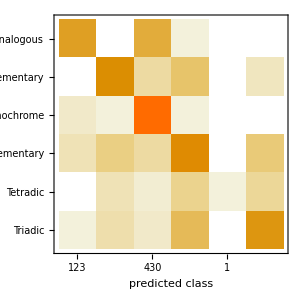

```mathematica
ClassifierMeasurementsObject[…]
```

### Hue-based classifier

Average accuracy 0.75. Bad performance on complementary and tetradic images.

```mathematica
dataH = Map[getHues,Normal[datasetHSB[All,"Color"]],{2}];
```

```mathematica
classifierH=Classify[dataH]
```

ClassifierFunction[…]

ClassifierMeasurementsObject[…]

0.719512

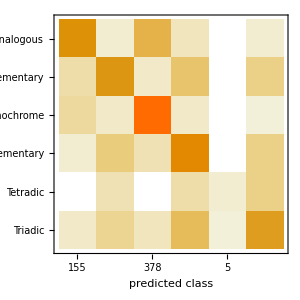

```mathematica
HMeasures=ClassifierMeasurements[classifierH,dataH]
HMeasures["Accuracy"]
HMeasures["ConfusionMatrixPlot"]
```

### Neural Networks

Neural network to classify images based on color scheme. Average accuracy 0.45-0.5:

```mathematica
classes = Normal[Keys[newdataset]]
```

{Monochrome,Analogous,Complementary,Tetradic,SplitComplementary,Triadic}

```mathematica
newnet = NetChain[{ConvolutionLayer[20,{5,5}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
ConvolutionLayer[50,{5,5}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
FlattenLayer[],
DotPlusLayer[500],
ElementwiseLayer[Ramp],
DotPlusLayer[6],
SoftmaxLayer[]}, "Input"->NetEncoder[{"Image",{200, 200},ColorSpace->"LAB"}], "Output"-> NetDecoder[{"Class",classes}]]
```

NetChain[]

```mathematica
NetInitialize[newnet][monochrome[[1]]]
```

Complementary

```mathematica
data = RandomSample[Flatten[Map[Thread[Normal[newdataset[#,"Image"]]->#]&,classes]]];
```

```mathematica
{trainingdata, validationdata} = TakeDrop[data, Round[Length[data]*0.7]];
```

```mathematica
trainnetwork = NetTrain[newnet, trainingdata, ValidationSet->validationdata]
```

NetChain[]

NetChain[]

```mathematica
meas = ClassifierMeasurements[trainnetwork, validationdata]
```

ClassifierMeasurementsObject[…]

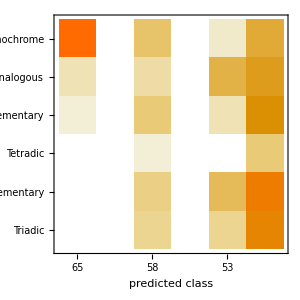

```mathematica
meas["ConfusionMatrixPlot"]
```

## Distance Classifier*

```mathematica
rc200 = RandomColor[200, ColorSpace->"HSB"];
```

```mathematica
monodif = Join[DistanceMatrix[First/@col[#]]&/@monochrome, DistanceMatrix/@Map[First,List@@@monochromaticScheme[#,RandomReal[{0, 0.5}], 5]&/@rc200, {2}]];
analogdif =Join[DistanceMatrix[First/@col[#]]&/@analogous, DistanceMatrix/@Map[First,List@@@analogousScheme[#,RandomReal[{0, 0.5}], 5]&/@rc200, {2}]];
splitdif = Join[DistanceMatrix[First/@col[#]]&/@splitcomplementary, DistanceMatrix/@Map[First,List@@@splitScheme[#,RandomReal[{0, 0.5}], 5]&/@rc200, {2}]];
compdif = Join[DistanceMatrix[First/@col[#]]&/@complementary, DistanceMatrix/@Map[First,List@@@complementaryScheme[#,RandomReal[{0, 0.5}], 5]&/@rc200, {2}]];
triadif =Join[DistanceMatrix[First/@col[#]]&/@triadic, DistanceMatrix/@Map[First,List@@@tetradicScheme[#,RandomReal[{0, 0.5}], 5]&/@rc200, {2}]];
tetradif = Join[DistanceMatrix[First/@col[#]]&/@tetradic, DistanceMatrix/@Map[First,List@@@triadicScheme[#,RandomReal[{0, 0.5}], 5]&/@rc200, {2}]];
```

```mathematica
differences = {monodif, analogdif, compdif, splitdif, tetradif, triadif};
splittest = DistanceMatrix[Map[First,List@@@Map[splitScheme[#,0.2, 5]&,rc200], {0}]];
```

```mathematica
classifier = Classify[<| "Monochromatic"-> monodif, "Analogous"->  analogdif,"Complementary"-> compdif, "Split-complementary"-> splitdif,"Tetradic" -> tetradif, "Triadic"-> triadif|>];
```

```mathematica
Export["distanceclassifier.mx", classifier]
```

distanceclassifier.mx

```mathematica
i = RandomChoice[complementary]
test =  DistanceMatrix[Map[First,List@@@col[i]]];
classifier[test]
```

-Graphics-

Complementary

```mathematica
class[img_]:= classifier[DistanceMatrix[First/@col[img]]]
```

```mathematica
i = ExampleData[{"TestImage", "Mandrill"}]...
class[i]
```

## Kuler & MTurk data exploration

### Dataset

Kuler - Color data collected from Adobe Kuler website, which is mostly used by professional designers. Has community bias, since popular palettes are more visible than those with few ratings.
   MTurk - data collected and assembled by O. Donovan. 1301 participants rated 10743 Kuler themes from various rating categories. 5 stars make up to only 9 % of the ratings to that of 24 % for Kuler. No community bias.

```mathematica
path=FileNameJoin[{NotebookDirectory[],"Imgs"}];
```

```mathematica
wheelsmall[list_/;VectorQ[list, ColorQ]]:=With[{sectors=36},angle=2 Pi/sectors;
	Graphics[{Table[{{Hue[(i/sectors), 1,b], Annulus[{0,0}, {b-.2, b+0.01}, {i angle,(i+1.01) angle}]}},{i,0,sectors-1}, {b, $MachineEpsilon+.2,1,.2}], 
		Black,EdgeForm[White], Disk[{#3 Cos[2Pi #1], #3 Sin[2Pi #1]}, .01] &@@@
			ColorConvert[list, "HSB"]}]];
```

```mathematica
kulerData = Import["kulerData.mat", Path->NotebookDirectory[]]
```

{{{{0.423529,0.627451,0.207843,0.376471,0.882353},{0.0901961,0.0901961,0.4,0.360784,0.941176},{0.2,0.65098,0.690196,0.478431,0.0666667},44980,{0.0941176,0.843137,1.,0.831373,0.411765},{0.392157,0.631373,0.878431,0.25098,0.27451},{0.439216,0.619608,0.454902,0.278431,0.388235}},{1},{1}},2,{1}}
 |  |  |  |

```mathematica
mturkData = Import["mturkData.mat", Path->NotebookDirectory[]]
```

{{{3.23529},{3.32432},{3.27273},{2.7027},{2.59091},{3.25},{3.17143},{3.08571},{4.35294},{3.48649},{2.94286},{3.08824},{3.11765},{3.03125},{3.24242},10713,{3.11429},{2.85714},{3.57143},{2.31429},{2.79412},{3.21212},{2.44118},{2.93056},{2.57143},{2.45455},{3.},{3.28571},{2.88571},{2.69444},{2.91176}},3,{1}}
 |  |  |  |

```mathematica
rangeKuler = Range[Length[kulerData[[1, 1]]]];
kulerRgbColors = RGBColor/@Transpose[kulerData[[1, {1,2,3},#]]]&/@rangeKuler
```

{{RGBColor[{0.4235294117647059, 0.615686274509804, 0.6784313725490196}],RGBColor[{0.6274509803921569, 0.6235294117647059, 0.6784313725490196}],RGBColor[{0.20784313725490197, 0.24313725490196078, 0.26666666666666666}],RGBColor[{0.3764705882352941, 0.788235294117647, 0.8823529411764706}],RGBColor[{0.8823529411764706, 0., 0.0392156862745098}]},{RGBColor[{0.09019607843137255, 0.25098039215686274, 0.047058823529411764}],RGBColor[{0.09019607843137255, 0.09019607843137255, 0.10980392156862745}],RGBColor[{0.4, 0.1568627450980392, 0.5215686274509804}],RGBColor[{0.3607843137254902, 0.7098039215686275, 0.23921568627450981}],RGBColor[{0.9411764705882353, 0.058823529411764705, 0.22745098039215686}]},{RGBColor[{0.2, 0.7215686274509804, 0.592156862745098}],RGBColor[{0.6509803921568628, 0.6901960784313725, 0.592156862745098}],RGBColor[{0.6901960784313725, 0.4, 0.34901960784313724}],RGBColor[{0.47843137254901963, 0.6196078431372549, 0.13725490196078433}],RGBColor[{0.06666666666666667, 0.6392156862745098, 0.6313725490196078}]},{RGBColor[{0.058823529411764705, 0.26666666666666666, 0.6}],RGBColor[{0.5098039215686274, 0., 0.7176470588235294}],RGBColor[{0.42745098039215684, 0.25882352941176473, 0.6470588235294118}],RGBColor[{0.5098039215686274, 0.5686274509803921, 0.24705882352941178}],RGBColor[{0.9098039215686274, 0.9176470588235294, 0.0784313725490196}]},{RGBColor[{0.17254901960784313, 0.8196078431372549, 0.21568627450980393}],RGBColor[{0.8196078431372549, 0.5019607843137255, 0.7058823529411765}],RGBColor[{0.9019607843137255, 0.9058823529411765, 0.5686274509803921}],RGBColor[{0.9764705882352941, 0.9176470588235294, 0.6}],RGBColor[{0.8784313725490196, 0.9568627450980393, 0.}]},{RGBColor[{1., 0., 1.}],RGBColor[{1., 0.9921568627450981, 0.}],RGBColor[{0., 0., 1.}],RGBColor[{0., 1., 0.}],RGBColor[{0.5254901960784314, 0.8941176470588236, 1.}]},{RGBColor[{0.4196078431372549, 1., 0.19607843137254902}],RGBColor[{0.8274509803921568, 1., 0.5333333333333333}],RGBColor[{0.6313725490196078, 1., 0.7843137254901961}],RGBColor[{0., 1., 0.}],RGBColor[{0.3254901960784314, 1., 0.5333333333333333}]},{RGBColor[{1., 0., 1.}],RGBColor[{1., 0.996078431372549, 0.}],RGBColor[{0., 0., 1.}],RGBColor[{0., 1., 0.}],RGBColor[{1., 0., 0.}]},{RGBColor[{1., 0., 1.}],RGBColor[{1., 0.996078431372549, 0.}],RGBColor[{0., 0., 1.}],RGBColor[{0., 1., 0.}],RGBColor[{0.9568627450980393, 1., 0.9568627450980393}]},{RGBColor[{0.6745098039215687, 0.5019607843137255, 1.}],RGBColor[{1., 0.803921568627451, 0.3058823529411765}],RGBColor[{0.3843137254901961, 0.6, 1.}],RGBColor[{0.4745098039215686, 1., 0.42745098039215684}],RGBColor[{1., 0.45098039215686275, 0.7215686274509804}]},{RGBColor[{0.8941176470588236, 0.41568627450980394, 1.}],RGBColor[{1., 0.9921568627450981, 0.43137254901960786}],RGBColor[{0., 0.6, 1.}],RGBColor[{0.8549019607843137, 0.8980392156862745, 1.}],RGBColor[{0.3254901960784314, 0.2784313725490196, 1.}]},{RGBColor[{0., 0., 0.3568627450980392}],RGBColor[{0., 0., 0.5803921568627451}],RGBColor[{0., 0.6, 0.}],RGBColor[{0., 0., 0.11764705882352941}],RGBColor[{0.49019607843137253, 0., 0.}]},{RGBColor[{0.4823529411764706, 0.13725490196078433, 0.13333333333333333}],RGBColor[{0.6313725490196078, 0.21568627450980393, 0.4745098039215686}],RGBColor[{0.20392156862745098, 0.11764705882352941, 0.2823529411764706}],RGBColor[{0.13725490196078433, 0.13333333333333333, 0.4823529411764706}],RGBColor[{0.25882352941176473, 0.4666666666666667, 0.6823529411764706}]},{RGBColor[{0.8, 0.08235294117647059, 0.788235294117647}],RGBColor[{1., 0.4549019607843137, 0.8549019607843137}],RGBColor[{0.3607843137254902, 0.596078431372549, 0.6}],RGBColor[{0.08235294117647059, 0.788235294117647, 0.8}],RGBColor[{0.20392156862745098, 1., 0.611764705882353}]},{RGBColor[{0.11764705882352941, 0.3803921568627451, 0.3843137254901961}],RGBColor[{0.3764705882352941, 0.24313725490196078, 0.5843137254901961}],RGBColor[{0.2823529411764706, 0.12156862745098039, 0.08627450980392157}],RGBColor[{0.8823529411764706, 0.23921568627450981, 0.09803921568627451}],RGBColor[{0.5843137254901961, 0.20784313725490197, 0.12549019607843137}]},{RGBColor[{0.3176470588235294, 0.5647058823529412, 0.803921568627451}],RGBColor[{0.5568627450980392, 0.8274509803921568, 0.788235294117647}],RGBColor[{1., 0.9568627450980393, 0.3254901960784314}],RGBColor[{1., 0.8196078431372549, 0.5411764705882353}],RGBColor[{0.9333333333333333, 0.09411764705882353, 0.2901960784313726}]},{RGBColor[{0.807843137254902, 0.49019607843137253, 0.12549019607843137}],RGBColor[{0.6588235294117647, 0.4, 0.10196078431372549}],RGBColor[{0.40784313725490196, 0.24705882352941178, 0.06274509803921569}],RGBColor[{0.1568627450980392, 0.09411764705882353, 0.023529411764705882}],RGBColor[{0.9098039215686274, 0.5529411764705883, 0.1450980392156863}]},{RGBColor[{0.09803921568627451, 0.2549019607843137, 0.023529411764705882}],RGBColor[{0.0392156862745098, 0.10588235294117647, 0.00784313725490196}],RGBColor[{0.33725490196078434, 0.8549019607843137, 0.08235294117647059}],RGBColor[{0.23921568627450981, 0.6039215686274509, 0.058823529411764705}],RGBColor[{0.1411764705882353, 0.3568627450980392, 0.03529411764705882}]},{RGBColor[{0.4235294117647059, 0.2823529411764706, 0.03137254901960784}],RGBColor[{0.3058823529411765, 0.1843137254901961, 0.}],RGBColor[{0.023529411764705882, 0.01568627450980392, 0.}],RGBColor[{0.6196078431372549, 0.4117647058823529, 0.06274509803921569}],RGBColor[{0.5254901960784314, 0.35294117647058826, 0.043137254901960784}]},{RGBColor[{0.36470588235294116, 0.8588235294117647, 0.}],RGBColor[{0.023529411764705882, 0.26666666666666666, 0.8901960784313725}],RGBColor[{0.4117647058823529, 0., 0.7254901960784313}],RGBColor[{0.9490196078431372, 0.6941176470588235, 0.}],RGBColor[{0.8313725490196079, 0.043137254901960784, 0.12941176470588237}]},{RGBColor[{0.8941176470588236, 0., 0.}],RGBColor[{0.24313725490196078, 0., 0.}],RGBColor[{0.4980392156862745, 0., 0.}],RGBColor[{0.7450980392156863, 0., 0.}],RGBColor[{1., 0., 0.}]},{RGBColor[{0.45098039215686275, 0.2235294117647059, 0.4588235294117647}],RGBColor[{0.4980392156862745, 0.25882352941176473, 0.29411764705882354}],RGBColor[{0.34509803921568627, 0.4980392156862745, 0.25882352941176473}],RGBColor[{0.23921568627450981, 0.4588235294117647, 0.35294117647058826}],RGBColor[{0.40784313725490196, 0.36470588235294116, 0.23137254901960785}]},{RGBColor[{0.45098039215686275, 0.3764705882352941, 1.}],RGBColor[{0.6352941176470588, 0.3411764705882353, 0.9098039215686274}],RGBColor[{0.9098039215686274, 0.3411764705882353, 0.7294117647058823}],RGBColor[{1., 0.39215686274509803, 0.5686274509803921}],RGBColor[{0.9490196078431372, 0.42745098039215684, 1.}]},{RGBColor[{0.49019607843137253, 0.5882352941176471, 0.6078431372549019}],RGBColor[{0.26666666666666666, 0.3843137254901961, 0.4549019607843137}],RGBColor[{0.7411764705882353, 0.807843137254902, 0.3411764705882353}],RGBColor[{0.5843137254901961, 0.6078431372549019, 0.4392156862745098}],RGBColor[{0.40784313725490196, 0.3803921568627451, 0.3333333333333333}]},{RGBColor[{0.11764705882352941, 0.3686274509803922, 0.3137254901960784}],RGBColor[{0.1450980392156863, 0.21568627450980393, 0.21568627450980393}],RGBColor[{0.5686274509803921, 0.5450980392156862, 0.4666666666666667}],RGBColor[{0.3686274509803922, 0.3137254901960784, 0.11764705882352941}],RGBColor[{0.16862745098039217, 0.09803921568627451, 0.07058823529411765}]},{RGBColor[{0.6588235294117647, 1., 0.047058823529411764}],RGBColor[{0.3843137254901961, 0.9098039215686274, 0.043137254901960784}],RGBColor[{0.043137254901960784, 0.9098039215686274, 0.13333333333333333}],RGBColor[{0.047058823529411764, 1., 0.3843137254901961}],RGBColor[{0.22745098039215686, 1., 0.09803921568627451}]},{RGBColor[{0.45098039215686275, 0.4588235294117647, 0.3843137254901961}],RGBColor[{0.4745098039215686, 0.49411764705882355, 0.5333333333333333}],RGBColor[{0.43529411764705883, 0.49411764705882355, 0.4980392156862745}],RGBColor[{0.4588235294117647, 0.3607843137254902, 0.396078431372549}],RGBColor[{0.40784313725490196, 0.3686274509803922, 0.3411764705882353}]},{RGBColor[{0.4588235294117647, 0.3568627450980392, 0.07058823529411765}],RGBColor[{0.16470588235294117, 0.4980392156862745, 0.023529411764705882}],RGBColor[{0.023529411764705882, 0.2, 0.4980392156862745}],RGBColor[{0.2823529411764706, 0.0196078431372549, 0.4588235294117647}],RGBColor[{0., 0.4117647058823529, 0.27450980392156865}]},{RGBColor[{0.8156862745098039, 0.8784313725490196, 0.8784313725490196}],RGBColor[{0.3215686274509804, 0.5764705882352941, 0.27450980392156865}],RGBColor[{0.25882352941176473, 0.2784313725490196, 0.2784313725490196}],RGBColor[{0.4980392156862745, 0.5647058823529412, 0.5764705882352941}],RGBColor[{0.2784313725490196, 0.13333333333333333, 0.12156862745098039}]},{RGBColor[{0.6901960784313725, 0.6078431372549019, 0.08235294117647059}],RGBColor[{0.4196078431372549, 0.06274509803921569, 0.07058823529411765}],RGBColor[{0.4823529411764706, 0.8862745098039215, 0.9215686274509803}],RGBColor[{0.5019607843137255, 0.6901960784313725, 0.}],RGBColor[{0.9215686274509803, 0.5686274509803921, 0.08235294117647059}]},{RGBColor[{0.7450980392156863, 0.9215686274509803, 0.06274509803921569}],RGBColor[{0.49411764705882355, 0.6196078431372549, 0.}],RGBColor[{0.33725490196078434, 0.16862745098039217, 1.}],RGBColor[{0.1411764705882353, 0.0196078431372549, 0.6196078431372549}],RGBColor[{0.23921568627450981, 0.06274509803921569, 0.9215686274509803}]},{RGBColor[{0.47843137254901963, 0.09019607843137255, 0.10588235294117647}],RGBColor[{0.3254901960784314, 0.2549019607843137, 0.23529411764705882}],RGBColor[{0.6039215686274509, 0.6078431372549019, 0.6784313725490196}],RGBColor[{0.37254901960784315, 0.3764705882352941, 0.47843137254901963}],RGBColor[{0.12941176470588237, 0.20784313725490197, 0.2784313725490196}]},{RGBColor[{0.6705882352941176, 0.9215686274509803, 0.38823529411764707}],RGBColor[{0.3803921568627451, 0.6196078431372549, 0.10196078431372549}],RGBColor[{0.596078431372549, 0.24313725490196078, 1.}],RGBColor[{0.2901960784313726, 0.00784313725490196, 0.6196078431372549}],RGBColor[{0.47843137254901963, 0.10588235294117647, 0.9215686274509803}]},{RGBColor[{0.9019607843137255, 0.14901960784313725, 0.4196078431372549}],RGBColor[{0.984313725490196, 0.6627450980392157, 0.18823529411764706}],RGBColor[{0.1803921568627451, 0.6588235294117647, 0.9333333333333333}],RGBColor[{0.6313725490196078, 0.40784313725490196, 0.8980392156862745}],RGBColor[{0.44313725490196076, 0.5686274509803921, 0.12941176470588237}]},{RGBColor[{0.9450980392156862, 1., 0.047058823529411764}],RGBColor[{0.6431372549019608, 0.9058823529411765, 0.043137254901960784}],RGBColor[{0.21176470588235294, 0.9058823529411765, 0.043137254901960784}],RGBColor[{0.047058823529411764, 1., 0.10196078431372549}],RGBColor[{0.44313725490196076, 1., 0.}]},{RGBColor[{0.7333333333333333, 0.38823529411764707, 0.14901960784313725}],RGBColor[{0.27450980392156865, 0.4117647058823529, 0.2627450980392157}],RGBColor[{0.1803921568627451, 0.3254901960784314, 0.3254901960784314}],RGBColor[{0.1803921568627451, 0.5725490196078431, 0.40784313725490196}],RGBColor[{0.047058823529411764, 0.1450980392156863, 0.14901960784313725}]},{RGBColor[{0.7254901960784313, 0.32941176470588235, 1.}],RGBColor[{0.807843137254902, 0.30196078431372547, 0.9058823529411765}],RGBColor[{0.9058823529411765, 0.30196078431372547, 0.7019607843137254}],RGBColor[{1., 0.32941176470588235, 0.6039215686274509}],RGBColor[{1., 0.3803921568627451, 0.9411764705882353}]},{RGBColor[{0.8627450980392157, 1., 0.5411764705882353}],RGBColor[{0.2784313725490196, 0.9333333333333333, 0.43137254901960786}],RGBColor[{0., 0.9803921568627451, 0.9294117647058824}],RGBColor[{0.06274509803921569, 0.22745098039215686, 0.6941176470588235}],RGBColor[{0.047058823529411764, 0.9490196078431372, 0.01568627450980392}]},{RGBColor[{0.34901960784313724, 0.09803921568627451, 0.043137254901960784}],RGBColor[{0.3058823529411765, 0.29411764705882354, 0.12941176470588237}],RGBColor[{0.3607843137254902, 0.3803921568627451, 0.33725490196078434}],RGBColor[{0.8196078431372549, 0.7843137254901961, 0.5254901960784314}],RGBColor[{0.3215686274509804, 0.17254901960784313, 0.09019607843137255}]},{RGBColor[{0.2, 0.18823529411764706, 0.16470588235294117}],RGBColor[{0.22745098039215686, 0.23529411764705882, 0.1607843137254902}],RGBColor[{0.17254901960784313, 0.23529411764705882, 0.1607843137254902}],RGBColor[{0.13333333333333333, 0.2, 0.1450980392156863}],RGBColor[{0.12941176470588237, 0.14901960784313725, 0.10588235294117647}]},{RGBColor[{0.1568627450980392, 0.09411764705882353, 0.2196078431372549}],RGBColor[{0.25098039215686274, 0.20784313725490197, 0.36470588235294116}],RGBColor[{0.38823529411764707, 0.3254901960784314, 0.611764705882353}],RGBColor[{0.4627450980392157, 0.5254901960784314, 0.7333333333333333}],RGBColor[{0.22745098039215686, 0.13725490196078433, 0.3176470588235294}]},{RGBColor[{0.2, 0.14901960784313725, 0.}],RGBColor[{0., 0.6784313725490196, 0.4549019607843137}],RGBColor[{0.2196078431372549, 0., 0.}],RGBColor[{0.01568627450980392, 0.5490196078431373, 0.4745098039215686}],RGBColor[{0., 0., 0.}]},{RGBColor[{0.5490196078431373, 0.5764705882352941, 0.13333333333333333}],RGBColor[{0.7372549019607844, 0.792156862745098, 0.16470588235294117}],RGBColor[{0.9764705882352941, 0.9490196078431372, 0.596078431372549}],RGBColor[{0.3254901960784314, 0.3411764705882353, 0.17647058823529413}],RGBColor[{0.6823529411764706, 0.5529411764705883, 0.17647058823529413}]},{RGBColor[{0., 0., 0.}],RGBColor[{0., 0., 0.}],RGBColor[{0., 0., 0.}],RGBColor[{0., 0., 0.}],RGBColor[{0., 0., 0.}]},{RGBColor[{0.6039215686274509, 0.6509803921568628, 0.6823529411764706}],RGBColor[{0.3686274509803922, 0.4117647058823529, 0.44313725490196076}],RGBColor[{0.9803921568627451, 0.6823529411764706, 0.48627450980392156}],RGBColor[{0.4470588235294118, 0.1843137254901961, 0.01568627450980392}],RGBColor[{0.6823529411764706, 0.3803921568627451, 0.1843137254901961}]},44896,{RGBColor[{0.3333333333333333, 0.011764705882352941, 0.2235294117647059}],RGBColor[{0.6352941176470588, 0.25098039215686274, 0.44313725490196076}],RGBColor[{0.8274509803921568, 0.7568627450980392, 0.6313725490196078}],RGBColor[{0.6470588235294118, 0.5529411764705883, 0.26666666666666666}],RGBColor[{0.3607843137254902, 0.3137254901960784, 0.1803921568627451}]},{RGBColor[{0.2196078431372549, 0.2196078431372549, 0.3686274509803922}],RGBColor[{0.09803921568627451, 0.12941176470588237, 0.16862745098039217}],RGBColor[{0.06274509803921569, 0.0784313725490196, 0.09803921568627451}],RGBColor[{0.047058823529411764, 0.050980392156862744, 0.07058823529411765}],RGBColor[{0.03137254901960784, 0.027450980392156862, 0.050980392156862744}]},{RGBColor[{0.7058823529411765, 0.7333333333333333, 0.7176470588235294}],RGBColor[{0.8784313725490196, 0.6313725490196078, 0.25098039215686274}],RGBColor[{1., 0.5176470588235295, 0.}],RGBColor[{0.30196078431372547, 0.4392156862745098, 0.058823529411764705}],RGBColor[{0.03137254901960784, 0.16862745098039217, 0.0784313725490196}]},{RGBColor[{0.4392156862745098, 0.3607843137254902, 0.2823529411764706}],RGBColor[{0.5215686274509804, 0.403921568627451, 0.15294117647058825}],RGBColor[{0.10588235294117647, 0.10980392156862745, 0.1607843137254902}],RGBColor[{0.07058823529411765, 0.1568627450980392, 0.23921568627450981}],RGBColor[{0.30196078431372547, 0.36470588235294116, 0.4}]},{RGBColor[{0.09019607843137255, 0.10980392156862745, 0.1607843137254902}],RGBColor[{0.21176470588235294, 0.12156862745098039, 0.2980392156862745}],RGBColor[{0.13725490196078433, 0.11764705882352941, 0.25882352941176473}],RGBColor[{0.19607843137254902, 0.32941176470588235, 0.38823529411764707}],RGBColor[{0.5294117647058824, 0.4470588235294118, 0.5294117647058824}]},{RGBColor[{0.8509803921568627, 0.3568627450980392, 0.3568627450980392}],RGBColor[{0.6509803921568628, 0.4235294117647059, 0.29411764705882354}],RGBColor[{0.7490196078431373, 0.5725490196078431, 0.35294117647058826}],RGBColor[{0.9490196078431372, 0.8392156862745098, 0.6352941176470588}],RGBColor[{0.058823529411764705, 0.07058823529411765, 0.14901960784313725}]},{RGBColor[{0.9490196078431372, 0.9490196078431372, 0.9490196078431372}],RGBColor[{0.8509803921568627, 0.01568627450980392, 0.01568627450980392}],RGBColor[{0.01568627450980392, 0.4666666666666667, 0.7490196078431373}],RGBColor[{0.12549019607843137, 0.23529411764705882, 0.45098039215686275}],RGBColor[{0.7490196078431373, 0.043137254901960784, 0.10196078431372549}]},{RGBColor[{0.23137254901960785, 0.21568627450980393, 0.21568627450980393}],RGBColor[{0.10980392156862745, 0.10196078431372549, 0.12941176470588237}],RGBColor[{0.43137254901960786, 0.3803921568627451, 0.3686274509803922}],RGBColor[{0.2196078431372549, 0.20784313725490197, 0.23137254901960785}],RGBColor[{0.12941176470588237, 0.12156862745098039, 0.10196078431372549}]},{RGBColor[{0.9803921568627451, 0.9607843137254902, 0.9450980392156862}],RGBColor[{0.6980392156862745, 0.6509803921568628, 0.5882352941176471}],RGBColor[{0.5215686274509804, 0.5294117647058824, 0.5254901960784314}],RGBColor[{0.2980392156862745, 0.34901960784313724, 0.34509803921568627}],RGBColor[{0.12549019607843137, 0.1568627450980392, 0.18823529411764706}]},{RGBColor[{0.12549019607843137, 0.1450980392156863, 0.1607843137254902}],RGBColor[{0.19215686274509805, 0.27450980392156865, 0.2784313725490196}],RGBColor[{0.3686274509803922, 0.3686274509803922, 0.2627450980392157}],RGBColor[{0.4, 0.5686274509803921, 0.44313725490196076}],RGBColor[{0.054901960784313725, 0.7607843137254902, 0.47843137254901963}]},{RGBColor[{1., 0.8392156862745098, 0.4}],RGBColor[{0.8117647058823529, 0.792156862745098, 0.5529411764705883}],RGBColor[{0.6392156862745098, 0.5803921568627451, 0.45098039215686275}],RGBColor[{0.43137254901960786, 0.3058823529411765, 0.23529411764705882}],RGBColor[{0.16862745098039217, 0.13333333333333333, 0.08235294117647059}]},{RGBColor[{0.396078431372549, 0.7607843137254902, 0.611764705882353}],RGBColor[{0.2901960784313726, 0.5098039215686274, 0.24313725490196078}],RGBColor[{0.2, 0.2980392156862745, 0.24705882352941178}],RGBColor[{0.08235294117647059, 0.10980392156862745, 0.10588235294117647}],RGBColor[{0.5686274509803921, 0.4823529411764706, 0.16862745098039217}]},{RGBColor[{0.6509803921568628, 0.5450980392156862, 0.23529411764705882}],RGBColor[{0.6705882352941176, 0.8509803921568627, 0.01568627450980392}],RGBColor[{0.18823529411764706, 0.9490196078431372, 0.4549019607843137}],RGBColor[{0.23921568627450981, 0.9490196078431372, 0.8784313725490196}],RGBColor[{0.011764705882352941, 0.19215686274509805, 0.5490196078431373}]},{RGBColor[{0.34901960784313724, 0.19607843137254902, 0.1803921568627451}],RGBColor[{0.17254901960784313, 0.23137254901960785, 0.38823529411764707}],RGBColor[{0.47843137254901963, 0.4235294117647059, 0.43529411764705883}],RGBColor[{0.8745098039215686, 0.9058823529411765, 0.9490196078431372}],RGBColor[{0.6901960784313725, 0.7568627450980392, 0.8509803921568627}]},{RGBColor[{0.5490196078431373, 0.27058823529411763, 0.10980392156862745}],RGBColor[{0.7607843137254902, 0.5372549019607843, 0.3607843137254902}],RGBColor[{0.27058823529411763, 0.17254901960784313, 0.18823529411764706}],RGBColor[{0.12549019607843137, 0.15294117647058825, 0.2235294117647059}],RGBColor[{0.5529411764705883, 0.7254901960784313, 0.9490196078431372}]},{RGBColor[{0.1843137254901961, 0.49019607843137253, 0.4745098039215686}],RGBColor[{0.6549019607843137, 0.6588235294117647, 0.5137254901960784}],RGBColor[{0.2549019607843137, 0.3803921568627451, 0.2784313725490196}],RGBColor[{0.17254901960784313, 0.22745098039215686, 0.23137254901960785}],RGBColor[{0.10196078431372549, 0.10980392156862745, 0.12941176470588237}]},{RGBColor[{0.27450980392156865, 0.4392156862745098, 0.49019607843137253}],RGBColor[{0.047058823529411764, 0.1607843137254902, 0.18823529411764706}],RGBColor[{0.29411764705882354, 0.3215686274509804, 0.3058823529411765}],RGBColor[{0.796078431372549, 0.807843137254902, 0.6784313725490196}],RGBColor[{0.7215686274509804, 0.6509803921568628, 0.4}]},{RGBColor[{0.7294117647058823, 0.33725490196078434, 0.1411764705882353}],RGBColor[{0.44313725490196076, 0.5490196078431373, 0.40784313725490196}],RGBColor[{0.6588235294117647, 0.7294117647058823, 0.592156862745098}],RGBColor[{0.7568627450980392, 0.9294117647058824, 0.7803921568627451}],RGBColor[{0.34901960784313724, 0.6705882352941176, 0.5686274509803921}]},{RGBColor[{0.7294117647058823, 0.6627450980392157, 0.4666666666666667}],RGBColor[{0.788235294117647, 0.3764705882352941, 0.2823529411764706}],RGBColor[{0.6588235294117647, 0.34901960784313724, 0.10196078431372549}],RGBColor[{0.3686274509803922, 0.27450980392156865, 0.19215686274509805}],RGBColor[{0.1843137254901961, 0.1568627450980392, 0.2}]},{RGBColor[{0.1607843137254902, 0.15294117647058825, 0.1450980392156863}],RGBColor[{0.25882352941176473, 0.23529411764705882, 0.16470588235294117}],RGBColor[{0.34901960784313724, 0.3058823529411765, 0.23921568627450981}],RGBColor[{0.5294117647058824, 0.47843137254901963, 0.37254901960784315}],RGBColor[{0.24313725490196078, 0.2901960784313726, 0.26666666666666666}]},{RGBColor[{1., 0.19607843137254902, 0.26666666666666666}],RGBColor[{0.9607843137254902, 0.5019607843137255, 0.43529411764705883}],RGBColor[{1., 0.6823529411764706, 0.5137254901960784}],RGBColor[{1., 0.792156862745098, 0.6901960784313725}],RGBColor[{1., 0.9607843137254902, 0.7764705882352941}]},{RGBColor[{0.13333333333333333, 0.13725490196078433, 0.1411764705882353}],RGBColor[{0.47058823529411764, 0.1803921568627451, 0.}],RGBColor[{0.6901960784313725, 0.2823529411764706, 0.08627450980392157}],RGBColor[{0.8705882352941177, 0.6, 0.16862745098039217}],RGBColor[{0.9490196078431372, 0.7764705882352941, 0.37254901960784315}]},{RGBColor[{0.09019607843137255, 0.09019607843137255, 0.14901960784313725}],RGBColor[{0.3607843137254902, 0.10588235294117647, 0.2549019607843137}],RGBColor[{0.6980392156862745, 0.37254901960784315, 0.3568627450980392}],RGBColor[{0.8784313725490196, 0.6431372549019608, 0.3686274509803922}],RGBColor[{0.8705882352941177, 0.8196078431372549, 0.8196078431372549}]},{RGBColor[{0.7098039215686275, 0.32941176470588235, 0.1411764705882353}],RGBColor[{0.6980392156862745, 0.6745098039215687, 0.19607843137254902}],RGBColor[{0.49019607843137253, 0.7490196078431373, 0.5529411764705883}],RGBColor[{1., 0.7254901960784313, 0.2980392156862745}],RGBColor[{1., 0.8941176470588236, 0.6}]},{RGBColor[{0.7647058823529411, 0.12549019607843137, 0.1411764705882353}],RGBColor[{0.7176470588235294, 0.5607843137254902, 0.3803921568627451}],RGBColor[{0.23137254901960785, 0.2823529411764706, 0.1450980392156863}],RGBColor[{0.6, 0.43529411764705883, 0.4235294117647059}],RGBColor[{0.9921568627450981, 0.34901960784313724, 0.3215686274509804}]},{RGBColor[{0.5294117647058824, 0.7607843137254902, 0.054901960784313725}],RGBColor[{0.8431372549019608, 0.9098039215686274, 0.5843137254901961}],RGBColor[{1., 0.9647058823529412, 0.8156862745098039}],RGBColor[{0.7490196078431373, 0.6470588235294118, 0.6470588235294118}],RGBColor[{0.4117647058823529, 0.30196078431372547, 0.43137254901960786}]},{RGBColor[{0.9215686274509803, 0.6862745098039216, 0.09803921568627451}],RGBColor[{0.9215686274509803, 0.2627450980392157, 0.3333333333333333}],RGBColor[{0.5607843137254902, 0.12549019607843137, 0.20392156862745098}],RGBColor[{0.3137254901960784, 0.058823529411764705, 0.07058823529411765}],RGBColor[{0.9647058823529412, 0.8352941176470589, 0.6901960784313725}]},{RGBColor[{0.1803921568627451, 0.03529411764705882, 0.027450980392156862}],RGBColor[{0.2784313725490196, 0.10196078431372549, 0.11372549019607843}],RGBColor[{1., 0.29411764705882354, 0.08235294117647059}],RGBColor[{0.6588235294117647, 0.19215686274509805, 0.14901960784313725}],RGBColor[{0.5098039215686274, 0.13725490196078433, 0.09411764705882353}]},{RGBColor[{0.34901960784313724, 0.3058823529411765, 0.2784313725490196}],RGBColor[{0.4117647058823529, 0.3254901960784314, 0.2823529411764706}],RGBColor[{0.45098039215686275, 0.3137254901960784, 0.2196078431372549}],RGBColor[{0.5215686274509804, 0.34901960784313724, 0.10980392156862745}],RGBColor[{0.5882352941176471, 0.38823529411764707, 0.}]},{RGBColor[{0.12941176470588237, 0.1607843137254902, 0.1803921568627451}],RGBColor[{0.24705882352941178, 0.24705882352941178, 0.2784313725490196}],RGBColor[{1., 0.5647058823529412, 0.4627450980392157}],RGBColor[{0.6588235294117647, 0.4627450980392157, 0.43529411764705883}],RGBColor[{0.5098039215686274, 0.43529411764705883, 0.4470588235294118}]},{RGBColor[{0.4588235294117647, 0.35294117647058826, 0.40784313725490196}],RGBColor[{0.7490196078431373, 0.6196078431372549, 0.6392156862745098}],RGBColor[{0.8588235294117647, 0.6980392156862745, 0.6745098039215687}],RGBColor[{0.9607843137254902, 0.7764705882352941, 0.6980392156862745}],RGBColor[{1., 0.7294117647058823, 0.6078431372549019}]},{RGBColor[{0., 0.17254901960784313, 0.4117647058823529}],RGBColor[{0., 0.1411764705882353, 0.23137254901960785}],RGBColor[{0.09803921568627451, 0.09803921568627451, 0.07450980392156863}],RGBColor[{0.6627450980392157, 0.7607843137254902, 0.5607843137254902}],RGBColor[{0.8117647058823529, 0.9294117647058824, 0.8196078431372549}]},{RGBColor[{0.6509803921568628, 0.4235294117647059, 0.29411764705882354}],RGBColor[{0.3764705882352941, 0.2901960784313726, 0.30196078431372547}],RGBColor[{0.4235294117647059, 0.30980392156862746, 0.2549019607843137}],RGBColor[{0.45098039215686275, 0.1607843137254902, 0.23921568627450981}],RGBColor[{0.6509803921568628, 0.1803921568627451, 0.26666666666666666}]},{RGBColor[{0.8588235294117647, 0.8313725490196079, 0.7803921568627451}],RGBColor[{0.8117647058823529, 0.7686274509803922, 0.7058823529411765}],RGBColor[{0.7607843137254902, 0.7333333333333333, 0.6274509803921569}],RGBColor[{0.592156862745098, 0.6, 0.5098039215686274}],RGBColor[{0.3333333333333333, 0.4, 0.3411764705882353}]},{RGBColor[{0.4980392156862745, 0.09803921568627451, 0.19607843137254902}],RGBColor[{0.7607843137254902, 0.12156862745098039, 0.22745098039215686}],RGBColor[{0.9411764705882353, 0.27450980392156865, 0.43137254901960786}],RGBColor[{0.9607843137254902, 0.6941176470588235, 0.6392156862745098}],RGBColor[{0.8117647058823529, 0.6549019607843137, 0.7215686274509804}]},{RGBColor[{0.8901960784313725, 0.7137254901960784, 0.48627450980392156}],RGBColor[{0.6823529411764706, 0.5411764705882353, 0.39215686274509803}],RGBColor[{0.35294117647058826, 0.35294117647058826, 0.27450980392156865}],RGBColor[{0.11372549019607843, 0.19215686274509805, 0.2196078431372549}],RGBColor[{0.00784313725490196, 0.11764705882352941, 0.12941176470588237}]},{RGBColor[{0.4, 0.2, 0.06274509803921569}],RGBColor[{0.6, 0.24313725490196078, 0.09803921568627451}],RGBColor[{0.34901960784313724, 0.27450980392156865, 0.058823529411764705}],RGBColor[{0.07450980392156863, 0.25098039215686274, 0.17254901960784313}],RGBColor[{0.0392156862745098, 0.14901960784313725, 0.13725490196078433}]},{RGBColor[{0.09803921568627451, 0.08235294117647059, 0.09803921568627451}],RGBColor[{0.13333333333333333, 0.11764705882352941, 0.14901960784313725}],RGBColor[{0.25098039215686274, 0.22745098039215686, 0.21568627450980393}],RGBColor[{0.4980392156862745, 0.4745098039215686, 0.38823529411764707}],RGBColor[{0.6392156862745098, 0.6980392156862745, 0.5843137254901961}]},{RGBColor[{0.06274509803921569, 0.09803921568627451, 0.0784313725490196}],RGBColor[{0.11764705882352941, 0.14901960784313725, 0.12156862745098039}],RGBColor[{0.24705882352941178, 0.2235294117647059, 0.25098039215686274}],RGBColor[{0.5490196078431373, 0.2901960784313726, 0.28627450980392155}],RGBColor[{1., 0.4117647058823529, 0.34901960784313724}]},{RGBColor[{0.1607843137254902, 0.011764705882352941, 0.13725490196078433}],RGBColor[{0.16862745098039217, 0.1450980392156863, 0.16862745098039217}],RGBColor[{0.3607843137254902, 0.3764705882352941, 0.30196078431372547}],RGBColor[{0.6235294117647059, 0.6745098039215687, 0.5411764705882353}],RGBColor[{0.8117647058823529, 0.807843137254902, 0.592156862745098}]},{RGBColor[{0.8980392156862745, 0.6588235294117647, 0.788235294117647}],RGBColor[{0.9490196078431372, 0.8313725490196079, 0.6666666666666666}],RGBColor[{0.8, 0.796078431372549, 0.6039215686274509}],RGBColor[{0.5764705882352941, 0.6980392156862745, 0.6392156862745098}],RGBColor[{0.48627450980392156, 0.5607843137254902, 0.6}]},{RGBColor[{0.03137254901960784, 0.09803921568627451, 0.09803921568627451}],RGBColor[{0.10588235294117647, 0.16862745098039217, 0.2}],RGBColor[{0.7490196078431373, 0.27450980392156865, 0.}],RGBColor[{0.6980392156862745, 0.17647058823529413, 0.0784313725490196}],RGBColor[{0.2980392156862745, 0.06274509803921569, 0.13333333333333333}]},{RGBColor[{0.09411764705882353, 0.2, 0.2196078431372549}],RGBColor[{0.8431372549019608, 0.8705882352941177, 0.03137254901960784}],RGBColor[{1., 1., 0.6745098039215687}],RGBColor[{0.8313725490196079, 0.23921568627450981, 0.33725490196078434}],RGBColor[{0.4117647058823529, 0.047058823529411764, 0.16470588235294117}]},{RGBColor[{0.39215686274509803, 0.4392156862745098, 0.2784313725490196}],RGBColor[{0.6313725490196078, 0.6039215686274509, 0.2980392156862745}],RGBColor[{0.8784313725490196, 0.807843137254902, 0.3254901960784314}],RGBColor[{0.25098039215686274, 0.24313725490196078, 0.3411764705882353}],RGBColor[{0.27450980392156865, 0.3333333333333333, 0.4196078431372549}]},{RGBColor[{0.4392156862745098, 0.28627450980392155, 0.17254901960784313}],RGBColor[{0.6196078431372549, 0.5215686274509804, 0.27058823529411763}],RGBColor[{0.4549019607843137, 0.47843137254901963, 0.3411764705882353}],RGBColor[{0.2784313725490196, 0.27450980392156865, 0.19607843137254902}],RGBColor[{0.38823529411764707, 0.30196078431372547, 0.16470588235294117}]}}
 |  |  |  |

```mathematica
rangeMturk = Range[Length[mturkData[[4, 1]]]];
mturkRgbColors = RGBColor/@Transpose[mturkData[[4, {1,2,3},#]]]&/@rangeMturk
```

{{RGBColor[{0.34509803921568627, 0.5490196078431373, 0.5490196078431373}],RGBColor[{0.28627450980392155, 0.4196078431372549, 0.45098039215686275}],RGBColor[{0.7490196078431373, 0.8196078431372549, 0.8509803921568627}],RGBColor[{0.5764705882352941, 0.6823529411764706, 0.7490196078431373}],RGBColor[{0.45098039215686275, 0.21176470588235294, 0.2549019607843137}]},{RGBColor[{0.8352941176470589, 1., 0.8705882352941177}],RGBColor[{0.10588235294117647, 0.8, 0.44313725490196076}],RGBColor[{0., 0.6196078431372549, 0.4588235294117647}],RGBColor[{0., 0.4, 0.4117647058823529}],RGBColor[{0.15294117647058825, 0.5882352941176471, 0.7490196078431373}]},{RGBColor[{0.9568627450980393, 0.8666666666666667, 0.6941176470588235}],RGBColor[{0.36470588235294116, 0.44313725490196076, 0.33725490196078434}],RGBColor[{0.3254901960784314, 0.32941176470588235, 0.27450980392156865}],RGBColor[{0.3686274509803922, 0.26666666666666666, 0.12941176470588237}],RGBColor[{0.5686274509803921, 0.26666666666666666, 0.06274509803921569}]},{RGBColor[{0.8, 0.7529411764705882, 0.45098039215686275}],RGBColor[{1., 0.9803921568627451, 0.4117647058823529}],RGBColor[{0.8901960784313725, 0.6627450980392157, 1.}],RGBColor[{0.8, 0.45098039215686275, 0.6588235294117647}],RGBColor[{0.6, 0.13333333333333333, 0.41568627450980394}]},{RGBColor[{0.5176470588235295, 0.6431372549019608, 0.06274509803921569}],RGBColor[{0.7725490196078432, 0.5764705882352941, 0.11764705882352941}],RGBColor[{0.3803921568627451, 0.07450980392156863, 0.07450980392156863}],RGBColor[{0.8627450980392157, 0.23921568627450981, 0.1568627450980392}],RGBColor[{0.8627450980392157, 0.5098039215686274, 0.17647058823529413}]},{RGBColor[{0.9490196078431372, 0., 0.}],RGBColor[{0.6549019607843137, 0., 0.}],RGBColor[{0.5098039215686274, 0., 0.}],RGBColor[{0.3215686274509804, 0., 0.}],RGBColor[{0.12941176470588237, 0., 0.}]},{RGBColor[{0.6392156862745098, 0.047058823529411764, 0.15294117647058825}],RGBColor[{0., 0.5450980392156862, 0.6941176470588235}],RGBColor[{1., 0.7019607843137254, 0.8627450980392157}],RGBColor[{0.6274509803921569, 0.7450980392156863, 0.7843137254901961}],RGBColor[{0.2980392156862745, 0.3568627450980392, 0.4}]},{RGBColor[{0.9882352941176471, 0.9215686274509803, 0.6431372549019608}],RGBColor[{0.611764705882353, 0.5843137254901961, 0.25098039215686274}],RGBColor[{0.47843137254901963, 0.4, 0.28627450980392155}],RGBColor[{0.6196078431372549, 0.1803921568627451, 0.12156862745098039}],RGBColor[{0.30980392156862746, 0., 0.023529411764705882}]},{RGBColor[{0.47843137254901963, 0.7294117647058823, 0.9490196078431372}],RGBColor[{0.2549019607843137, 0.5725490196078431, 0.8509803921568627}],RGBColor[{0., 0.4549019607843137, 0.8509803921568627}],RGBColor[{0., 0.26666666666666666, 0.5529411764705883}],RGBColor[{0., 0.18823529411764706, 0.35294117647058826}]},{RGBColor[{0.14901960784313725, 0.054901960784313725, 0.18823529411764706}],RGBColor[{0.24313725490196078, 0.07058823529411765, 0.25098039215686274}],RGBColor[{0.3411764705882353, 0.11372549019607843, 0.24705882352941178}],RGBColor[{0.47843137254901963, 0.17254901960784313, 0.20392156862745098}],RGBColor[{0.5607843137254902, 0.24705882352941178, 0.21568627450980393}]},{RGBColor[{0.17254901960784313, 0.2, 0.15294117647058825}],RGBColor[{0.8, 0.6627450980392157, 0.45098039215686275}],RGBColor[{0.5411764705882353, 0.20784313725490197, 0.09803921568627451}],RGBColor[{0.16862745098039217, 0.12156862745098039, 0.09411764705882353}],RGBColor[{0.3411764705882353, 0.2823529411764706, 0.08235294117647059}]},{RGBColor[{0.5137254901960784, 0.5019607843137255, 0.3176470588235294}],RGBColor[{0.9176470588235294, 0.9568627450980393, 0.9019607843137255}],RGBColor[{0.7725490196078432, 0.1843137254901961, 0.26666666666666666}],RGBColor[{0.24313725490196078, 0.19607843137254902, 0.23921568627450981}],RGBColor[{0.807843137254902, 0.8941176470588236, 0.7254901960784313}]},{RGBColor[{0.3411764705882353, 0.30196078431372547, 0.10196078431372549}],RGBColor[{0.45098039215686275, 0.32941176470588235, 0.1843137254901961}],RGBColor[{0.7019607843137254, 0.42745098039215684, 0.3254901960784314}],RGBColor[{0.6862745098039216, 0.32941176470588235, 0.3176470588235294}],RGBColor[{0.5725490196078431, 0.058823529411764705, 0.27058823529411763}]},{RGBColor[{0.611764705882353, 0.6549019607843137, 0.6627450980392157}],RGBColor[{0.6509803921568628, 0.6196078431372549, 0.6078431372549019}],RGBColor[{0.9490196078431372, 0.7254901960784313, 0.6}],RGBColor[{0.9921568627450981, 0.8313725490196079, 0.6274509803921569}],RGBColor[{0.9882352941176471, 0.8941176470588236, 0.6588235294117647}]},{RGBColor[{0.2, 0.36470588235294116, 0.03529411764705882}],RGBColor[{0.4549019607843137, 0.611764705882353, 0.}],RGBColor[{0.6666666666666666, 0.7647058823529411, 0.08235294117647059}],RGBColor[{0.5294117647058824, 0.5647058823529412, 0.09803921568627451}],RGBColor[{0.24705882352941178, 0.16862745098039217, 0.}]},{RGBColor[{0.9803921568627451, 0.7019607843137254, 0.2784313725490196}],RGBColor[{0.14901960784313725, 0.1450980392156863, 0.13725490196078433}],RGBColor[{0.7333333333333333, 0.7490196078431373, 0.21176470588235294}],RGBColor[{0.8274509803921568, 0.8509803921568627, 0.19607843137254902}],RGBColor[{0.8509803921568627, 0.1607843137254902, 0.41568627450980394}]},{RGBColor[{0.2235294117647059, 0.07450980392156863, 0.25882352941176473}],RGBColor[{0.7568627450980392, 0.4666666666666667, 0.9490196078431372}],RGBColor[{0.6509803921568628, 0.0784313725490196, 0.5529411764705883}],RGBColor[{0.5490196078431373, 0.058823529411764705, 0.3803921568627451}],RGBColor[{0.34901960784313724, 0.0392156862745098, 0.1843137254901961}]},{RGBColor[{0.3215686274509804, 0.3411764705882353, 0.34901960784313724}],RGBColor[{0.9490196078431372, 0.8784313725490196, 0.8156862745098039}],RGBColor[{0.6509803921568628, 0.6196078431372549, 0.5803921568627451}],RGBColor[{0.6509803921568628, 0.14901960784313725, 0.3333333333333333}],RGBColor[{0.45098039215686275, 0.15294117647058825, 0.2627450980392157}]},{RGBColor[{0.30980392156862746, 0.3686274509803922, 0.043137254901960784}],RGBColor[{0.4, 0.011764705882352941, 0.00392156862745098}],RGBColor[{0.5686274509803921, 0., 0.}],RGBColor[{0.6392156862745098, 0.7019607843137254, 0.22745098039215686}],RGBColor[{0.9098039215686274, 0.8588235294117647, 0.7372549019607844}]},{RGBColor[{0.2, 0.18823529411764706, 0.16470588235294117}],RGBColor[{0.22745098039215686, 0.23529411764705882, 0.1607843137254902}],RGBColor[{0.17254901960784313, 0.23529411764705882, 0.1607843137254902}],RGBColor[{0.13333333333333333, 0.2, 0.1450980392156863}],RGBColor[{0.12941176470588237, 0.14901960784313725, 0.10588235294117647}]},{RGBColor[{0.8392156862745098, 0.615686274509804, 0.26666666666666666}],RGBColor[{0.6784313725490196, 0.5647058823529412, 0.2901960784313726}],RGBColor[{0.611764705882353, 0.5803921568627451, 0.2980392156862745}],RGBColor[{0.4666666666666667, 0.5411764705882353, 0.30196078431372547}],RGBColor[{0.3254901960784314, 0.49019607843137253, 0.3254901960784314}]},{RGBColor[{0.47058823529411764, 0.23921568627450981, 0.2}],RGBColor[{0.6784313725490196, 0.3843137254901961, 0.29411764705882354}],RGBColor[{0.8196078431372549, 0.5176470588235295, 0.37254901960784315}],RGBColor[{0.8980392156862745, 0.8156862745098039, 0.5215686274509804}],RGBColor[{0.3568627450980392, 0.47058823529411764, 0.3411764705882353}]},{RGBColor[{0.30980392156862746, 0.01568627450980392, 0.}],RGBColor[{0.3411764705882353, 0.30980392156862746, 0.07450980392156863}],RGBColor[{0.6509803921568628, 0.6274509803921569, 0.403921568627451}],RGBColor[{1., 0.984313725490196, 0.8431372549019608}],RGBColor[{0.1803921568627451, 0.19215686274509805, 0.23921568627450981}]},{RGBColor[{1., 0.8274509803921568, 0.5764705882352941}],RGBColor[{0.9098039215686274, 0.807843137254902, 0.5725490196078431}],RGBColor[{0., 0.00392156862745098, 0.00392156862745098}],RGBColor[{0.7215686274509804, 0.13725490196078433, 0.03529411764705882}],RGBColor[{1., 0.14901960784313725, 0.023529411764705882}]},{RGBColor[{1., 0.6627450980392157, 0.}],RGBColor[{1., 0.9882352941176471, 0.}],RGBColor[{0.5725490196078431, 0.8901960784313725, 0.39215686274509803}],RGBColor[{0.0784313725490196, 0.47058823529411764, 0.23529411764705882}],RGBColor[{0.09019607843137255, 0.13725490196078433, 0.1411764705882353}]},{RGBColor[{0.5607843137254902, 0.8, 0.7607843137254902}],RGBColor[{0.5019607843137255, 0.09803921568627451, 0.2}],RGBColor[{0.9019607843137255, 0.3607843137254902, 0.3607843137254902}],RGBColor[{1., 0.9019607843137255, 0.5490196078431373}],RGBColor[{0.3607843137254902, 0.6, 0.1803921568627451}]},{RGBColor[{0.050980392156862744, 0.050980392156862744, 0.050980392156862744}],RGBColor[{0.7490196078431373, 0.7490196078431373, 0.7490196078431373}],RGBColor[{0.7803921568627451, 0.8509803921568627, 0.6784313725490196}],RGBColor[{0.6509803921568628, 0.8509803921568627, 0.34901960784313724}],RGBColor[{0.4470588235294118, 0.6509803921568628, 0.011764705882352941}]},{RGBColor[{0., 0.11764705882352941, 0.1411764705882353}],RGBColor[{0., 0.23137254901960785, 0.1843137254901961}],RGBColor[{0.20784313725490197, 0.45098039215686275, 0.33725490196078434}],RGBColor[{0.6666666666666666, 0.8313725490196079, 0.5058823529411764}],RGBColor[{0.023529411764705882, 0.30980392156862746, 0.16862745098039217}]},{RGBColor[{0.4588235294117647, 0.023529411764705882, 0.0784313725490196}],RGBColor[{0.8784313725490196, 0.21568627450980393, 0.047058823529411764}],RGBColor[{0.6784313725490196, 0.3686274509803922, 0.}],RGBColor[{0.7411764705882353, 0.44313725490196076, 0.}],RGBColor[{1., 0.5529411764705883, 0.07450980392156863}]},{RGBColor[{1., 0.15294117647058825, 0.}],RGBColor[{0.6980392156862745, 0.10588235294117647, 0.}],RGBColor[{0.09803921568627451, 0.8588235294117647, 1.}],RGBColor[{0., 0.5882352941176471, 0.6980392156862745}],RGBColor[{0., 0.8431372549019608, 1.}]},{RGBColor[{1., 0.6941176470588235, 0.3254901960784314}],RGBColor[{0.9411764705882353, 0.4117647058823529, 0.19215686274509805}],RGBColor[{0.3843137254901961, 0.6627450980392157, 0.8313725490196079}],RGBColor[{0.30196078431372547, 0.2, 0.1607843137254902}],RGBColor[{1., 0.37254901960784315, 0.4666666666666667}]},{RGBColor[{0.6705882352941176, 0.8745098039215686, 0.9607843137254902}],RGBColor[{0.8823529411764706, 0.09411764705882353, 0.25882352941176473}],RGBColor[{0.9607843137254902, 0.9294117647058824, 0.8313725490196079}],RGBColor[{0.5882352941176471, 0.5529411764705883, 0.4235294117647059}],RGBColor[{0.32941176470588235, 0.29411764705882354, 0.32941176470588235}]},{RGBColor[{0.8509803921568627, 0.7647058823529411, 0.6784313725490196}],RGBColor[{0.8, 0.4392156862745098, 0.23921568627450981}],RGBColor[{0.6980392156862745, 0., 0.24313725490196078}],RGBColor[{0., 0.2, 0.1803921568627451}],RGBColor[{0.7215686274509804, 0.8980392156862745, 0.5843137254901961}]},{RGBColor[{0.403921568627451, 0.5176470588235295, 0.6}],RGBColor[{0.45098039215686275, 0.3176470588235294, 0.403921568627451}],RGBColor[{0.8705882352941177, 0.6705882352941176, 0.3137254901960784}],RGBColor[{0.9098039215686274, 0.5725490196078431, 0.4745098039215686}],RGBColor[{0.47058823529411764, 0.6627450980392157, 0.5686274509803921}]},{RGBColor[{0.6509803921568628, 0.5098039215686274, 0.21176470588235294}],RGBColor[{0.47843137254901963, 0.3686274509803922, 0.1843137254901961}],RGBColor[{0.25098039215686274, 0.20784313725490197, 0.1607843137254902}],RGBColor[{0.6705882352941176, 0.8, 0.6549019607843137}],RGBColor[{1., 0.9647058823529412, 0.7215686274509804}]},{RGBColor[{0.6039215686274509, 0.7215686274509804, 0.08235294117647059}],RGBColor[{0.36470588235294116, 0.5882352941176471, 0.14901960784313725}],RGBColor[{0.1803921568627451, 0.47843137254901963, 0.16470588235294117}],RGBColor[{0.12941176470588237, 0.3411764705882353, 0.19215686274509805}],RGBColor[{0.0784313725490196, 0.21176470588235294, 0.16862745098039217}]},{RGBColor[{0.06666666666666667, 0.16470588235294117, 0.17254901960784313}],RGBColor[{0.5176470588235295, 0.7176470588235294, 0.7294117647058823}],RGBColor[{0.8509803921568627, 0.8431372549019608, 0.6745098039215687}],RGBColor[{0.7764705882352941, 0.1607843137254902, 0.11372549019607843}],RGBColor[{0.5098039215686274, 0.41568627450980394, 0.2901960784313726}]},{RGBColor[{1., 0.8823529411764706, 0.5843137254901961}],RGBColor[{0.9333333333333333, 0.403921568627451, 0.10196078431372549}],RGBColor[{0.1843137254901961, 0.09803921568627451, 0.4196078431372549}],RGBColor[{0.5137254901960784, 0.4235294117647059, 0.7176470588235294}],RGBColor[{0.9647058823529412, 0.8470588235294118, 0.9450980392156862}]},{RGBColor[{0.9607843137254902, 0.8509803921568627, 0.054901960784313725}],RGBColor[{0.8392156862745098, 0.5176470588235295, 0.}],RGBColor[{0.7098039215686275, 0.2196078431372549, 0.06274509803921569}],RGBColor[{0.5607843137254902, 0.00392156862745098, 0.20392156862745098}],RGBColor[{0.1568627450980392, 0.043137254901960784, 0.18823529411764706}]},{RGBColor[{0.15294117647058825, 0.09803921568627451, 0.23137254901960785}],RGBColor[{0.1411764705882353, 0.19607843137254902, 0.2784313725490196}],RGBColor[{0.16862745098039217, 0.32941176470588235, 0.3176470588235294}],RGBColor[{0.45098039215686275, 0.38823529411764707, 0.37254901960784315}],RGBColor[{0.8980392156862745, 0.43137254901960786, 0.41568627450980394}]},{RGBColor[{0.8196078431372549, 0.8156862745098039, 0.7333333333333333}],RGBColor[{0.7019607843137254, 0.6431372549019608, 0.2784313725490196}],RGBColor[{0.8235294117647058, 0.7764705882352941, 0.3843137254901961}],RGBColor[{0.3411764705882353, 0.4470588235294118, 0.3176470588235294}],RGBColor[{0.23137254901960785, 0.30196078431372547, 0.10588235294117647}]},{RGBColor[{0.3568627450980392, 0.43529411764705883, 0.21568627450980393}],RGBColor[{0.8666666666666667, 0.9333333333333333, 0.7490196078431373}],RGBColor[{0.6470588235294118, 0.6941176470588235, 0.5568627450980392}],RGBColor[{0.7686274509803922, 0.9333333333333333, 0.4666666666666667}],RGBColor[{0.5215686274509804, 0.6352941176470588, 0.3176470588235294}]},{RGBColor[{0.6392156862745098, 0.6196078431372549, 0.49411764705882355}],RGBColor[{0.6235294117647059, 0.6705882352941176, 0.5215686274509804}],RGBColor[{0.5607843137254902, 0.6784313725490196, 0.5215686274509804}],RGBColor[{0.5058823529411764, 0.6392156862745098, 0.5647058823529412}],RGBColor[{0.4627450980392157, 0.615686274509804, 0.5686274509803921}]},{RGBColor[{0.3686274509803922, 0.023529411764705882, 0.01568627450980392}],RGBColor[{0.5803921568627451, 0.6431372549019608, 0.6352941176470588}],RGBColor[{0.054901960784313725, 0.00392156862745098, 0.01568627450980392}],RGBColor[{0.38823529411764707, 0.6431372549019608, 0.6078431372549019}],RGBColor[{0.3686274509803922, 0.2549019607843137, 0.2}]},{RGBColor[{0.2784313725490196, 0.1843137254901961, 0.09019607843137255}],RGBColor[{0.6509803921568628, 0.5215686274509804, 0.36470588235294116}],RGBColor[{0.9450980392156862, 0.9490196078431372, 0.9411764705882353}],RGBColor[{0.7568627450980392, 0.2980392156862745, 0.37254901960784315}],RGBColor[{0.39215686274509803, 0.09411764705882353, 0.10196078431372549}]},10653,{RGBColor[{0.27058823529411763, 0.21176470588235294, 0.1450980392156863}],RGBColor[{0.3333333333333333, 0.47843137254901963, 0.4}],RGBColor[{0.6274509803921569, 0.7137254901960784, 0.5333333333333333}],RGBColor[{0.8980392156862745, 0.8705882352941177, 0.6862745098039216}],RGBColor[{0.9098039215686274, 0.16862745098039217, 0.11764705882352941}]},{RGBColor[{0.6509803921568628, 0.4588235294117647, 0.16862745098039217}],RGBColor[{0.9490196078431372, 0.6470588235294118, 0.42745098039215684}],RGBColor[{0.9490196078431372, 0.3686274509803922, 0.3686274509803922}],RGBColor[{0.5490196078431373, 0.17647058823529413, 0.20392156862745098}],RGBColor[{0.050980392156862744, 0.050980392156862744, 0.050980392156862744}]},{RGBColor[{0.8, 0., 0.34509803921568627}],RGBColor[{0.5019607843137255, 0.3333333333333333, 0.403921568627451}],RGBColor[{1., 0., 0.43137254901960786}],RGBColor[{0.5019607843137255, 0., 0.21568627450980393}],RGBColor[{1., 0.14901960784313725, 0.5176470588235295}]},{RGBColor[{0.8666666666666667, 0.807843137254902, 0.6549019607843137}],RGBColor[{0.6078431372549019, 0.2980392156862745, 0.21176470588235294}],RGBColor[{0.403921568627451, 0.22745098039215686, 0.18823529411764706}],RGBColor[{0.3058823529411765, 0.41568627450980394, 0.45098039215686275}],RGBColor[{0.2196078431372549, 0.3176470588235294, 0.34509803921568627}]},{RGBColor[{1., 0.9372549019607843, 0.7019607843137254}],RGBColor[{0.9098039215686274, 0.2, 0.3333333333333333}],RGBColor[{1., 0.7490196078431373, 0.615686274509804}],RGBColor[{0.807843137254902, 1., 0.6313725490196078}],RGBColor[{0.9098039215686274, 0.4235294117647059, 0.36470588235294116}]},{RGBColor[{1., 0.7294117647058823, 0.807843137254902}],RGBColor[{0.9058823529411765, 0.5647058823529412, 0.6078431372549019}],RGBColor[{0.6470588235294118, 0.48627450980392156, 0.396078431372549}],RGBColor[{1., 0.9803921568627451, 0.8431372549019608}],RGBColor[{1., 0.9568627450980393, 0.6431372549019608}]},{RGBColor[{0.49019607843137253, 0.03529411764705882, 0.10588235294117647}],RGBColor[{0.5137254901960784, 0.5137254901960784, 0.38823529411764707}],RGBColor[{1., 0.9882352941176471, 0.9372549019607843}],RGBColor[{0.7490196078431373, 0.8705882352941177, 0.792156862745098}],RGBColor[{0.2784313725490196, 0.47843137254901963, 0.5490196078431373}]},{RGBColor[{0.5294117647058824, 0.7333333333333333, 1.}],RGBColor[{0.6313725490196078, 0.47058823529411764, 0.9058823529411765}],RGBColor[{0.9058823529411765, 0.45098039215686275, 0.4666666666666667}],RGBColor[{1., 0.8784313725490196, 0.49019607843137253}],RGBColor[{1., 0.7568627450980392, 0.9568627450980393}]},{RGBColor[{0.09803921568627451, 0.29411764705882354, 1.}],RGBColor[{0.19607843137254902, 0.39215686274509803, 1.}],RGBColor[{0.19607843137254902, 0.5882352941176471, 1.}],RGBColor[{0.39215686274509803, 0.7843137254901961, 1.}],RGBColor[{1., 1., 1.}]},{RGBColor[{0.403921568627451, 0.4627450980392157, 0.8392156862745098}],RGBColor[{0.3411764705882353, 0.403921568627451, 0.5294117647058824}],RGBColor[{0.2980392156862745, 0.3607843137254902, 0.3803921568627451}],RGBColor[{0.19607843137254902, 0.27058823529411763, 0.23137254901960785}],RGBColor[{0.09019607843137255, 0.16862745098039217, 0.10196078431372549}]},{RGBColor[{1., 0.00392156862745098, 0.}],RGBColor[{0.9803921568627451, 1., 0.0196078431372549}],RGBColor[{0., 0.9803921568627451, 0.10588235294117647}],RGBColor[{0.10588235294117647, 0.5686274509803921, 1.}],RGBColor[{1., 0.6509803921568628, 0.043137254901960784}]},{RGBColor[{0.01568627450980392, 0.4588235294117647, 0.43529411764705883}],RGBColor[{1., 0.5490196078431373, 0.}],RGBColor[{1., 0.17647058823529413, 0.}],RGBColor[{0.8509803921568627, 0., 0.}],RGBColor[{0.1803921568627451, 0.03529411764705882, 0.15294117647058825}]},{RGBColor[{0.30980392156862746, 0.23137254901960785, 0.2}],RGBColor[{0.9411764705882353, 0.35294117647058826, 0.}],RGBColor[{0.23529411764705882, 0.49411764705882355, 0.5411764705882353}],RGBColor[{0.23529411764705882, 0.3137254901960784, 0.3607843137254902}],RGBColor[{0.050980392156862744, 0.1450980392156863, 0.2}]},{RGBColor[{0.7490196078431373, 0.7137254901960784, 0.615686274509804}],RGBColor[{0.2627450980392157, 0.23137254901960785, 0.2784313725490196}],RGBColor[{0.4, 0.2823529411764706, 0.3607843137254902}],RGBColor[{0.47843137254901963, 0.3607843137254902, 0.2784313725490196}],RGBColor[{0.6784313725490196, 0.43529411764705883, 0.27058823529411763}]},{RGBColor[{0.8627450980392157, 1., 0.9176470588235294}],RGBColor[{0.48627450980392156, 0.27450980392156865, 0.08627450980392157}],RGBColor[{0.21568627450980393, 0.4666666666666667, 0.8470588235294118}],RGBColor[{0.984313725490196, 0.8392156862745098, 0.5647058823529412}],RGBColor[{0.984313725490196, 1., 0.}]},{RGBColor[{0.34901960784313724, 0.3254901960784314, 0.3686274509803922}],RGBColor[{0.9803921568627451, 0.9333333333333333, 0.3176470588235294}],RGBColor[{0.4823529411764706, 0.6509803921568628, 0.3686274509803922}],RGBColor[{0.2196078431372549, 0.12549019607843137, 0.2901960784313726}],RGBColor[{0.2784313725490196, 0.2784313725490196, 0.4392156862745098}]},{RGBColor[{0.3215686274509804, 0.30980392156862746, 0.3607843137254902}],RGBColor[{0.7568627450980392, 0.7176470588235294, 0.7803921568627451}],RGBColor[{0.9098039215686274, 0.8392156862745098, 0.8823529411764706}],RGBColor[{0.5686274509803921, 0.47843137254901963, 0.3843137254901961}],RGBColor[{0.6901960784313725, 0.5137254901960784, 0.4549019607843137}]},{RGBColor[{0.7529411764705882, 0.14901960784313725, 0.15294117647058825}],RGBColor[{0.8, 0.30196078431372547, 0.15294117647058825}],RGBColor[{0.8, 0.8, 0.11764705882352941}],RGBColor[{0.13333333333333333, 0.615686274509804, 0.23529411764705882}],RGBColor[{0.16470588235294117, 0.29411764705882354, 0.7176470588235294}]},{RGBColor[{0.7019607843137254, 0.7294117647058823, 0.40784313725490196}],RGBColor[{0.4823529411764706, 0.5490196078431373, 0.403921568627451}],RGBColor[{0.34901960784313724, 0.34901960784313724, 0.3333333333333333}],RGBColor[{0.1607843137254902, 0.08235294117647059, 0.10980392156862745}],RGBColor[{0.058823529411764705, 0.023529411764705882, 0.0196078431372549}]},{RGBColor[{1., 0., 0.}],RGBColor[{0.3411764705882353, 0.1411764705882353, 0.058823529411764705}],RGBColor[{0.34901960784313724, 0.23529411764705882, 0.0392156862745098}],RGBColor[{0.34901960784313724, 0.32941176470588235, 0.20784313725490197}],RGBColor[{0.30980392156862746, 0.45098039215686275, 0.3568627450980392}]},{RGBColor[{0.8549019607843137, 0.807843137254902, 0.6}],RGBColor[{0.20392156862745098, 0.19215686274509805, 0.1411764705882353}],RGBColor[{0.45098039215686275, 0.42745098039215684, 0.3176470588235294}],RGBColor[{0.7019607843137254, 0.6666666666666666, 0.49411764705882355}],RGBColor[{0.9529411764705882, 0.9019607843137255, 0.6705882352941176}]},{RGBColor[{1., 0.47058823529411764, 0.}],RGBColor[{0.6901960784313725, 0.09803921568627451, 0.03137254901960784}],RGBColor[{1., 0.6078431372549019, 0.3843137254901961}],RGBColor[{0.37254901960784315, 0.5019607843137255, 0.3411764705882353}],RGBColor[{0.6823529411764706, 0.26666666666666666, 0.1450980392156863}]},{RGBColor[{0.24705882352941178, 0.26666666666666666, 0.34901960784313724}],RGBColor[{0.5215686274509804, 0.49019607843137253, 0.5686274509803921}],RGBColor[{0.6352941176470588, 0.6666666666666666, 0.7098039215686275}],RGBColor[{1., 0.9882352941176471, 0.8980392156862745}],RGBColor[{0.8588235294117647, 0.9098039215686274, 0.6666666666666666}]},{RGBColor[{0.9921568627450981, 0., 1.}],RGBColor[{0.5098039215686274, 0., 1.}],RGBColor[{0.0196078431372549, 0., 0.996078431372549}],RGBColor[{0., 0.611764705882353, 1.}],RGBColor[{0., 0.9647058823529412, 1.}]},{RGBColor[{0.36470588235294116, 0.33725490196078434, 0.3333333333333333}],RGBColor[{0.996078431372549, 0.996078431372549, 0.996078431372549}],RGBColor[{0.807843137254902, 0.7294117647058823, 0.6196078431372549}],RGBColor[{0.39215686274509803, 0.27450980392156865, 0.30196078431372547}],RGBColor[{0.8745098039215686, 0.8470588235294118, 0.7843137254901961}]},{RGBColor[{0.6509803921568628, 0.20392156862745098, 0.10588235294117647}],RGBColor[{0.6862745098039216, 0.4392156862745098, 0.3137254901960784}],RGBColor[{0.8509803921568627, 0.7333333333333333, 0.6274509803921569}],RGBColor[{0.45098039215686275, 0.43137254901960786, 0.3333333333333333}],RGBColor[{0.14901960784313725, 0.12156862745098039, 0.10980392156862745}]},{RGBColor[{0.6470588235294118, 0.5568627450980392, 0.45098039215686275}],RGBColor[{0.8549019607843137, 0.8156862745098039, 0.7568627450980392}],RGBColor[{0.9882352941176471, 0.9333333333333333, 0.7843137254901961}],RGBColor[{0.9137254901960784, 0.8431372549019608, 0.5803921568627451}],RGBColor[{0.9607843137254902, 0.8392156862745098, 0.6196078431372549}]},{RGBColor[{0.4117647058823529, 0.36470588235294116, 0.27450980392156865}],RGBColor[{1., 0.44313725490196076, 0.17254901960784313}],RGBColor[{0.5843137254901961, 0.9098039215686274, 0.26666666666666666}],RGBColor[{1., 0.9647058823529412, 0.6}],RGBColor[{0.5725490196078431, 0.7607843137254902, 0.6235294117647059}]},{RGBColor[{0.6039215686274509, 0.5098039215686274, 0.20392156862745098}],RGBColor[{0.7450980392156863, 0.6666666666666666, 0.396078431372549}],RGBColor[{0.9058823529411765, 0.8392156862745098, 0.6352941176470588}],RGBColor[{0.5490196078431373, 0.6039215686274509, 0.5372549019607843}],RGBColor[{0.40784313725490196, 0.2196078431372549, 0.12549019607843137}]},{RGBColor[{0.5882352941176471, 0.15294117647058825, 0.03529411764705882}],RGBColor[{0.7294117647058823, 0.3215686274509804, 0.11764705882352941}],RGBColor[{0.26666666666666666, 0.34901960784313724, 0.12941176470588237}],RGBColor[{0.7607843137254902, 0.7019607843137254, 0.27450980392156865}],RGBColor[{0.8588235294117647, 0.7607843137254902, 0.5607843137254902}]},{RGBColor[{0.6588235294117647, 0.6901960784313725, 0.39215686274509803}],RGBColor[{0.7137254901960784, 0.7215686274509804, 0.24313725490196078}],RGBColor[{0.3568627450980392, 0.34901960784313724, 0.2}],RGBColor[{0.796078431372549, 0.7294117647058823, 0.5098039215686274}],RGBColor[{0.5607843137254902, 0.5137254901960784, 0.1607843137254902}]},{RGBColor[{0.18823529411764706, 0.03529411764705882, 0.17254901960784313}],RGBColor[{0.43137254901960786, 0.17647058823529413, 0.26666666666666666}],RGBColor[{0.6, 0.44313725490196076, 0.4980392156862745}],RGBColor[{0.7058823529411765, 0.6431372549019608, 0.7490196078431373}],RGBColor[{0.6823529411764706, 0.807843137254902, 0.9215686274509803}]},{RGBColor[{0.8705882352941177, 0.9333333333333333, 1.}],RGBColor[{0.24313725490196078, 0.6666666666666666, 0.9098039215686274}],RGBColor[{0.42745098039215684, 0.7333333333333333, 0.9098039215686274}],RGBColor[{0.6745098039215687, 0.8745098039215686, 1.}],RGBColor[{0., 0.6392156862745098, 1.}]},{RGBColor[{1., 0.07058823529411765, 0.5176470588235295}],RGBColor[{0.48627450980392156, 0.5215686274509804, 0.4666666666666667}],RGBColor[{0., 0., 0.}],RGBColor[{0.7411764705882353, 0.08627450980392157, 0.4235294117647059}],RGBColor[{1., 0.1843137254901961, 0.21176470588235294}]},{RGBColor[{0.9019607843137255, 0.8705882352941177, 0.592156862745098}],RGBColor[{0.7215686274509804, 0.7215686274509804, 0.06666666666666667}],RGBColor[{0.5803921568627451, 0.5686274509803921, 0.4627450980392157}],RGBColor[{0.4196078431372549, 0.4, 0.3137254901960784}],RGBColor[{0.26666666666666666, 0.27058823529411763, 0.19607843137254902}]},{RGBColor[{0.24313725490196078, 0.25098039215686274, 0.2235294117647059}],RGBColor[{0.42745098039215684, 0.39215686274509803, 0.4980392156862745}],RGBColor[{0.7490196078431373, 0.6588235294117647, 0.6588235294117647}],RGBColor[{1., 0.9019607843137255, 0.9254901960784314}],RGBColor[{0.8980392156862745, 0.8470588235294118, 0.6509803921568628}]},{RGBColor[{0.30980392156862746, 0.0784313725490196, 0.10980392156862745}],RGBColor[{0.30980392156862746, 0.13725490196078433, 0.10980392156862745}],RGBColor[{0.30980392156862746, 0.19215686274509805, 0.11764705882352941}],RGBColor[{0.30980392156862746, 0.22745098039215686, 0.09803921568627451}],RGBColor[{0.043137254901960784, 0.30980392156862746, 0.2784313725490196}]},{RGBColor[{0.8509803921568627, 0.7529411764705882, 0.7294117647058823}],RGBColor[{0.9490196078431372, 0.9019607843137255, 0.8156862745098039}],RGBColor[{0.7764705882352941, 0.8509803921568627, 0.611764705882353}],RGBColor[{0.35294117647058826, 0.3764705882352941, 0.45098039215686275}],RGBColor[{0.18823529411764706, 0.19607843137254902, 0.25098039215686274}]},{RGBColor[{0.27450980392156865, 0.34901960784313724, 0.00784313725490196}],RGBColor[{0.35294117647058826, 0.45098039215686275, 0.00784313725490196}],RGBColor[{0.03529411764705882, 0.050980392156862744, 0.01568627450980392}],RGBColor[{0.16862745098039217, 0.25098039215686274, 0.050980392156862744}],RGBColor[{0.09411764705882353, 0.14901960784313725, 0.043137254901960784}]},{RGBColor[{0.1411764705882353, 0.41568627450980394, 0.5098039215686274}],RGBColor[{0.2980392156862745, 0.1607843137254902, 0.5411764705882353}],RGBColor[{0.8588235294117647, 0.41568627450980394, 0.043137254901960784}],RGBColor[{0.7215686274509804, 0.23137254901960785, 0.07450980392156863}],RGBColor[{0.5215686274509804, 0.1803921568627451, 0.023529411764705882}]},{RGBColor[{0.4, 0.8352941176470589, 0.6823529411764706}],RGBColor[{0.9607843137254902, 0.9215686274509803, 0.7019607843137254}],RGBColor[{0.7450980392156863, 0.7333333333333333, 0.23921568627450981}],RGBColor[{0.8196078431372549, 0.3607843137254902, 0.11372549019607843}],RGBColor[{0.2784313725490196, 0.2, 0.13725490196078433}]},{RGBColor[{0.7019607843137254, 0.4588235294117647, 0.2235294117647059}],RGBColor[{0.6039215686274509, 0.7372549019607844, 0.7333333333333333}],RGBColor[{0.30196078431372547, 0.27450980392156865, 0.21568627450980393}],RGBColor[{0.9019607843137255, 0.7058823529411765, 0.19607843137254902}],RGBColor[{0.4549019607843137, 0.9019607843137255, 0.7568627450980392}]},{RGBColor[{0.4470588235294118, 0.5686274509803921, 0.5450980392156862}],RGBColor[{0.9215686274509803, 0.9137254901960784, 0.8627450980392157}],RGBColor[{0.6235294117647059, 0.6901960784313725, 0.24313725490196078}],RGBColor[{0.23529411764705882, 0.24705882352941178, 0.21176470588235294}],RGBColor[{0.996078431372549, 1., 1.}]},{RGBColor[{1., 0.9647058823529412, 0.9058823529411765}],RGBColor[{0.7803921568627451, 0.7490196078431373, 0.6980392156862745}],RGBColor[{0.5215686274509804, 0.5098039215686274, 0.49019607843137253}],RGBColor[{0.21176470588235294, 0.2, 0.1843137254901961}],RGBColor[{0., 0.00392156862745098, 0.}]},{RGBColor[{0.8196078431372549, 0.13725490196078433, 0.14901960784313725}],RGBColor[{0.17254901960784313, 0.4235294117647059, 0.7490196078431373}],RGBColor[{1., 0.9647058823529412, 0.3137254901960784}],RGBColor[{0.7058823529411765, 0.7490196078431373, 0.}],RGBColor[{0.4666666666666667, 0.5019607843137255, 0.}]}}
 |  |  |  |

```mathematica
kulerRatings = Flatten[kulerData[[2]]];
```

```mathematica
mturkRatings = Flatten[mturkData[[1]]];
```

```mathematica
kulerHSBColors = ColorConvert[#, "HSB"]&/@kulerRgbColors;
```

```mathematica
mturkHSBColors = ColorConvert[#, "HSB"]&/@mturkRgbColors;
```

```mathematica
kulerAssociation = AssociationThread[kulerHSBColors->kulerRatings]
```

<|{Hue[0.541025641025641, 0.3757225433526012, 0.6784313725490196],Hue[0.6785714285714285, 0.08092485549132952, 0.6784313725490196],Hue[0.5666666666666668, 0.22058823529411759, 0.26666666666666666],Hue[0.5310077519379844, 0.5733333333333334, 0.8823529411764706],Hue[0.9925925925925926, 1., 0.8823529411764706]}→2.6923,{Hue[0.2980769230769231, 0.8125, 0.25098039215686274],Hue[0.6666666666666666, 0.17857142857142858, 0.10980392156862745],Hue[0.7777777777777778, 0.6992481203007519, 0.5215686274509804],Hue[0.2902777777777778, 0.6629834254143646, 0.7098039215686275],Hue[0.9681481481481482, 0.9375, 0.9411764705882353]}→1.,{Hue[0.4586466165413534, 0.7228260869565216, 0.7215686274509804],Hue[0.2333333333333333, 0.14204545454545453, 0.6901960784313725],Hue[0.024904214559386992, 0.4943181818181818, 0.6901960784313725],Hue[0.21544715447154472, 0.7784810126582279, 0.6196078431372549],Hue[0.4977168949771689, 0.8957055214723927, 0.6392156862745098]}→1.6,{Hue[0.6026570048309179, 0.9019607843137255, 0.6],Hue[0.785063752276867, 1., 0.7176470588235294],Hue[0.7390572390572391, 0.6, 0.6470588235294118],Hue[0.19715447154471546, 0.5655172413793104, 0.5686274509803921],Hue[0.16822429906542058, 0.9145299145299145, 0.9176470588235294]}→1.5714,{Hue[0.3444444444444445, 0.7894736842105262, 0.8196078431372549],Hue[0.8930041152263374, 0.38755980861244016, 0.8196078431372549],Hue[0.1686046511627907, 0.37229437229437234, 0.9058823529411765],Hue[0.140625, 0.3855421686746988, 0.9764705882352941],Hue[0.18032786885245902, 1., 0.9568627450980393]}→1.9167,{Hue[0.8333333333333334, 1., 1.],Hue[0.165359477124183, 1., 1.],Hue[0.6666666666666666, 1., 1.],Hue[0.3333333333333333, 1., 1.],Hue[0.5371900826446281, 0.4745098039215686, 1.]}→1.5455,{Hue[0.2869918699186992, 0.803921568627451, 1.],Hue[0.22829131652661064, 0.4666666666666667, 1.],Hue[0.4024822695035461, 0.3686274509803922, 1.],Hue[0.3333333333333333, 1., 1.],Hue[0.3846899224806202, 0.6745098039215687, 1.]}→1.4444,{Hue[0.8333333333333334, 1., 1.],Hue[0.16601307189542483, 1., 1.],Hue[0.6666666666666666, 1., 1.],Hue[0.3333333333333333, 1., 1.],Hue[0., 1., 1.]}→1.3636,{Hue[0.8333333333333334, 1., 1.],Hue[0.16601307189542483, 1., 1.],Hue[0.6666666666666666, 1., 1.],Hue[0.3333333333333333, 1., 1.],Hue[0.3333333333333333, 0.04313725490196074, 1.]}→2.3077,{Hue[0.7244094488188977, 0.4980392156862745, 1.],Hue[0.11958568738229756, 0.6941176470588235, 1.],Hue[0.6082802547770702, 0.615686274509804, 1.],Hue[0.319634703196347, 0.5725490196078431, 1.],Hue[0.9178571428571429, 0.5490196078431373, 1.]}→2.1667,{Hue[0.8031319910514542, 0.584313725490196, 1.],Hue[0.16436781609195403, 0.5686274509803921, 1.],Hue[0.5666666666666667, 1., 1.],Hue[0.617117117117117, 0.14509803921568631, 1.],Hue[0.677536231884058, 0.7215686274509804, 1.]}→1.3333,{Hue[0.6666666666666666, 1., 0.3568627450980392],Hue[0.6666666666666666, 1., 0.5803921568627451],Hue[0.3333333333333333, 1., 0.6],Hue[0.6666666666666666, 1., 0.11764705882352941],Hue[0., 1., 0.49019607843137253]}→1.,{Hue[0.001872659176029969, 0.7235772357723577, 0.4823529411764706],Hue[0.8962264150943396, 0.6583850931677019, 0.6313725490196078],Hue[0.753968253968254, 0.5833333333333334, 0.2823529411764706],Hue[0.6685393258426967, 0.7235772357723577, 0.4823529411764706],Hue[0.5848765432098766, 0.6206896551724138, 0.6823529411764706]}→3.1,{Hue[0.8360655737704918, 0.8970588235294117, 0.8],Hue[0.8776978417266187, 0.5450980392156863, 1.],Hue[0.5027322404371585, 0.3986928104575163, 0.6],Hue[0.5027322404371585, 0.8970588235294117, 0.8],Hue[0.41871921182266014, 0.7960784313725491, 1.]}→2.,{Hue[0.502450980392157, 0.6938775510204083, 0.3843137254901961],Hue[0.7318007662835249, 0.5838926174496644, 0.5843137254901961],Hue[0.03, 0.6944444444444444, 0.2823529411764706],Hue[0.03, 0.888888888888889, 0.8823529411764706],Hue[0.029914529914529916, 0.785234899328859, 0.5843137254901961]}→1.6,{Hue[0.581989247311828, 0.6048780487804879, 0.803921568627451],Hue[0.4758454106280194, 0.3270142180094786, 0.8274509803921568],Hue[0.15600775193798447, 0.6745098039215687, 1.],Hue[0.10113960113960113, 0.45882352941176474, 1.],Hue[0.9610591900311527, 0.8991596638655462, 0.9333333333333333]}→2.625,{Hue[0.08908045977011493, 0.8446601941747572, 0.807843137254902],Hue[0.08920187793427231, 0.8452380952380952, 0.6588235294117647],Hue[0.08901515151515153, 0.8461538461538461, 0.40784313725490196],Hue[0.08823529411764706, 0.85, 0.1568627450980392],Hue[0.08888888888888889, 0.8405172413793103, 0.9098039215686274]}→2.625,{Hue[0.2796610169491525, 0.9076923076923077, 0.2549019607843137],Hue[0.27999999999999997, 0.9259259259259259, 0.10588235294117647],Hue[0.27834179357021993, 0.9036697247706421, 0.8549019607843137],Hue[0.27817745803357313, 0.9025974025974026, 0.6039215686274509],Hue[0.27845528455284557, 0.9010989010989011, 0.3568627450980392]}→2.9655,{Hue[0.10666666666666667, 0.9259259259259259, 0.4235294117647059],Hue[0.10042735042735042, 1., 0.3058823529411765],Hue[0.1111111111111111, 1., 0.023529411764705882],Hue[0.10446009389671361, 0.8987341772151899, 0.6196078431372549],Hue[0.10704607046070462, 0.917910447761194, 0.5254901960784314]}→2.5,{Hue[0.2625570776255708, 1., 0.8588235294117647],Hue[0.6199095022624435, 0.973568281938326, 0.8901960784313725],Hue[0.7612612612612613, 1., 0.7254901960784313],Hue[0.12190082644628099, 1., 0.9490196078431372],Hue[0.9817578772802653, 0.9481132075471699, 0.8313725490196079]}→3.,{Hue[0., 1., 0.8941176470588236],Hue[0., 1., 0.24313725490196078],Hue[0., 1., 0.4980392156862745],Hue[0., 1., 0.7450980392156863],Hue[0., 1., 1.]}→1.,{Hue[0.8277777777777778, 0.5128205128205128, 0.4588235294117647],Hue[0.9754098360655737, 0.48031496062992124, 0.4980392156862745],Hue[0.273224043715847, 0.48031496062992124, 0.4980392156862745],Hue[0.4196428571428572, 0.4786324786324786, 0.4588235294117647],Hue[0.1259259259259259, 0.43269230769230765, 0.40784313725490196]}→2.5,{Hue[0.6865828092243187, 0.6235294117647059, 1.],Hue[0.7528735632183908, 0.625, 0.9098039215686274],Hue[0.8862068965517241, 0.625, 0.9098039215686274],Hue[0.9516129032258065, 0.607843137254902, 1.],Hue[0.8184931506849314, 0.5725490196078431, 1.]}→1.4,{Hue[0.5277777777777777, 0.19354838709677416, 0.6078431372549019],Hue[0.5625, 0.41379310344827586, 0.4549019607843137],Hue[0.19047619047619047, 0.5776699029126213, 0.807843137254902],Hue[0.18992248062015496, 0.2774193548387096, 0.6078431372549019],Hue[0.10526315789473682, 0.18269230769230774, 0.40784313725490196]}→3.2195,{Hue[0.4635416666666667, 0.6808510638297872, 0.3686274509803922],Hue[0.5, 0.32727272727272727, 0.21568627450980393],Hue[0.12820512820512817, 0.17931034482758615, 0.5686274509803921],Hue[0.13020833333333334, 0.6808510638297872, 0.3686274509803922],Hue[0.04666666666666666, 0.5813953488372093, 0.16862745098039217]}→2.9091,44531,{Hue[0.583333333333333, 0.05555555555555555, 0.1411764705882353],Hue[0.0638888888888889, 1., 0.47058823529411764],Hue[0.05411255411255411, 0.875, 0.6901960784313725],Hue[0.10242085661080075, 0.8063063063063063, 0.8705882352941177],Hue[0.11678004535147395, 0.6074380165289256, 0.9490196078431372]}→4.,{Hue[0.6666666666666666, 0.39473684210526316, 0.14901960784313725],Hue[0.9025641025641026, 0.7065217391304347, 0.3607843137254902],Hue[0.007662835249042147, 0.4887640449438202, 0.6980392156862745],Hue[0.08974358974358976, 0.5803571428571428, 0.8784313725490196],Hue[0., 0.058558558558558606, 0.8705882352941177]}→4.,{Hue[0.05517241379310345, 0.8011049723756906, 0.7098039215686275],Hue[0.15885416666666669, 0.7191011235955056, 0.6980392156862745],Hue[0.37373737373737376, 0.3455497382198953, 0.7490196078431373],Hue[0.10148975791433891, 0.7019607843137254, 1.],Hue[0.12254901960784316, 0.4, 1.]}→4.5,{Hue[0.9959100204498977, 0.8358974358974359, 0.7647058823529411],Hue[0.08914728682170543, 0.46994535519125685, 0.7176470588235294],Hue[0.22857142857142856, 0.48611111111111105, 0.2823529411764706],Hue[0.011111111111111125, 0.29411764705882354, 0.6],Hue[0.00682261208576997, 0.6758893280632412, 0.9921568627450981]}→4.,{Hue[0.2212962962962963, 0.9278350515463917, 0.7607843137254902],Hue[0.2008032128514056, 0.35775862068965514, 0.9098039215686274],Hue[0.1347517730496454, 0.1843137254901961, 1.],Hue[0., 0.13612565445026173, 0.7490196078431373],Hue[0.808080808080808, 0.3000000000000001, 0.43137254901960786]}→3.3333,{Hue[0.11904761904761905, 0.8936170212765957, 0.9215686274509803],Hue[0.9821428571428571, 0.7148936170212765, 0.9215686274509803],Hue[0.96996996996997, 0.7762237762237763, 0.5607843137254902],Hue[0.9923076923076923, 0.8125, 0.3137254901960784],Hue[0.08809523809523812, 0.2845528455284553, 0.9647058823529412]}→3.5,{Hue[0.008547008547008546, 0.8478260869565218, 0.1803921568627451],Hue[0.9888888888888889, 0.6338028169014085, 0.2784313725490196],Hue[0.03846153846153847, 0.9176470588235294, 1.],Hue[0.014102564102564108, 0.7738095238095237, 0.6588235294117647],Hue[0.017295597484276736, 0.8153846153846154, 0.5098039215686274]}→4.5,{Hue[0.06481481481481487, 0.2022471910112359, 0.34901960784313724],Hue[0.05555555555555558, 0.3142857142857143, 0.4117647058823529],Hue[0.06779661016949153, 0.5130434782608696, 0.45098039215686275],Hue[0.09682539682539681, 0.7894736842105263, 0.5215686274509804],Hue[0.11, 1., 0.5882352941176471]}→4.6667,{Hue[0.5641025641025641, 0.28260869565217384, 0.1803921568627451],Hue[0.6666666666666666, 0.11267605633802816, 0.2784313725490196],Hue[0.0316301703163017, 0.5372549019607843, 1.],Hue[0.020467836257309954, 0.33928571428571425, 0.6588235294117647],Hue[0.9736842105263157, 0.14615384615384608, 0.5098039215686274]}→4.6667,{Hue[0.9135802469135803, 0.2307692307692307, 0.4588235294117647],Hue[0.9747474747474748, 0.17277486910994763, 0.7490196078431373],Hue[0.021276595744680788, 0.21461187214611863, 0.8588235294117647],Hue[0.04975124378109455, 0.2734693877551021, 0.9607843137254902],Hue[0.051666666666666666, 0.3921568627450981, 1.]}→4.,{Hue[0.5968253968253968, 1., 0.4117647058823529],Hue[0.5649717514124294, 1., 0.23137254901960785],Hue[0.16666666666666666, 0.24, 0.09803921568627451],Hue[0.24836601307189543, 0.2628865979381443, 0.7607843137254902],Hue[0.3444444444444444, 0.1265822784810127, 0.9294117647058824]}→4.,{Hue[0.060439560439560426, 0.5481927710843374, 0.6509803921568628],Hue[0.9772727272727273, 0.2291666666666666, 0.3764705882352941],Hue[0.05426356589147289, 0.3981481481481482, 0.4235294117647059],Hue[0.954954954954955, 0.6434782608695652, 0.45098039215686275],Hue[0.9694444444444444, 0.7228915662650602, 0.6509803921568628]}→3.,{Hue[0.1083333333333335, 0.09132420091324195, 0.8588235294117647],Hue[0.09876543209876547, 0.1304347826086956, 0.8117647058823529],Hue[0.13235294117647056, 0.17525773195876285, 0.7607843137254902],Hue[0.18115942028985502, 0.15032679738562094, 0.6],Hue[0.3529411764705883, 0.16666666666666677, 0.4]}→3.25,{Hue[0.9591503267973857, 0.8031496062992126, 0.4980392156862745],Hue[0.9723926380368099, 0.8402061855670103, 0.7607843137254902],Hue[0.9607843137254902, 0.7083333333333333, 0.9411764705882353],Hue[0.028455284552845534, 0.3346938775510205, 0.9607843137254902],Hue[0.9291666666666667, 0.1932367149758454, 0.8117647058823529]}→4.,{Hue[0.09385113268608415, 0.45374449339207046, 0.8901960784313725],Hue[0.08558558558558556, 0.4252873563218391, 0.6823529411764706],Hue[0.16666666666666666, 0.2222222222222222, 0.35294117647058826],Hue[0.5432098765432098, 0.48214285714285715, 0.2196078431372549],Hue[0.5161290322580645, 0.9393939393939394, 0.12941176470588237]}→4.,{Hue[0.06782945736434108, 0.8431372549019608, 0.4],Hue[0.048177083333333336, 0.8366013071895425, 0.6],Hue[0.12387387387387389, 0.8314606741573033, 0.34901960784313724],Hue[0.4259259259259259, 0.703125, 0.25098039215686274],Hue[0.4821428571428572, 0.7368421052631579, 0.14901960784313725]}→4.5,{Hue[0.8333333333333334, 0.16, 0.09803921568627451],Hue[0.75, 0.21052631578947367, 0.14901960784313725],Hue[0.05555555555555552, 0.14062499999999994, 0.25098039215686274],Hue[0.1309523809523809, 0.2204724409448819, 0.4980392156862745],Hue[0.2528735632183909, 0.16292134831460664, 0.6980392156862745]}→4.5,{Hue[0.40740740740740744, 0.36, 0.09803921568627451],Hue[0.3541666666666667, 0.21052631578947367, 0.14901960784313725],Hue[0.8095238095238096, 0.10937499999999994, 0.25098039215686274],Hue[0.002487562189054752, 0.47857142857142865, 0.5490196078431373],Hue[0.01606425702811245, 0.6509803921568628, 1.]}→4.5,{Hue[0.8596491228070176, 0.926829268292683, 0.1607843137254902],Hue[0.8333333333333334, 0.13953488372093023, 0.16862745098039217],Hue[0.20175438596491227, 0.1979166666666667, 0.3764705882352941],Hue[0.23039215686274508, 0.19767441860465126, 0.6745098039215687],Hue[0.1636904761904762, 0.27053140096618356, 0.8117647058823529]}→4.5,{Hue[0.9098360655737705, 0.2663755458515284, 0.8980392156862745],Hue[0.09722222222222227, 0.2975206611570248, 0.9490196078431372],Hue[0.16333333333333325, 0.24509803921568638, 0.8],Hue[0.41935483870967744, 0.17415730337078655, 0.6980392156862745],Hue[0.557471264367816, 0.1895424836601307, 0.6]}→3.5,{Hue[0.5, 0.68, 0.09803921568627451],Hue[0.5555555555555555, 0.4705882352941177, 0.2],Hue[0.06108202443280978, 1., 0.7490196078431373],Hue[0.026371308016877638, 0.8876404494382023, 0.6980392156862745],Hue[0.95, 0.7894736842105263, 0.2980392156862745]}→3.6667,{Hue[0.5260416666666666, 0.5714285714285714, 0.2196078431372549],Hue[0.17211838006230532, 0.963963963963964, 0.8705882352941177],Hue[0.16666666666666666, 0.3254901960784313, 1.],Hue[0.9724061810154525, 0.7122641509433962, 0.8313725490196079],Hue[0.946236559139785, 0.8857142857142857, 0.4117647058823529]}→3.,{Hue[0.21544715447154472, 0.36607142857142855, 0.4392156862745098],Hue[0.15294117647058822, 0.5279503105590062, 0.6313725490196078],Hue[0.1453900709219858, 0.6294642857142858, 0.8784313725490196],Hue[0.68, 0.2873563218390805, 0.3411764705882353],Hue[0.5990990990990991, 0.34579439252336447, 0.4196078431372549]}→3.,{Hue[0.071078431372549, 0.6071428571428571, 0.4392156862745098],Hue[0.11985018726591762, 0.5632911392405063, 0.6196078431372549],Hue[0.1952380952380953, 0.28688524590163933, 0.47843137254901963],Hue[0.15873015873015875, 0.295774647887324, 0.2784313725490196],Hue[0.10233918128654969, 0.5757575757575758, 0.38823529411764707]}→5.|>
 |  |  |  |

```mathematica
mturkAssociation =  AssociationThread[mturkHSBColors->mturkRatings]
```

<|{Hue[0.5, 0.3714285714285715, 0.5490196078431373],Hue[0.5317460317460317, 0.3652173913043479, 0.45098039215686275],Hue[0.5512820512820513, 0.11981566820276494, 0.8509803921568627],Hue[0.5643939393939393, 0.23036649214659694, 0.7490196078431373],Hue[0.9699453551912568, 0.5304347826086957, 0.45098039215686275]}→3.23529,{Hue[0.36904761904761907, 0.16470588235294115, 1.],Hue[0.41431261770244815, 0.8676470588235294, 0.8],Hue[0.45675105485232065, 1., 0.6196078431372549],Hue[0.5047619047619047, 1., 0.4117647058823529],Hue[0.5449561403508772, 0.7958115183246073, 0.7490196078431373]}→3.6875,{Hue[0.10945273631840796, 0.2745901639344263, 0.9568627450980393],Hue[0.29012345679012347, 0.23893805309734506, 0.44313725490196076],Hue[0.17857142857142852, 0.16666666666666657, 0.32941176470588235],Hue[0.09562841530054643, 0.648936170212766, 0.3686274509803922],Hue[0.06718346253229975, 0.8896551724137931, 0.5686274509803921]}→3.27273,{Hue[0.1441947565543071, 0.4362745098039216, 0.8],Hue[0.1611111111111111, 0.5882352941176471, 1.],Hue[0.7790697674418604, 0.33725490196078434, 1.],Hue[0.900749063670412, 0.4362745098039216, 0.8],Hue[0.8991596638655462, 0.7777777777777778, 0.6]}→3.10811,{Hue[0.20270270270270271, 0.9024390243902439, 0.6431372549019608],Hue[0.11676646706586824, 0.8477157360406091, 0.7725490196078432],Hue[0., 0.8041237113402061, 0.3803921568627451],Hue[0.019444444444444448, 0.8181818181818182, 0.8627450980392157],Hue[0.08095238095238093, 0.7954545454545454, 0.8627450980392157]}→2.59091,{Hue[0., 1., 0.9490196078431372],Hue[0., 1., 0.6549019607843137],Hue[0., 1., 0.5098039215686274],Hue[0., 1., 0.3215686274509804],Hue[0., 1., 0.12941176470588237]}→3.25,{Hue[0.9701986754966887, 0.9263803680981594, 0.6392156862745098],Hue[0.5357815442561206, 1., 0.6941176470588235],Hue[0.9100877192982456, 0.29803921568627456, 1.],Hue[0.5416666666666666, 0.2, 0.7843137254901961],Hue[0.5705128205128206, 0.25490196078431376, 0.4]}→3.05882,{Hue[0.13446969696969693, 0.3492063492063492, 0.9882352941176471],Hue[0.1539855072463768, 0.5897435897435898, 0.611764705882353],Hue[0.09863945578231294, 0.40163934426229514, 0.47843137254901963],Hue[0.01968503937007874, 0.8037974683544303, 0.6196078431372549],Hue[0.9873417721518988, 1., 0.30980392156862746]}→3.18571,{Hue[0.5777777777777778, 0.4958677685950413, 0.9490196078431372],Hue[0.5778508771929824, 0.7004608294930875, 0.8509803921568627],Hue[0.5775729646697388, 1., 0.8509803921568627],Hue[0.5862884160756502, 1., 0.5529411764705883],Hue[0.5777777777777778, 1., 0.35294117647058826]}→3.60606,{Hue[0.7843137254901961, 0.7083333333333334, 0.18823529411764706],Hue[0.8260869565217391, 0.71875, 0.25098039215686274],Hue[0.9022988505747126, 0.6666666666666667, 0.3411764705882353],Hue[0.9829059829059829, 0.639344262295082, 0.47843137254901963],Hue[0.015151515151515152, 0.6153846153846154, 0.5607843137254902]}→3.48649,{Hue[0.26388888888888895, 0.23529411764705882, 0.2],Hue[0.10112359550561795, 0.4362745098039216, 0.8],Hue[0.041297935103244844, 0.8188405797101449, 0.5411764705882353],Hue[0.061403508771929814, 0.44186046511627913, 0.16862745098039217],Hue[0.12878787878787878, 0.7586206896551725, 0.3411764705882353]}→2.94286,{Hue[0.1566666666666667, 0.38167938931297707, 0.5137254901960784],Hue[0.2857142857142859, 0.0573770491803279, 0.9568627450980393],Hue[0.9766666666666667, 0.7614213197969543, 0.7725490196078432],Hue[0.8472222222222222, 0.1935483870967742, 0.24313725490196078],Hue[0.25193798449612403, 0.18859649122807023, 0.8941176470588236]}→3.08824,{Hue[0.13934426229508196, 0.7011494252873564, 0.3411764705882353],Hue[0.09068627450980392, 0.591304347826087, 0.45098039215686275],Hue[0.04513888888888889, 0.5363128491620112, 0.7019607843137254],Hue[0.005319148936170218, 0.5371428571428571, 0.6862745098039216],Hue[0.9312977099236641, 0.8972602739726027, 0.5725490196078431]}→3.11765,10599,{Hue[0.919831223628692, 0.9294117647058824, 1.],Hue[0.2738095238095239, 0.10526315789473689, 0.5215686274509804],Hue[0., 0., 0.],Hue[0.9141716566866267, 0.8835978835978836, 0.7411764705882353],Hue[0.9943910256410257, 0.8156862745098039, 1.]}→2.31429,{Hue[0.14978902953586498, 0.34347826086956523, 0.9019607843137255],Hue[0.16666666666666666, 0.907608695652174, 0.7215686274509804],Hue[0.1499999999999999, 0.20270270270270274, 0.5803921568627451],Hue[0.1358024691358025, 0.25233644859813087, 0.4196078431372549],Hue[0.17543859649122803, 0.27536231884057966, 0.27058823529411763]}→2.79412,{Hue[0.2142857142857143, 0.10937499999999994, 0.25098039215686274],Hue[0.7222222222222222, 0.2125984251968504, 0.4980392156862745],Hue[0., 0.12041884816753928, 0.7490196078431373],Hue[0.96, 0.0980392156862745, 1.],Hue[0.13227513227513224, 0.27510917030567683, 0.8980392156862745]}→3.21212,{Hue[0.9774011299435028, 0.7468354430379747, 0.30980392156862746],Hue[0.022875816993464065, 0.6455696202531646, 0.30980392156862746],Hue[0.06462585034013606, 0.620253164556962, 0.30980392156862746],Hue[0.10185185185185182, 0.6835443037974684, 0.30980392156862746],Hue[0.4803921568627451, 0.860759493670886, 0.30980392156862746]}→2.44118,{Hue[0.032258064516129066, 0.14285714285714288, 0.8509803921568627],Hue[0.10784313725490202, 0.14049586776859502, 0.9490196078431372],Hue[0.2185792349726776, 0.2811059907834101, 0.8509803921568627],Hue[0.6266666666666667, 0.21739130434782605, 0.45098039215686275],Hue[0.6458333333333334, 0.25, 0.25098039215686274]}→2.93056,{Hue[0.20306513409961682, 0.9775280898876405, 0.34901960784313724],Hue[0.20353982300884957, 0.9826086956521739, 0.45098039215686275],Hue[0.24074074074074073, 0.6923076923076923, 0.050980392156862744],Hue[0.2352941176470588, 0.796875, 0.25098039215686274],Hue[0.25308641975308643, 0.7105263157894737, 0.14901960784313725]}→2.57143,{Hue[0.5425531914893617, 0.7230769230769231, 0.5098039215686274],Hue[0.7268041237113402, 0.7028985507246377, 0.5411764705882353],Hue[0.07612179487179488, 0.949771689497717, 0.8588235294117647],Hue[0.0404040404040404, 0.8967391304347827, 0.7215686274509804],Hue[0.05249343832020997, 0.9548872180451128, 0.5215686274509804]}→2.45455,{Hue[0.44144144144144143, 0.5211267605633803, 0.8352941176470589],Hue[0.14141414141414135, 0.2693877551020409, 0.9607843137254902],Hue[0.1627906976744186, 0.6789473684210526, 0.7450980392156863],Hue[0.05833333333333334, 0.8612440191387559, 0.8196078431372549],Hue[0.07407407407407407, 0.5070422535211268, 0.2784313725490196]}→3.,{Hue[0.08196721311475409, 0.6815642458100558, 0.7019607843137254],Hue[0.4950980392156861, 0.18085106382978733, 0.7372549019607844],Hue[0.1136363636363637, 0.28571428571428564, 0.30196078431372547],Hue[0.12037037037037039, 0.782608695652174, 0.9019607843137255],Hue[0.445906432748538, 0.4956521739130435, 0.9019607843137255]}→3.28571,{Hue[0.46774193548387094, 0.2137931034482758, 0.5686274509803921],Hue[0.1444444444444445, 0.06382978723404245, 0.9215686274509803],Hue[0.1915204678362573, 0.6477272727272727, 0.6901960784313725],Hue[0.22222222222222224, 0.1428571428571429, 0.24705882352941178],Hue[0.5, 0.0039215686274509665, 1.]}→2.88571,{Hue[0.10416666666666669, 0.09411764705882353, 1.],Hue[0.10317460317460321, 0.10552763819095483, 0.7803921568627451],Hue[0.10416666666666641, 0.060150375939849725, 0.5215686274509804],Hue[0.09523809523809529, 0.12962962962962957, 0.21176470588235294],Hue[0.3333333333333333, 1., 0.00392156862745098]}→2.69444,{Hue[0.9971264367816092, 0.8325358851674641, 0.8196078431372549],Hue[0.5941043083900227, 0.7696335078534031, 0.7490196078431373],Hue[0.1580952380952381, 0.6862745098039216, 1.],Hue[0.17626527050610818, 1., 0.7490196078431373],Hue[0.17838541666666666, 1., 0.5019607843137255]}→2.91176|>
 |  |  |  |

Some Kuler color palettes have been rated only by few users, thus, resulting in very high ratings. Also, more popular palettes seem to get more exposure and have way more ratings compared to the rest.

```mathematica
kulerBestColors = Select[kulerAssociation, #>4.5&];
Length[kulerBestColors]
```

266

Only 2 color palettes have scores higher than 4 and are both monochromatic.

```mathematica
mturkBestColors =  Select[mturkAssociation, #>4&]
```

<|{Hue[0.5618279569892474, 0.9538461538461538, 0.2549019607843137],Hue[0.5686274509803922, 0.7657657657657658, 0.43529411764705883],Hue[0.5816666666666667, 0.588235294117647, 0.6666666666666666],Hue[0.599250936329588, 0.4063926940639269, 0.8588235294117647],Hue[0.633879781420765, 0.23921568627450984, 1.]}→4.05714,{Hue[0.4055555555555555, 0.25641025641025633, 0.9176470588235294],Hue[0.4057971014492754, 0.18039215686274512, 1.],Hue[0.4099999999999999, 0.21739130434782605, 0.9019607843137255],Hue[0.42234848484848486, 0.4251207729468599, 0.8117647058823529],Hue[0.4380952380952381, 0.5384615384615384, 0.5098039215686274]}→4.12121|>

```mathematica
Mean[mturkRatings]
```

2.98322

```mathematica
Mean[kulerRatings]
```

3.15024

```mathematica
mturkAllHues = First/@List@@@Flatten[mturkHSBColors];
```

```mathematica
kulerAllHues = First/@List@@@Flatten[kulerHSBColors];
```

Compare best rated colors and worst rated colors in both datasets.Both datasets have a “spike” at pure red (hue = 0) caused by an interface bias.

```mathematica
{wheelsmall[Flatten[Take[kulerHSBColors, 500]]], wheelsmall[Flatten[Take[kulerHSBColors, -500]]]}
```

{-Graphics-,-Graphics-}

In case of Kuler data, hue and brightness values are uniformly distributed in case of the lowest rated. However, there is a bigger preference of warm colors in the best rated palettes.

```mathematica
{wheelsmall[Flatten[Take[mturkHSBColors, 500]]],wheelsmall[Flatten[Take[mturkHSBColors, -500]]]}
```

{-Graphics-,-Graphics-}

In case of Mturk they look almost identical

### Hue Probabilities

```mathematica
hueProbs = Import["hueProbsRGB.mat", Path->NotebookDirectory[]]
```

{{1}}
 |  |  |  |

Probability of a color being present in a palette:

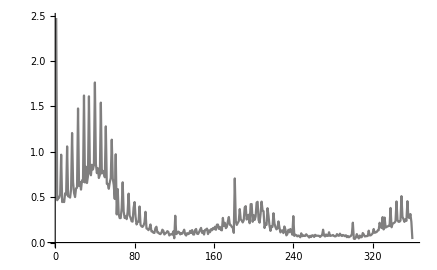

```mathematica
probkuler= ListLinePlot[Flatten[hueProbs[[1,1]]], PlotRange->All, ColorFunction->Function[{x,y},Hue[x]]]
```

Probability of a color being present in a highly-rated palette:

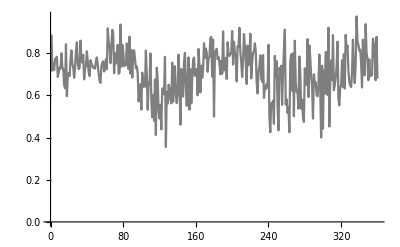

```mathematica
probrating= ListLinePlot[Flatten[hueProbs[[1,10]]], PlotRange->All, ColorFunction->Function[{x,y},Hue[x]]]
```

Probability of 2 hues being adjacent to each other”

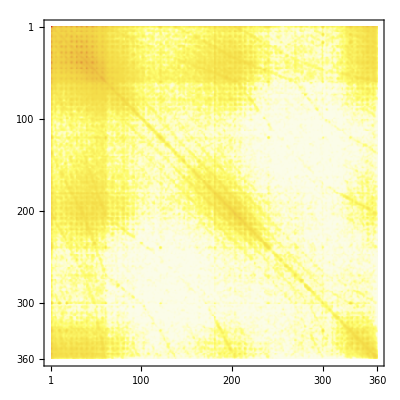

```mathematica
allhues = MatrixPlot[hueProbs[[1,2]], ColorFunction->"TemperatureMap"]
```

### Training a predictor

```mathematica
Take equal partition of each rating category:
```

```mathematica
awful= RandomSample[Select[kulerAssociation, #≤ 2&], 1000];
```

```mathematica
bad = RandomSample[Select[kulerAssociation, #≤ 3&& #> 2&], 1000];
```

```mathematica
good = RandomSample[Select[kulerAssociation, #≤ 4&& #> 3&], 1000];
```

```mathematica
best = RandomSample[Select[kulerAssociation, #>  4&], 1000];
```

```mathematica
dataset = RandomSample[Flatten[Normal[{awful, bad, good, best}]],4000] ;
```

```mathematica
{train, rest} = TakeDrop[Normal[dataset], Round[Length[dataset]*0.7]];
```

```mathematica
{test, validation} = TakeDrop[rest, Round[Length[rest]*0.5]];
```

```mathematica
predictor = Predict[train, ValidationSet->validation]
```

PredictorFunction[…]

```mathematica
measures = PredictorMeasurements[predictor, test]
```

PredictorMeasurementsObject[…]

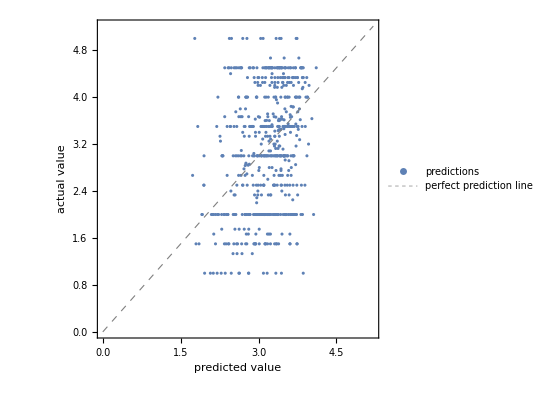

```mathematica
measures["ComparisonPlot"]
```

```mathematica
monocolors =Map[First,FindMainColorsHSB/@monochrome, {2}];
splitcolors =Map[First,FindMainColorsHSB/@splitcomplementary, {2}];
tetracolors = Map[First,FindMainColorsHSB/@tetradic, {2}];
analogcolors = Map[First,FindMainColorsHSB/@analogous, {2}];
compcolors = Map[First,FindMainColorsHSB/@complementary, {2}];
triadcolors = Map[First,FindMainColorsHSB/@triadic, {2}];
```

```mathematica
paletteToMatrix[palette_]:= SparseArray[Permutations[Floor[palette[[All, 1]]*100], {2}] +1->1, {100, 100}]
```

```mathematica
hueAdjacencyImage[palette_?MatrixQ]:=  ImageAdjust[Image[Total[paletteToMatrix/@palette]]]
```

```mathematica
hueAdjacencyImage[palette_?VectorQ]:=  ImageAdjust[Image[paletteToMatrix[palette]]]
```

```mathematica
hueAdjacencyImage[Keys[kulerBestColors]]
```

-Graphics-

Pairwise probability of adjacent hues. Patterns may not be visible since KUler interface provides built - in color templates but with RYB - wheel :

```mathematica
{ImageAdjust[hueAdjacencyImage[RandomSample[Keys[awful], 100]]], ImageAdjust[hueAdjacencyImage[RandomSample[Keys[bad], 100]]], ImageAdjust[hueAdjacencyImage[RandomSample[Keys[good], 100]]], ImageAdjust[hueAdjacencyImage[RandomSample[Keys[best], 100]]]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ImageAdjust[hueAdjacencyImage[Keys[Take[mturkAssociation, 100]]]],
ImageAdjust[hueAdjacencyImage[Keys[Take[mturkAssociation, -100]]]]}
```

{-Graphics-,-Graphics-}

```mathematica
{hueAdjacencyImage[monocolors], hueAdjacencyImage[analogcolors], hueAdjacencyImage[compcolors], hueAdjacencyImage[splitcolors], hueAdjacencyImage[triadcolors], hueAdjacencyImage[tetracolors]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
randomC = RandomColor[ 500, ColorSpace->"HSB"];
```

```mathematica
{hueAdjacencyImage[monochromaticS/@randomC], hueAdjacencyImage[analogousS/@randomC], hueAdjacencyImage[complementaryS/@randomC], hueAdjacencyImage[splitcomplementaryS/@randomC], hueAdjacencyImage[triadicS/@randomC], hueAdjacencyImage[tetradicS/@randomC]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fe = DimensionReduce[FeatureExtract[kulerHSBColors], 2]
```

{{0.595692,2.59675},{-0.420862,2.00315},{-0.550824,-0.282296},{-1.97397,1.36859},{-1.16968,0.12509},{-3.6344,1.21458},{-1.92812,0.173467},44972,{1.73627,-0.00282162},{1.65298,0.465634},{1.49173,0.466709},{-1.15679,0.166833},{-1.20809,1.41603},{0.944918,0.164598},{1.10041,-1.33462}}
 |  |  |  |

```mathematica
FEdataset = AssociationThread[fe->kulerRatings]
```

<|{0.595692,2.59675}→2.6923,{-0.420862,2.00315}→1.,{-0.550824,-0.282296}→1.6,{-1.97397,1.36859}→1.5714,{-1.16968,0.12509}→1.9167,{-3.6344,1.21458}→1.5455,{-1.92812,0.173467}→1.4444,44567,{1.65298,0.465634}→4.5,{1.49173,0.466709}→3.5,{-1.15679,0.166833}→3.6667,{-1.20809,1.41603}→3.,{0.944918,0.164598}→3.,{1.10041,-1.33462}→5.|>
 |  |  |  |

```mathematica
fedata = RandomSample[Normal[FEdataset]];
```

```mathematica
{fetrain, ferest} = TakeDrop[fedata, Round[Length[fedata]*0.7]];
```

```mathematica
{fetest, fevalidation} = TakeDrop[ferest, Round[Length[ferest]*0.5]];
```

```mathematica
predictFromFeature = Predict[fetrain, ValidationSet->fevalidation]
```

PredictorFunction[…]

```mathematica
newmeasures = PredictorMeasurements[predictFromFeature, fetest]
```

PredictorMeasurementsObject[…]

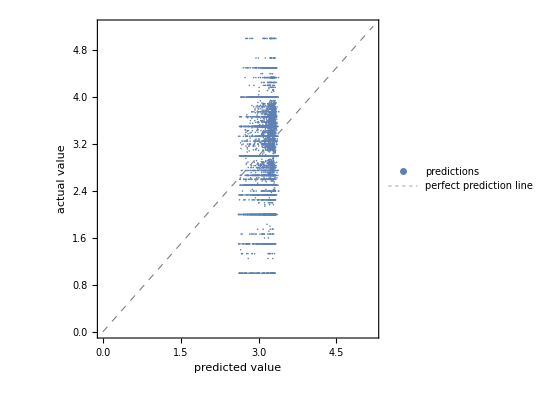

```mathematica
newmeasures["ComparisonPlot"]
```

```mathematica
images = Take[Image[List@@@Flatten[#, 1], ImageSize->5]&/@kulerRgbColors, -1000];
```

```mathematica
features = Take[fe, -1000];
```

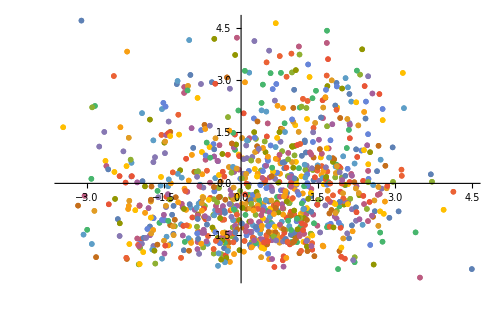

```mathematica
plot = ListPlot[List/@features,PlotMarkers->images,ImageSize->500]
```

```mathematica
badimages = Take[Image[List@@@Flatten[#, 1], ImageSize->5]&/@kulerRgbColors, 1000];
```

```mathematica
badfeatures = Take[fe, 1000];
```

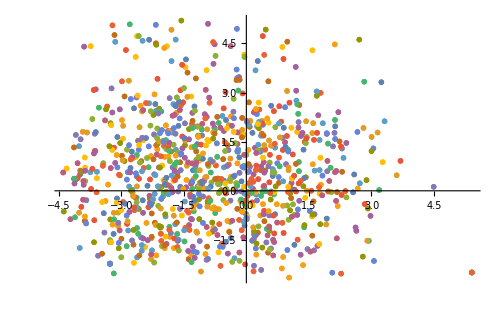

```mathematica
badplot = ListPlot[List/@badfeatures,PlotMarkers->badimages,ImageSize->500]
```

```mathematica
mturkFe = DimensionReduce[FeatureExtract[mturkHSBColors], 2];
```

```mathematica
mturkImages = Take[Image[List@@@Flatten[#, 1], ImageSize->5]&/@mturkRgbColors, 500];
```

```mathematica
mturkfeatures = Take[mturkFe, 500];
```

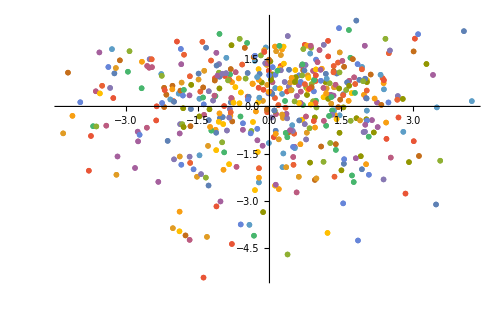

```mathematica
mturkPlot = ListPlot[List/@mturkfeatures,PlotMarkers->mturkImages,ImageSize->500]
```

```mathematica
mpredict= predictor/@monocolors;
apredict = predictor/@analogcolors;
cpredict = predictor/@compcolors;
spredict = predictor/@splitcolors;
tepredict = predictor/@tetracolors;
trpredict = predictor/@triadcolors;
predictions = {mpredict, apredict, cpredict, spredict, tepredict, trpredict};
```

```mathematica
Mean[#]&/@predictions
```

{3.08396,2.98813,2.82472,2.95384,2.57216,2.87145}

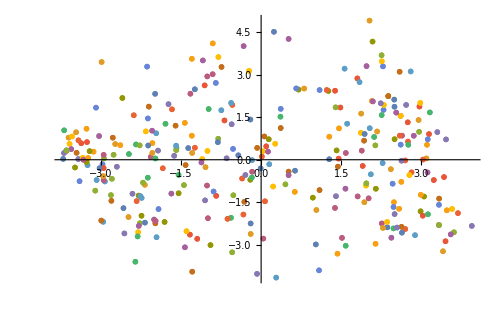

```mathematica
monorgb = ColorConvert[#, "RGB"]&/@monocolors;
monoimages = Image[List/@#, ImageSize->5]&/@monorgb;
monofeatures = DimensionReduce[FeatureExtract[monocolors], 2];
monoPlot = ListPlot[List/@monofeatures,PlotMarkers->monoimages,ImageSize->500]
```

### Predictor on generated palettes

```mathematica
randmono = monochromaticS/@RandomColor[500, ColorSpace->"HSB"];
randanalaog = analogousS/@RandomColor[500, ColorSpace->"HSB"];
randcomp = complementaryS/@RandomColor[500, ColorSpace->"HSB"];
randsplit = splitcomplementaryS/@RandomColor[500, ColorSpace->"HSB"];
randtria = triadicS/@RandomColor[500, ColorSpace->"HSB"];
randtetra = tetradicS/@RandomColor[500, ColorSpace->"HSB"];
```

```mathematica
randmpredict = predictor/@randmono;
randapredict = predictor/@randanalaog;
randcpredict = predictor/@randcomp;
randspredict = predictor/@randsplit;
randtrpredict = predictor/@randtria;
randtepredict = predictor/@randtetra;
randpredictions = {randmpredict, randapredict, randcpredict, randspredict, randtepredict, randtrpredict};
```

```mathematica
Mean[#]&/@randpredictions
```

```mathematica
{3.1966705199999996,3.0373582199999984,3.092184040000002,3.194152009999995,3.124433579999999,3.170719489999999}
```

```mathematica
hueProb = hueProbs[[1, 2]];
hueAdjProb = hueProbs[[1, 3]];
hueProbLog = hueProbs[[1, 4]];
hueAdjProbLog = hueProbs[[1, 5]];
```

### Feature Vector

```mathematica
createFeature[palette_]:=Module[{hsb, rgb,  h, s, v, l, a, b ,red, green, blue,hueangles , cos, sin,chsv1, chsv2, chsv3,chsv, chsvsorted,chsv1diff,chsv2diff,chsv3diff,chsvdiff1sorted, chsvdiff2sorted, chsvdiff3sorted,  vector, chsv1mean ,chsv2mean ,chsv3mean,chsv1std ,chsv2std,chsv3std ,chsv1min ,chsv2min ,chsv3min ,chsv1max,chsv2max ,chsv3max,chsv1minmax, chsv2minmax, chsv3minmax,chsv1norm, chsv2norm, chsv3norm, chsv1var, chsv2var, chsv3var,chsvsse, lab, labsorted,lab1diff,lab2diff ,lab3diff,labdiff1sorted, labdiff2sorted ,labdiff3sorted,lab1mean ,lab2mean ,lab3mean ,lab1std ,lab2std ,lab3std ,lab1min ,lab2min ,lab3min ,lab1max ,lab2max ,lab3max ,lab1minmax ,lab2minmax ,lab3minmax ,lab1norm, lab2norm, lab3norm, lab1var ,lab2var ,lab3var, labsse, hsbsorted,hsb1diff,hsb2diff ,hsb3diff,hsbdiff1sorted ,hsbdiff2sorted ,hsbdiff3sorted ,hsb1mean ,hsb2mean ,hsb3mean ,hsb1std ,hsb2std ,hsb3std ,hsb1min ,hsb2min ,hsb3min ,hsb1max ,hsb2max ,hsb3max ,hsb1minmax ,hsb2minmax ,hsb3minmax ,hsb1norm ,hsb2norm ,hsb3norm ,hsb1var ,hsb2var ,hsb3var ,
hsbsse, rgbsorted,rgb1diff,rgb2diff ,rgb3diff,rgbdiff1sorted ,rgbdiff2sorted ,rgbdiff3sorted ,rgb1mean ,rgb2mean,rgb3mean,rgb1std ,rgb2std ,rgb3std,rgb1min ,rgb2min ,rgb3min ,rgb1max ,rgb2max ,rgb3max ,rgb1minmax ,rgb2minmax ,rgb3minmax ,rgb1norm ,rgb2norm ,rgb3norm ,rgb1var ,rgb2var ,rgb3var ,rgbsse, roundedhues, probmean ,probstd ,probmin ,probmax ,adjprobmean ,adjprobstd ,adjprobmin ,adjprobmax ,logprobmean ,logprobstd ,logprobmin ,logprobmax ,logadjprobmean ,logadjprobstd ,logadjprobmin ,logadjprobmax },
rgb = palette;
hsb = Apply[List, ColorConvert[#, "HSB"]&/@palette, {1}];
lab = Apply[List, ColorConvert[#, "LAB"]&/@palette, {1}];
h = Map[Part[#, 1]&, hsb];
s =  Map[Part[#, 2]&, hsb];
v=  Map[Part[#, 3]&, hsb];
l = Map[Part[#, 1]&, lab];
a =  Map[Part[#, 2]&, lab];
b=  Map[Part[#, 3]&, lab];
red = Map[Part[#, 1]&, rgb];
green =  Map[Part[#, 2]&, rgb];
blue=  Map[Part[#, 3]&, rgb]; 
hueangles = h*360;
cos = Map[Cos[#]&, hueangles];
sin = Map[Sin[#]&, hueangles];
chsv1 = Times[cos, s];
chsv2 = Times[sin, s];
chsv3 = v;
chsv = MapThread[List, {chsv1, chsv2, chsv3}];
chsvsorted= Values[KeySort[AssociationThread[l, chsv]]];
chsv1diff = DistanceMatrix[chsv1];
chsv2diff = DistanceMatrix[chsv2];
chsv3diff = DistanceMatrix[chsv3];
chsvdiff1sorted = Values[KeySort[AssociationThread[l, chsv1diff]]];
chsvdiff2sorted = Values[KeySort[AssociationThread[l, chsv2diff]]];
chsvdiff3sorted = Values[KeySort[AssociationThread[l, chsv3diff]]];
chsv1mean = Mean[chsv1];
chsv2mean = Mean[chsv2];
chsv3mean = Mean[chsv3];
chsv1std = StandardDeviation[chsv1];
chsv2std = StandardDeviation[chsv2];
chsv3std = StandardDeviation[chsv3];
chsv1min = Min[chsv1];
chsv2min = Min[chsv2];
chsv3min = Min[chsv3];
chsv1max = Max[chsv1];
chsv2max = Max[chsv2];
chsv3max = Max[chsv3];
chsv1minmax = Subtract[ chsv1max,chsv1min];
chsv2minmax =Subtract[ chsv2max,chsv2min];
chsv3minmax = Subtract[ chsv3max,chsv3min];
chsv1norm = Norm[Part[#, 1]&/@PrincipalComponents[chsv]];
chsv2norm = Norm[Part[#, 2]&/@PrincipalComponents[chsv]];
chsv3norm = Norm[Part[#, 3]&/@PrincipalComponents[chsv]];
chsv1var = Variance[chsv1];
chsv2var = Variance[chsv2];
chsv3var = Variance[chsv3];
chsvsse = Norm[RegionDistance[ InfinitePlane[Mean[chsv],Take[PrincipalComponents[chsv], 2] ]]/@chsv];
lab = MapThread[List, {l, a, b}];
labsorted= Values[KeySort[AssociationThread[l, lab]]];
lab1diff = DistanceMatrix[l];
lab2diff = DistanceMatrix[a];
lab3diff = DistanceMatrix[b];
labdiff1sorted = Values[KeySort[AssociationThread[l, l]]];
labdiff2sorted = Values[KeySort[AssociationThread[l, a]]];
labdiff3sorted = Values[KeySort[AssociationThread[l, b]]];
lab1mean = Mean[l];
lab2mean = Mean[a];
lab3mean = Mean[b];
lab1std = StandardDeviation[l];
lab2std = StandardDeviation[a];
lab3std = StandardDeviation[b];
lab1min = Min[l];
lab2min = Min[a];
lab3min = Min[b];
lab1max = Max[l];
lab2max = Max[a];
lab3max = Max[b];
lab1minmax = Subtract[ lab1max,lab1min];
lab2minmax =Subtract[ lab2max,lab2min];
lab3minmax = Subtract[ lab3max,lab3min];
lab1norm = Norm[Part[#, 1]&/@PrincipalComponents[lab]];
lab2norm = Norm[Part[#, 2]&/@PrincipalComponents[lab]];
lab3norm = Norm[Part[#, 3]&/@PrincipalComponents[lab]];
lab1var = Variance[l];
lab2var = Variance[a];
lab3var = Variance[b];
"labsse = Norm[RegionDistance[ InfinitePlane[Mean[lab],Take[PrincipalComponents[lab], 2] ]]/@lab]";
hsbsorted= Values[KeySort[AssociationThread[l, hsb]]];
hsb1diff = DistanceMatrix[h];
hsb2diff = DistanceMatrix[s];
hsb3diff = DistanceMatrix[v];
hsbdiff1sorted = Values[KeySort[AssociationThread[l, h]]];
hsbdiff2sorted = Values[KeySort[AssociationThread[l, s]]];
hsbdiff3sorted = Values[KeySort[AssociationThread[l, v]]];
hsb1mean = Mean[h];
hsb2mean = Mean[s];
hsb3mean = Mean[v];
hsb1std = StandardDeviation[h];
hsb2std = StandardDeviation[s];
hsb3std = StandardDeviation[v];
hsb1min = Min[h];
hsb2min = Min[s];
hsb3min = Min[v];
hsb1max = Max[h];
hsb2max = Max[s];
hsb3max = Max[v];
hsb1minmax = Subtract[ hsb1max,hsb1min];
hsb2minmax =Subtract[ hsb2max,hsb2min];
hsb3minmax = Subtract[ hsb3max,hsb3min];
hsb1norm = Norm[Part[#, 1]&/@PrincipalComponents[hsb]];
hsb2norm = Norm[Part[#, 2]&/@PrincipalComponents[hsb]];
hsb3norm = Norm[Part[#, 3]&/@PrincipalComponents[hsb]];
hsb1var = Variance[h];
hsb2var = Variance[s];
hsb3var = Variance[v];
hsbsse = Norm[RegionDistance[ InfinitePlane[Mean[hsb],Take[PrincipalComponents[hsb], 2] ]]/@hsb];
rgbsorted= Values[KeySort[AssociationThread[l, rgb]]];
rgb1diff = DistanceMatrix[red];
rgb2diff = DistanceMatrix[green];
rgb3diff = DistanceMatrix[blue];
rgbdiff1sorted = Values[KeySort[AssociationThread[l, red]]];
rgbdiff2sorted = Values[KeySort[AssociationThread[l, green]]];
rgbdiff3sorted = Values[KeySort[AssociationThread[l, blue]]];
rgb1mean = Mean[red];
rgb2mean = Mean[green];
rgb3mean = Mean[blue];
rgb1std = StandardDeviation[red];
rgb2std = StandardDeviation[green];
rgb3std = StandardDeviation[blue];
rgb1min = Min[red];
rgb2min = Min[green];
rgb3min = Min[blue];
rgb1max = Max[red];
rgb2max = Max[green];
rgb3max = Max[blue];
rgb1minmax = Subtract[ rgb1max,rgb1min];
rgb2minmax =Subtract[ rgb2max,rgb2min];
rgb3minmax = Subtract[rgb3max,rgb3min];
rgb1norm = Norm[Part[#, 1]&/@PrincipalComponents[rgb]];
rgb2norm = Norm[Part[#, 2]&/@PrincipalComponents[rgb]];
rgb3norm = Norm[Part[#, 3]&/@PrincipalComponents[rgb]];
rgb1var = Variance[red];
rgb2var = Variance[green];
rgb3var = Variance[blue];
roundedhues= Round[hueangles];
probmean = Mean[hueProb[[#, #]]&/@roundedhues];
probstd = StandardDeviation[hueProb[[#, #]]&/@roundedhues];
probmin = Min[hueProb[[#, #]]&/@roundedhues];
probmax = Max[hueProb[[#, #]]&/@roundedhues];
adjprobmean = Mean[hueAdjProb[[#, #]]&/@roundedhues];
adjprobstd = StandardDeviation[hueAdjProb[[#, #]]&/@roundedhues];
adjprobmin = Min[hueAdjProb[[#, #]]&/@roundedhues];
adjprobmax = Max[hueAdjProb[[#, #]]&/@roundedhues];
logprobmean = Mean[hueProbLog[[#, #]]&/@roundedhues];
logprobstd = StandardDeviation[hueProbLog[[#, #]]&/@roundedhues];
logprobmin = Min[hueProbLog[[#, #]]&/@roundedhues];
logprobmax = Max[hueProbLog[[#, #]]&/@roundedhues];
logadjprobmean = Mean[hueAdjProbLog[[#, #]]&/@roundedhues];
logadjprobstd = StandardDeviation[hueAdjProbLog[[#, #]]&/@roundedhues];
logadjprobmin = Min[hueAdjProbLog[[#, #]]&/@roundedhues];
logadjprobmax = Max[hueAdjProbLog[[#, #]]&/@roundedhues];
rgbsse = Norm[RegionDistance[ InfinitePlane[Mean[rgb],Take[PrincipalComponents[rgb], 2] ]]/@rgb];
vector =Flatten[{chsv, chsvsorted, chsv1diff, chsv2diff, chsv3diff,chsvdiff1sorted, chsvdiff2sorted, chsvdiff3sorted, chsv1mean ,chsv2mean ,chsv3mean,chsv1std ,chsv2std,chsv3std ,chsv1min ,chsv2min ,chsv3min ,chsv1max,chsv2max ,chsv3max, chsv1minmax, chsv2minmax, chsv3minmax ,chsv1norm, chsv2norm, chsv3norm, chsv1var, chsv2var, chsv3var,lab, labsorted,lab1diff,lab2diff ,lab3diff,labdiff1sorted, labdiff2sorted ,labdiff3sorted,lab1mean ,lab2mean ,lab3mean ,lab1std ,lab2std ,lab3std ,lab1min ,lab2min ,lab3min ,lab1max ,lab2max ,lab3max ,lab1minmax ,lab2minmax ,lab3minmax ,lab1norm, lab2norm, lab3norm,lab1var ,lab2var ,lab3var,  hsb, hsbsorted,hsb1diff,hsb2diff ,hsb3diff,hsbdiff1sorted ,hsbdiff2sorted ,hsbdiff3sorted ,hsb1mean ,hsb2mean ,hsb3mean ,hsb1std ,hsb2std ,hsb3std ,hsb1min ,hsb2min ,hsb3min ,hsb1max ,hsb2max ,hsb3max ,hsb1minmax ,hsb2minmax ,hsb3minmax ,hsb1norm ,hsb2norm ,hsb3norm ,hsb1var ,hsb2var ,hsb3var , probmean ,probstd ,probmin ,probmax ,adjprobmean ,adjprobstd ,adjprobmin ,adjprobmax ,logprobmean ,logprobstd ,logprobmin ,logprobmax ,logadjprobmean ,logadjprobstd ,logadjprobmin ,logadjprobmax , rgb ,  rgbsorted,rgb1diff,rgb2diff ,rgb3diff,rgbdiff1sorted ,rgbdiff2sorted ,rgbdiff3sorted ,rgb1mean ,rgb2mean,rgb3mean,rgb1std ,rgb2std ,rgb3std,rgb1min ,rgb2min ,rgb3min ,rgb1max ,rgb2max ,rgb3max ,rgb1minmax ,rgb2minmax ,rgb3minmax ,rgb1norm ,rgb2norm ,rgb3norm ,rgb1var ,rgb2var ,rgb3var }] ]
```

### Predicting

```mathematica
kulerAssociation = AssociationThread[kulerRgbColors-> kulerRatings];
```

```mathematica
awful= RandomSample[Select[kulerAssociation, #≤ 2&], 2000];
```

```mathematica
bad = RandomSample[Select[kulerAssociation, #≤ 3&& #> 2&], 2000];
```

```mathematica
good = RandomSample[Select[kulerAssociation, #≤ 4&& #> 3&], 2000];
```

```mathematica
best = RandomSample[Select[kulerAssociation, #>  4&], 2000];
```

```mathematica
dataset = RandomSample[Flatten[Normal[{awful, bad, good, best}]],8000] ;
```

```mathematica
datavals = Values[dataset];
datafeatures = createFeature/@Keys[dataset]
```

{1}
 |  |  |  |

```mathematica
newdata = AssociationThread[datafeatures-> datavals];
```

```mathematica
{train, rest} = TakeDrop[Normal[newdata], Round[Length[newdata]*0.7]];
```

```mathematica
{test, validation} = TakeDrop[rest, Round[Length[rest]*0.5]];
```

```mathematica
predictor = Predict[train, ValidationSet->validation,  Method->"NeuralNetwork", PerformanceGoal->"Quality"]
```

PredictorFunction[…]

```mathematica
measures = PredictorMeasurements[predictor, test]
```

PredictorMeasurementsObject[…]

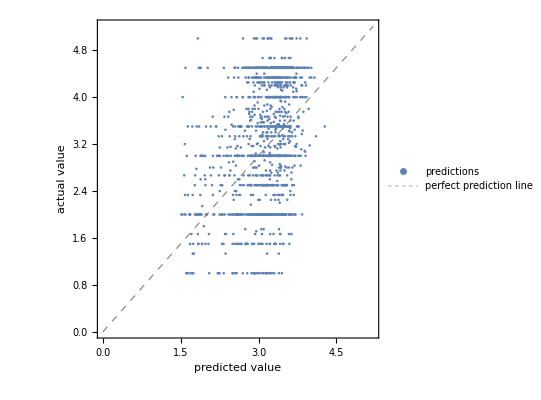

```mathematica
measures["ComparisonPlot"]
```

```mathematica
PredictorInformation[predictor]
```

Predictor information
Method | Neural network
Number of features | 1
Number of training examples | 2800
L1 regularization coefficient | 0
L2 regularization coefficient | 0.1
Number of hidden layers | 2
Hidden nodes | ,,306306
Hidden layer activation functions | ,,TanhTanh
CostFunction | Cost Function

```mathematica
measurestrain = PredictorMeasurements[predictor, train]
```

PredictorMeasurementsObject[…]

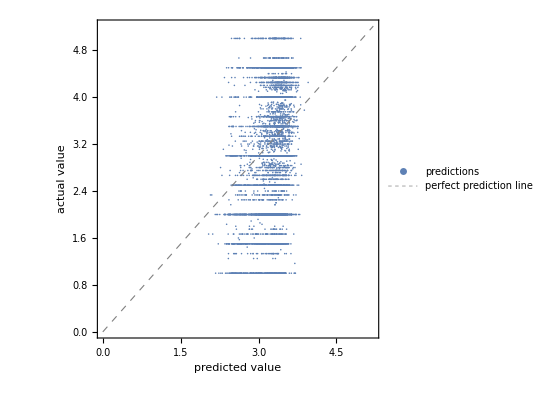

```mathematica
measurestrain["ComparisonPlot"]
```

## Cloud Form

```mathematica
makeimg[img_]:= Module[{c, im}, c = ColorConvert[ col[img], "RGB"]; im  = ImageResize[Image[Transpose[List/@c]], ImageDimensions[img][[1]]/2]; im]
makeschemeimg[img_, scheme_]:= Module[{c, im}, c = ColorConvert[ scheme[First[col[img]]], "RGB"]; im  = ImageResize[Image[Transpose[List/@c]], ImageDimensions[img][[1]]/2]; im]
```

```mathematica
col[monochrome[[3]]]
```

{Hue[0.10860657843251646, 0.8107702626008007, 0.7805494572151526],Hue[0.10623783650857528, 0.8459732512468182, 0.813887359621506],Hue[0.11257659946385114, 0.9128753555763763, 0.6158613980077488],Hue[0.11186967167650395, 0.8709767784349041, 0.5502012747781273],Hue[0.08993171197555601, 0.41229613876948074, 0.7732877429634002]}

```mathematica
monochrome[[3]]
makeimg[monochrome[[3]]]
```

-Graphics-

-Graphics-

```mathematica
makeschemeimg[monochrome[[3]], monochromaticScheme]
```

-Graphics-

```mathematica
nearesthtml= Nearest[Reverse/@ColorData["HTML", "ColorRules"]];
htmlcolors[color_?ColorQ]:= First[nearesthtml[color]]
```

```mathematica
testimage = RandomChoice[analogous];
```

```mathematica
schemes = {"Monochromatic"->monochromaticScheme, "Analogous"-> analogousScheme,  "Complementary" -> complementaryScheme, "Split-complementary"-> splitScheme, "Triadic" -> triadicScheme, "Tetradic" -> tetradicScheme};
```

```mathematica
computecolors[color_]:={ImageResize[Image[color], 30],Round[List@@color, 0.01],Round[List@@ColorConvert[color, "RGB"]*256], Round[List@@ColorConvert[color, "LAB"], 0.01], htmlcolors[color]}
```

```mathematica
makegrid[img_, colors_]:= Grid[Prepend[computecolors/@colors, {"Color","HSV","RGB","LAB", "HTML"}],  Spacings->{1, 1}]
```

```mathematica
tablecreate[img_, s_:Automatic, r_:0, n_:5] :=Quiet[
Module[
	{testimage = RemoveAlphaChannel[img],
	colors=col[RemoveAlphaChannel[img]],
	scheme
	},
	scheme = Replace[s, Automatic -> Lookup[schemes, class[testimage]]];
	Column[{
		ImageResize[testimage, ImageDimensions[testimage][[1]]],
		Spacer[{20, 20}],
		Column[ {"Original palette:", makeimg[testimage]}],
		Spacer[{5,5}],
		Row[{Column[{"Nearest color scheme is", class[testimage]}],
		Spacer[{5,5}],
		wheel[col[testimage]]
	}],
	Column[{
		"Generated palette:",
		Spacer[{5,5}],
		makeschemeimg[testimage, scheme]
	}],
	Spacer[{5,5}], Row[{wheel[makeschemeimg[testimage, scheme]]}], Spacer[{5,5}], Column[{makegrid[testimage, colors], 
makegrid[testimage, scheme[First[colors],r, n]]}]}, Spacer[{5,5}]]], ImageResize::cscycl]
tablecreate[analogous[[3]]]
```

-Graphics-

Original palette:
-Graphics-

Nearest color scheme is
Split-complementary-Graphics-
Generated palette:

-Graphics-

-Graphics-

Color | HSV | RGB | LAB | HTML
-Graphics- | {0.5,0.29,0.} | {0,0,0} | {0.,0.,0.} | Black
-Graphics- | {1.,0.86,0.92} | {235,32,34} | {0.51,0.73,0.54} | Red
-Graphics- | {0.12,0.69,0.89} | {229,189,70} | {0.78,0.06,0.62} | Goldenrod
-Graphics- | {1.,0.83,0.33} | {84,14,16} | {0.17,0.32,0.19} | Maroon
-Graphics- | {0.12,0.64,0.37} | {95,78,35} | {0.34,0.03,0.28} | DarkOliveGreen
Color | HSV | RGB | LAB | HTML
-Graphics- | {0.5,0.29,0.} | {0,0,0} | {0.,0.,0.} | Black
-Graphics- | {0.5,0.54,0.51} | {60,130,130} | {0.5,-0.23,-0.07} | Teal
-Graphics- | {0.1,0.61,0.53} | {135,102,52} | {0.46,0.09,0.33} | Sienna
-Graphics- | {0.1,0.41,0.74} | {190,158,111} | {0.67,0.07,0.29} | Tan
-Graphics- | {0.9,0.61,0.85} | {216,85,164} | {0.56,0.58,-0.15} | HotPink

```mathematica
i =-Graphics-;
```

```mathematica
tablecreate[i]
```

-Graphics-

Original palette:
-Graphics-

Nearest color scheme is
Triadic-Graphics-
Generated palette:

-Graphics-

-Graphics-

Color | HSV | RGB | LAB | HTML
-Graphics- | {0.56,0.34,0.59} | {100,134,152} | {0.54,-0.09,-0.14} | LightSlateGray
-Graphics- | {0.99,0.53,0.54} | {138,65,69} | {0.37,0.32,0.13} | IndianRed
-Graphics- | {0.96,0.26,0.57} | {145,107,115} | {0.49,0.16,0.02} | RosyBrown
-Graphics- | {0.68,0.11,0.53} | {122,120,136} | {0.51,0.03,-0.08} | SlateGray
-Graphics- | {0.02,0.22,0.85} | {217,176,170} | {0.75,0.14,0.09} | RosyBrown
Color | HSV | RGB | LAB | HTML
-Graphics- | {0.56,0.34,0.59} | {100,134,152} | {0.54,-0.09,-0.14} | LightSlateGray
-Graphics- | {0.56,0.61,0.9} | {90,181,230} | {0.7,-0.17,-0.33} | LightSkyBlue
-Graphics- | {0.56,0.96,0.7} | {7,119,179} | {0.47,-0.11,-0.4} | SteelBlue
-Graphics- | {0.56,0.91,0.5} | {12,88,128} | {0.34,-0.1,-0.29} | SteelBlue
-Graphics- | {0.56,0.72,0.3} | {22,58,77} | {0.22,-0.08,-0.16} | DarkSlateGray

```mathematica
form = CloudDeploy[
	FormPage[{"image"->"Image","scheme"-> schemes, "randomness"-> <|"Interpreter"->Restricted["Real",{0, 0.5}], "Required"-> False, "Control" -> Slider|>},
	tablecreate[#image, #scheme, #randomness, 5]&, AppearanceRules-><|"Title" -> "Color Scheme Generator"|>],
	Permissions->"Public"
]
```

CloudObject[]

```mathematica
form = CloudDeploy[
	FormPage[{
			"image"->"Image",
			"scheme"-> <|"Interpreter" -> Prepend[schemes, Automatic -> Automatic], "Required"-> False, "Control" -> PopupMenu, "Default" -> Automatic|>,
			"randomness"-> <|"Interpreter" -> Restricted["Real",{0, 0.5}], "Required"-> False, "Control" -> Slider|>
		},
	tablecreate[#image, #scheme, #randomness, 5]&, AppearanceRules-><|"Title" -> "Color Scheme Generator"|>],
	Permissions->"Public"
]
```

CloudObject[]